```mathematica
Quit[]
```

```mathematica
(*STEP 1:Load FeynCalc with FeynArts*)$LoadAddOns={"FeynArts"};

Needs["FeynCalc`"];

$FAVerbose=0;

Print["======================================"];
Print["STEP 1: PACKAGE INITIALIZATION"];
Print["======================================"];

Print["FeynCalc version: ",$FeynCalcVersion];
Print["FeynArts directory: ",$FeynArtsDirectory];


(*STEP 2:Define Phi4 model directory*)

Print[""];
Print["STEP 2: MODEL DIRECTORY"];

faModelsDir=FileNameJoin[{$FeynArtsDirectory,"Models"}];

phi4Dir=FileNameJoin[{faModelsDir,"Phi4"}];

phi4Name=FileNameJoin[{"Phi4","Phi4"}];

Print["Phi4 directory: ",phi4Dir];


(*STEP 3:Verify required model files*)

Print[""];
Print["STEP 3: VERIFY MODEL FILES"];

requiredFiles={"Phi4.mod","Phi4.gen","Phi4.pars"};

fileChecks=Association[Table[file->FileExistsQ[FileNameJoin[{phi4Dir,file}]],{file,requiredFiles}]];

KeyValueMap[(Print[#1,": ",#2])&,fileChecks];

If[!And@@Values[fileChecks],Print["ERROR: One or more model files are missing."];
Abort[];];

Print["All required model files found."];


(*STEP 4:Check the previous line-84 error*)

Print[""];
Print["STEP 4: CHECK GENERIC MODEL SYNTAX"];

genFile=FileNameJoin[{phi4Dir,"Phi4.gen"}];

genText=Import[genFile,"Text"];

If[!StringQ[genText],Print["ERROR: Cannot read Phi4.gen."];
Abort[];];

malformedIndexSum=StringContainsQ[genText,RegularExpression["IndexSum\\s*\\[\\s*,"]];

Print["Malformed IndexSum detected: ",malformedIndexSum];

If[malformedIndexSum,Print["ERROR: Old line-84 syntax issue detected."];
Print["Restore the corrected Phi4 model files."];
Abort[];];

Print["Known syntax problem not detected."];


(*STEP 5:Verify FeynArts functions*)

Print[""];
Print["STEP 5: VERIFY FEYNARTS FUNCTIONS"];

functionNames={"CreateTopologies","InsertFields","Paint","CreateFeynAmp","InitializeModel"};

functionMatches=Table[Names["*`"<>name],{name,functionNames}];

Do[Print[functionNames[[i]],": ",functionMatches[[i]]],{i,Length[functionNames]}];

If[AnyTrue[functionMatches,#==={}&],Print["ERROR: Some FeynArts functions are missing."];
Abort[];];

Print["FeynArts functions found."];


(*STEP 6:Check model search path*)

Print[""];
Print["STEP 6: CONFIGURE MODEL SEARCH PATH"];

If[!MemberQ[$ModelPath,faModelsDir],AppendTo[$ModelPath,faModelsDir]];

Print["Phi4 model name: ",phi4Name];

Print["Model file exists: ",FileExistsQ[FileNameJoin[{phi4Dir,"Phi4.mod"}]]];


(*STEP 7:Initialize Phi4*)

Print[""];
Print["STEP 7: INITIALIZE PHI4 MODEL"];

modelResult=InitializeModel[phi4Name,GenericModel->phi4Name];

Print["Initialization result: ",modelResult];

If[modelResult=!=True,Print["ERROR: Phi4 model initialization failed."];
Abort[];];


(*STEP 8:Final confirmation*)

Print[""];
Print["======================================"];
Print["PHI4 ENVIRONMENT READY"];
Print["======================================"];

Print["FeynCalc: Loaded"];
Print["FeynArts: Loaded"];
Print["Phi4 files: Found"];
Print["Known line-84 error: Not detected"];
Print["Model initialization: Successful"];

Print[""];
Print["You may now generate Feynman diagrams."];
```

FeynCalc 10.2.1 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

======================================

STEP 1: PACKAGE INITIALIZATION

======================================

FeynCalc version: 10.2.1

FeynArts directory: C:\Users\sirmo\AppData\Roaming\Wolfram\Applications\FeynCalc\FeynArts

STEP 2: MODEL DIRECTORY

Phi4 directory: C:\Users\sirmo\AppData\Roaming\Wolfram\Applications\FeynCalc\FeynArts\Models\Phi4

STEP 3: VERIFY MODEL FILES

Phi4.mod: True

Phi4.gen: True

Phi4.pars: True

All required model files found.

STEP 4: CHECK GENERIC MODEL SYNTAX

Malformed IndexSum detected: False

Known syntax problem not detected.

STEP 5: VERIFY FEYNARTS FUNCTIONS

CreateTopologies: {CreateTopologies}

InsertFields: {InsertFields}

Paint: {Paint}

CreateFeynAmp: {CreateFeynAmp}

InitializeModel: {InitializeModel}

FeynArts functions found.

STEP 6: CONFIGURE MODEL SEARCH PATH

Phi4 model name: Phi4\Phi4

Model file exists: True

STEP 7: INITIALIZE PHI4 MODEL

Initialization result: True

======================================

PHI4 ENVIRONMENT READY

======================================

FeynCalc: Loaded

FeynArts: Loaded

Phi4 files: Found

Known line-84 error: Not detected

Model initialization: Successful

You may now generate Feynman diagrams.

SECTION 2.1

PART 2 - SECTION 2.1 - TASK 1

Theory: Real scalar Phi^4   [QFT I, Chapter 8, p.66]

Euclidean dimension: d = 4 - eps   [Assignment, Part 2]

Critical mass: m = 0   [QFT I, Eq. (15.5), p.149]

External momentum: p^2 > 0   [Assignment, Part 2]

Loop momenta: k and l

Coupling notation: lam

Model: Phi4\Phi4

1. Diagram counting

Number of vertices V = 2

Number of internal lines I = 3

Number of external legs E = 2

Number of loops L = 2   [Derived using L = I - V + 1; cf. QFT I, Chapter 8, pp.65-66]

Diagram counting verified: True

2. Generate two-loop 1PI topologies

Topology generation completed.   [Assignment, Sec. 2.1; FeynArts CreateTopologies]

3. Insert the real scalar field

Field insertion completed.   [Assignment, Sec. 2.1; FeynArts InsertFields]

4. Two-loop 1PI Feynman diagrams

Sunset and double-scoop topologies   [Assignment, Sec. 2.1; sunset: QFT I, Chapter 13, p.104; double scoop: classified here]

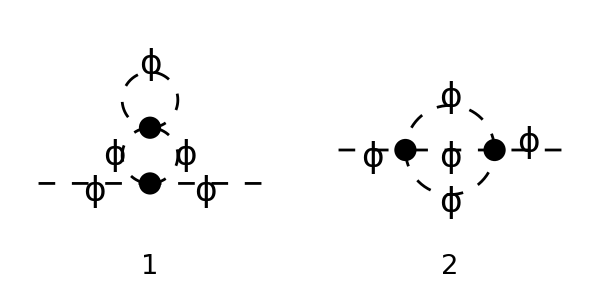

5. Generate FeynArts amplitudes

FeynArts amplitudes generated.   [Assignment, Sec. 2.1; FeynArts CreateFeynAmp]

6. Convert amplitudes to FeynCalc

Mass symbol replacement successful: True

Number of converted diagrams = 2   [FeynCalc output; Assignment, Sec. 2.1]

Converted amplitudes (mass written as m):

Diagram 1: (ⅈ lam^2)/(4 (k^2-m^2)^2 (l^2-m^2))

Diagram 2: (ⅈ lam^2)/(6 (k^2-m^2).(l^2-m^2).((k+l+p)^2-m^2))

7. Massless amplitudes at criticality

Massless limit imposed: m = 0   [QFT I, Eq. (15.5), p.149; Assignment, Part 2]

Massless amplitude 1: (ⅈ lam^2)/(4 (k^2)^2 l^2)

Massless amplitude 2: (ⅈ lam^2)/(6 k^2.l^2.(k+l+p)^2)

8. External-momentum dependence

Total converted diagrams = 2

Momentum-dependent diagram numbers: {2}

Momentum-independent diagram numbers: {1}

Number of momentum-dependent diagrams = 1   [QFT I, Chapter 13, pp.104-105; classified here]

Number of momentum-independent diagrams = 1   [Derived here from the double-scoop momentum routing]

Momentum-dependent amplitudes:

Diagram 2: (ⅈ lam^2)/(6 k^2.l^2.(k+l+p)^2)

Momentum-independent amplitudes:

Diagram 1: (ⅈ lam^2)/(4 (k^2)^2 l^2)

9. Sunset symmetry factor

Common denominator 2!(4!)^2 = 1152   [QFT I, Eq. (8.4), p.64]

Sunset contraction multiplicity = 192   [QFT I, Chapter 8, pp.65-66]

Sunset symmetry weight 1/S = 1/6   [QFT I, Chapter 8, p.66; Chapter 13, p.104]

Sunset symmetry factor S = 6   [QFT I, Chapter 8, p.66]

10. Double-scoop symmetry factor

Double-scoop contraction multiplicity = 288   [Derived using QFT I, Eq. (8.4), p.64]

Double-scoop symmetry weight 1/S = 1/4   [Derived here from Wick contractions]

Double-scoop symmetry factor S = 4   [Derived here]

11. Euclidean momentum-space integrands

SUNSET

Internal momenta: k, l, p-k-l   [QFT I, Chapter 13, p.104]

Denominator: k^2 l^2 (p-k-l)^2   [Assignment, Sec. 2.1; QFT I, Chapter 13, p.104]

Overall loop factor: mu^(2 eps)

Symmetry weight: 1/6   [QFT I, Chapter 8, p.66]

Connected amputated term: (lam^2/6) H(p)   [QFT I, Chapter 13, p.104; sign convention deferred]

DOUBLE SCOOP

Internal momenta: k, -k, l   [Derived here]

Denominator: (k^2)^2 l^2   [Derived here]

External momentum dependence: none

Symmetry weight: 1/4

Massless DR integral: scaleless -> 0   [Derived here; cf. QFT I, Chapter 15, pp.149-150]

12. Verification checks

Verification | Passed?
Two quartic vertices | True
Three internal propagators | True
Two-loop topology | True
Two external legs | True
Sunset symmetry weight = 1/6 | True
Double-scoop symmetry weight = 1/4 | True
Two converted 1PI diagrams | True
One explicitly momentum-dependent diagram | True
One explicitly momentum-independent diagram | True
All diagrams classified | True
No remaining mphi mass symbol | True

All checks passed: True

TASK 1 CONCLUSION

Expected two-loop 1PI two-point diagrams: 2

Sunset symmetry weight = 1/6   [QFT I, Chapter 8, p.66; Chapter 13, p.104]

Double-scoop symmetry weight = 1/4   [Derived here]

Momentum-dependent diagram count = 1

Only the sunset contributes nontrivially to the momentum dependence.

The double-scoop integral vanishes in massless DR.

Next task: Evaluate the sunset integral H(p) by two successive massless one-loop convolutions.

```mathematica
(* ============================================================*)(*QFT1 MIDTERM PROJECT*)(*PART 2-SECTION 2.1-TASK 1*)(*Two-loop 1PI two-point diagrams in real scalar Phi^4 theory*)(* ============================================================*)(*References:Assignment,Part 2,Section 2.1:Two-loop 1PI two-point diagrams,FeynArts/FeynCalc amplitudes,momentum dependence,symmetry factors.QFT I,Chapter 8,Eq.(8.4),p.64:Second-order perturbation expansion and Wick contractions.QFT I,Chapter 8,pp.65-66:Sunset Wick contractions and the symmetry weight 1/3!.QFT I,Chapter 8,p.66:Feynman rules for scalar Phi^4 theory.QFT I,Chapter 13,pp.104-105:Sunset loop integral,symmetry weight,and p-dependence.QFT I,Appendix A,pp.131-132:Two-loop two-point diagrams and counterterm structure.QFT I,Chapter 15,Eq.(15.5),p.149:Critical massless two-point condition.Page numbers above are the printed lecture-note pages.Results not stated explicitly in the notes are labeled'Derived here';package steps cite the assignment.*)(*------------------------------------------------------------*)(*0. INITIALIZATION*)(*------------------------------------------------------------*)(*Use the previously installed and patched FeynArts package.*)If[!MemberQ[$Packages,"FeynCalc`"],$LoadAddOns={"FeynArts"};
Needs["FeynCalc`"];];

If[!MemberQ[$Packages,"FeynArts`"],Needs["FeynArts`"];];

$FAVerbose=0;

(*Clear variables from previous evaluations of this task.*)

ClearAll[phi4Model21,topo21,diag21,ampFA21,ampRaw21,ampFC21,ampMassless21,massSymbols21,remainingMass21,nDiagrams21,nDependent21,nIndependent21,momentumDependent21,momentumIndependent21,v21,e21,i21,loops21,normalization21,nSunset21,nDouble21,weightSunset21,weightDouble21,checks21,p,k,l,m,eps,mu,lam,g];

phi4Model21=FileNameJoin[{"Phi4","Phi4"}];

Print[Style["PART 2 - SECTION 2.1 - TASK 1",16,Bold]];

Print["Theory: Real scalar Phi^4","   [QFT I, Chapter 8, p.66]"];
Print["Euclidean dimension: d = 4 - eps","   [Assignment, Part 2]"];
Print["Critical mass: m = 0","   [QFT I, Eq. (15.5), p.149]"];
Print["External momentum: p^2 > 0","   [Assignment, Part 2]"];
Print["Loop momenta: k and l"];
Print["Coupling notation: lam"];
Print["Model: ",phi4Model21];

(*Our conventions:d=4-eps g=lam/(16 Pi^2) The model's quartic coupling is renamed lam.We do not assign a value to g in this task.FeynCalc retains D as its internal dimension symbol.The massless limit is imposed only after converting the FeynArts amplitudes.*)


(*------------------------------------------------------------*)
(*1. MATHEMATICAL DIAGRAM COUNTING*)
(*------------------------------------------------------------*)

Print[Style["\n1. Diagram counting",14,Bold]];

(*For a connected Feynman diagram:L=I-V+1 where:L=number of loops I=number of internal propagators V=number of interaction vertices For quartic interactions:4 V=2 I+E For a two-point function:E=2 Therefore:I=2 V-1 Substituting into the loop equation:L=(2 V-1)-V+1=V Since L=2:V=2 I=3 E=2[Derived here from connected-graph counting;
cf.QFT I,Chapter 8,pp.65-66.]*)

v21=2;
e21=2;

i21=(4 v21-e21)/2;
loops21=i21-v21+1;

Print["Number of vertices V = ",v21];
Print["Number of internal lines I = ",i21];
Print["Number of external legs E = ",e21];
Print["Number of loops L = ",loops21,"   [Derived using L = I - V + 1; cf. QFT I, Chapter 8, pp.65-66]"];

Print["Diagram counting verified: ",TrueQ[v21==2&&i21==3&&e21==2&&loops21==2]];


(*------------------------------------------------------------*)
(*2. GENERATE TWO-LOOP 1PI TOPOLOGIES*)
(*------------------------------------------------------------*)

Print[Style["\n2. Generate two-loop 1PI topologies",14,Bold]];

(*Generate two-loop 1->1 topologies.Reducible:Exclude one-particle-reducible diagrams.WFCorrections:Exclude external-leg self-energy insertions.Tadpoles are NOT excluded because the double-scoop 1PI graph contains a tadpole.[Assignment,Sec.2.1;FeynArts CreateTopologies.]*)

topo21=CreateTopologies[2,1->1,ExcludeTopologies->{Reducible,WFCorrections}];

Print["Topology generation completed.","   [Assignment, Sec. 2.1; FeynArts CreateTopologies]"];


(*------------------------------------------------------------*)
(*3. INSERT THE REAL SCALAR FIELD*)
(*------------------------------------------------------------*)

Print[Style["\n3. Insert the real scalar field",14,Bold]];

(*The real scalar field is S[1] in our Phi4 model.[Assignment,Sec.2.1;FeynArts InsertFields.]*)

diag21=InsertFields[topo21,{S[1]}->{S[1]},Model->phi4Model21,GenericModel->phi4Model21,InsertionLevel->{Particles}];

Print["Field insertion completed.","   [Assignment, Sec. 2.1; FeynArts InsertFields]"];


(*------------------------------------------------------------*)
(*4. DRAW THE FEYNMAN DIAGRAMS*)
(*------------------------------------------------------------*)

Print[Style["\n4. Two-loop 1PI Feynman diagrams",14,Bold]];
Print["Sunset and double-scoop topologies","   [Assignment, Sec. 2.1; sunset: QFT I, Chapter 13, p.104;"," double scoop: classified here]"];

(*Expected diagram classes:1. Sunset:Three internal lines joining two vertices.2. Double scoop:Two lines joining the vertices and one tadpole attached to the second vertex.FeynArts may display them in either order.Sunset:QFT I,Chapter 13,p.104;
cf.Appendix A,pp.131-132. Double scoop:topology classified here.*)

Paint[diag21,ColumnsXRows->{2,1},Numbering->Simple,SheetHeader->None,ImageSize->{600,300}];


(*------------------------------------------------------------*)
(*5. CREATE FEYNARTS AMPLITUDES*)
(*------------------------------------------------------------*)

Print[Style["\n5. Generate FeynArts amplitudes",14,Bold]];

(*Truncated->True:External propagators are removed.PreFactor->1:Keep the loop-measure prefactor separate.[Assignment,Sec.2.1;FeynArts CreateFeynAmp;
scalar Feynman rules:QFT I,Chapter 8,p.66.]*)

ampFA21=CreateFeynAmp[diag21,Truncated->True,PreFactor->1];

Print["FeynArts amplitudes generated.","   [Assignment, Sec. 2.1; FeynArts CreateFeynAmp]"];


(*------------------------------------------------------------*)
(*6. CONVERT AMPLITUDES USING FEYNCALC*)
(*------------------------------------------------------------*)

Print[Style["\n6. Convert amplitudes to FeynCalc",14,Bold]];

(*External momentum:Incoming:p Outgoing:p Loop momenta:k,l FeynCalc uses D for the spacetime dimension.FinalSubstitutions first attempts to rename the model mass Mphi to m and model coupling g to lam.[Assignment,Sec.2.1;FeynCalc FCFAConvert.]*)

ampRaw21=FCFAConvert[ampFA21,IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{k,l},ChangeDimension->D,List->True,SMP->True,UndoChiralSplittings->True,DropSumOver->True,FinalSubstitutions->{Mphi->m,g->lam}];

(*Check that conversion returned a nonempty list.*)

If[!ListQ[ampRaw21]||Length[ampRaw21]==0,Print["ERROR: FCFAConvert did not return a ","nonempty list of amplitudes."];
Abort[];];


(*------------------------------------------------------------*)
(*6A.ENSURE THE MASS IS ALWAYS NAMED m*)
(*------------------------------------------------------------*)

(*The mass parameter may occur as Mphi,mphi,or as a symbol from a different Mathematica context.SymbolName identifies it independently of context.*)

massSymbols21=DeleteDuplicates[Cases[ampRaw21,s_Symbol/;ToLowerCase[SymbolName[s]]=="mphi":>s,Infinity]];

(*Replace all mass symbols named Mphi/mphi with m.Also handle possible SMP mass notation.*)

ampFC21=ampRaw21/.
(s_Symbol/;ToLowerCase[SymbolName[s]]=="mphi":>m);

ampFC21=ampFC21/. {SMP["Mphi"]->m,SMP["mphi"]->m};

(*Ensure the model's original coupling g is represented by lam,regardless of context.*)

ampFC21=ampFC21/.
(s_Symbol/;SymbolName[s]=="g":>lam);


(*Verify that the old mass symbol has disappeared.*)

remainingMass21=DeleteDuplicates[Cases[ampFC21,s_Symbol/;ToLowerCase[SymbolName[s]]=="mphi":>s,Infinity]];

Print["Mass symbol replacement successful: ",remainingMass21==={}&&FreeQ[ampFC21,SMP["Mphi"]]&&FreeQ[ampFC21,SMP["mphi"]]];

(*IMPORTANT:Define the diagram count before Section 8.*)

nDiagrams21=Length[ampFC21];

Print["Number of converted diagrams = ",nDiagrams21,"   [FeynCalc output; Assignment, Sec. 2.1]"];

Print[Style["\nConverted amplitudes (mass written as m):",12,Bold]];

Do[Print["Diagram ",j,": ",ampFC21[[j]]],{j,1,nDiagrams21}];


(*------------------------------------------------------------*)
(*7. MASSLESS LIMIT AT CRITICALITY*)
(*------------------------------------------------------------*)

Print[Style["\n7. Massless amplitudes at criticality",14,Bold]];

(*At criticality:m=0 External momentum p remains nonzero.The massless limit is imposed locally,without globally assigning m=0.[QFT I,Eq.(15.5),p.149;
Assignment,Part 2:nonzero Euclidean p^2.]*)

ampMassless21=(ampFC21/. m->0)//FCI;

Print["Massless limit imposed: m = 0","   [QFT I, Eq. (15.5), p.149; Assignment, Part 2]"];

Do[Print["Massless amplitude ",j,": ",ampMassless21[[j]]],{j,1,nDiagrams21}];


(*------------------------------------------------------------*)
(*8. IDENTIFY MOMENTUM-DEPENDENT DIAGRAMS*)
(*------------------------------------------------------------*)

Print[Style["\n8. External-momentum dependence",14,Bold]];

(*We first classify the converted integrands by whether they explicitly contain external momentum p.This is a structural check,not an integration.Sunset:Depends on p.Double scoop:Independent of p.[Sunset:QFT I,Chapter 13,pp.104-105;
double-scoop momentum routing:derived here.]*)

(*Recompute the count to avoid undefined variables.*)

nDiagrams21=Length[ampMassless21];

momentumDependent21=Select[Range[nDiagrams21],!FreeQ[ampMassless21[[#]],p]&];

momentumIndependent21=Select[Range[nDiagrams21],FreeQ[ampMassless21[[#]],p]&];

nDependent21=Length[momentumDependent21];
nIndependent21=Length[momentumIndependent21];

Print["Total converted diagrams = ",nDiagrams21];

Print["Momentum-dependent diagram numbers: ",momentumDependent21];

Print["Momentum-independent diagram numbers: ",momentumIndependent21];

Print["Number of momentum-dependent diagrams = ",nDependent21,"   [QFT I, Chapter 13, pp.104-105; classified here]"];

Print["Number of momentum-independent diagrams = ",nIndependent21,"   [Derived here from the double-scoop momentum routing]"];


(*Display the momentum-dependent amplitudes.*)

Print[Style["\nMomentum-dependent amplitudes:",12,Bold]];

Do[Print["Diagram ",j,": ",ampMassless21[[j]]],{j,momentumDependent21}];


(*Display the momentum-independent amplitudes.*)

Print[Style["\nMomentum-independent amplitudes:",12,Bold]];

Do[Print["Diagram ",j,": ",ampMassless21[[j]]],{j,momentumIndependent21}];


(*------------------------------------------------------------*)
(*9. DERIVE THE SUNSET SYMMETRY FACTOR*)
(*------------------------------------------------------------*)

Print[Style["\n9. Sunset symmetry factor",14,Bold]];

(*Second-order interaction expansion:exp(-S_int)=1-S_int+S_int^2/2!+... Each Phi^4 vertex carries a factor 1/4!.Therefore the common normalization is:1/[2! (4!)^2] Sunset Wick contraction counting:2 ways to assign the two external points 4 choices at the first interaction vertex 4 choices at the second interaction vertex 3! ways to contract the remaining internal legs Hence:N_sunset=2*4*4*3!=192 1/S_sunset=N_sunset/[2! (4!)^2][QFT I,Eq.(8.4),p.64;
explicit sunset counting in Chapter 8,pp.65-66;
sunset integral with 1/3! in Chapter 13,p.104.]*)

normalization21=Factorial[2] Factorial[4]^2;

nSunset21=2*4*4*Factorial[3];

weightSunset21=FullSimplify[nSunset21/normalization21];

Print["Common denominator 2!(4!)^2 = ",normalization21,"   [QFT I, Eq. (8.4), p.64]"];

Print["Sunset contraction multiplicity = ",nSunset21,"   [QFT I, Chapter 8, pp.65-66]"];

Print["Sunset symmetry weight 1/S = ",weightSunset21,"   [QFT I, Chapter 8, p.66; Chapter 13, p.104]"];

Print["Sunset symmetry factor S = ",1/weightSunset21,"   [QFT I, Chapter 8, p.66]"];


(*------------------------------------------------------------*)
(*10. DERIVE THE DOUBLE-SCOOP SYMMETRY FACTOR*)
(*------------------------------------------------------------*)

Print[Style["\n10. Double-scoop symmetry factor",14,Bold]];

(*Both external legs attach to one vertex.Combinatorial factors:2 choices of the external interaction vertex 4*3 ways to attach the two external legs 4*3 ways to join the two vertices 1 way to contract the remaining tadpole legs Therefore:N_double=2*(4*3)*(4*3)=288 1/S_double=N_double/[2! (4!)^2][Derived here using QFT I,Eq.(8.4),p.64,and Wick-contraction counting in Chapter 8,pp.65-66.]*)

nDouble21=2*(4*3)*(4*3);

weightDouble21=FullSimplify[nDouble21/normalization21];

Print["Double-scoop contraction multiplicity = ",nDouble21,"   [Derived using QFT I, Eq. (8.4), p.64]"];

Print["Double-scoop symmetry weight 1/S = ",weightDouble21,"   [Derived here from Wick contractions]"];

Print["Double-scoop symmetry factor S = ",1/weightDouble21,"   [Derived here]"];


(*------------------------------------------------------------*)
(*11. MOMENTUM-SPACE INTEGRANDS*)
(*------------------------------------------------------------*)

Print[Style["\n11. Euclidean momentum-space integrands",14,Bold]];

(*SUNSET:Loop momenta:k,l Third internal momentum:p-k-l H(p)=mu^(2 eps)*Integral[d^d k/(2 Pi)^d]*Integral[d^d l/(2 Pi)^d]*1/[k^2 l^2 (p-k-l)^2] Connected amputated sunset contribution:(lam^2/6) H(p) The sign in the inverse two-point vertex will be addressed in Section 2.2.[Assignment,Sec.2.1;QFT I,Chapter 13,p.104,and Appendix A,p.132.]*)

Print[Style["SUNSET",12,Bold]];

Print["Internal momenta: k, l, p-k-l","   [QFT I, Chapter 13, p.104]"];

Print["Denominator: k^2 l^2 (p-k-l)^2","   [Assignment, Sec. 2.1; QFT I, Chapter 13, p.104]"];

Print["Overall loop factor: mu^(2 eps)"];

Print["Symmetry weight: ",weightSunset21,"   [QFT I, Chapter 8, p.66]"];

Print["Connected amputated term: (lam^2/6) H(p)","   [QFT I, Chapter 13, p.104; sign convention deferred]"];


(*DOUBLE SCOOP:A convenient momentum routing is:k,-k,l Its Euclidean denominator is:(k^2)^2 l^2 It is independent of external momentum p.In massless dimensional regularization,the scaleless integral vanishes.The underlying UV and IR structure will be considered during the subdivergence analysis.[Momentum assignment and scaleless DR limit:derived here;cf.QFT I,Chapter 15,pp.149-150.]*)

Print[Style["\nDOUBLE SCOOP",12,Bold]];

Print["Internal momenta: k, -k, l","   [Derived here]"];

Print["Denominator: (k^2)^2 l^2","   [Derived here]"];

Print["External momentum dependence: none"];

Print["Symmetry weight: ",weightDouble21];

Print["Massless DR integral: scaleless -> 0","   [Derived here; cf. QFT I, Chapter 15, pp.149-150]"];


(*------------------------------------------------------------*)
(*12. SYMBOLIC VERIFICATION CHECKS*)
(*------------------------------------------------------------*)

Print[Style["\n12. Verification checks",14,Bold]];

checks21={{"Two quartic vertices",TrueQ[v21==2]},{"Three internal propagators",TrueQ[i21==3]},{"Two-loop topology",TrueQ[loops21==2]},{"Two external legs",TrueQ[e21==2]},{"Sunset symmetry weight = 1/6",TrueQ[weightSunset21==1/6]},{"Double-scoop symmetry weight = 1/4",TrueQ[weightDouble21==1/4]},{"Two converted 1PI diagrams",TrueQ[nDiagrams21==2]},{"One explicitly momentum-dependent diagram",TrueQ[nDependent21==1]},{"One explicitly momentum-independent diagram",TrueQ[nIndependent21==1]},{"All diagrams classified",TrueQ[Sort[Join[momentumDependent21,momentumIndependent21]]==Range[nDiagrams21]]},{"No remaining mphi mass symbol",TrueQ[remainingMass21==={}&&FreeQ[ampFC21,SMP["mphi"]]&&FreeQ[ampFC21,SMP["Mphi"]]]}};

Print[Grid[Prepend[checks21,{"Verification","Passed?"}],Frame->All,Alignment->Left,ItemSize->All]];

Print["\nAll checks passed: ",And@@checks21[[All,2]]];


(*------------------------------------------------------------*)
(*13. TASK 1 CONCLUSION*)
(*------------------------------------------------------------*)

Print[Style["\nTASK 1 CONCLUSION",14,Bold]];

Print["Expected two-loop 1PI two-point diagrams: 2"];

Print["Sunset symmetry weight = ",weightSunset21,"   [QFT I, Chapter 8, p.66; Chapter 13, p.104]"];

Print["Double-scoop symmetry weight = ",weightDouble21,"   [Derived here]"];

Print["Momentum-dependent diagram count = ",nDependent21];

Print["Only the sunset contributes nontrivially ","to the momentum dependence."];

Print["The double-scoop integral vanishes in massless DR."];

Print["Next task: Evaluate the sunset integral H(p) ","by two successive massless one-loop convolutions."];

(* ============================================================*)
(*END OF PART 2-SECTION 2.1-TASK 1*)
(* ============================================================*)
```

```mathematica
(* ============================================================*)(*QFT1 MIDTERM PROJECT*)(*PART 2-SECTION 2.1-TASK 2*)(*Two-loop massless sunset integral*)(*Gamma-function derivation and Laurent expansion*)(* ============================================================*)(*PRIMARY REFERENCE:Sasha,Quantum Field Theory I,Fields Notes (2025).Eq.(13.7):printed p.114,PDF p.115 Eq.(13.20):printed p.121,PDF p.122 Beta identity:printed p.121,PDF p.122 Two-loop sunset:Appendix A,printed pp.131-134,PDF pp.132-135. Eq.(13.25):printed p.134,PDF p.135 Eq.(15.16):printed p.155,PDF p.156 The massless gamma-function result is derived here from the cited identities.*)(*------------------------------------------------------------*)(*0. INITIALIZATION*)(*------------------------------------------------------------*)ClearAll[eps,mu,p2,q2,x22,d22,ass22,show22,convBeta22,convGamma22,alpha22,firstCoeff22,secondCoeff22,firstIntegral22,secondIntegral22,hTwoStep22,hGamma22,hDim22,gamA22,gamB22,gamC22,scale22,hSeries22,hPole22,hFinite22,hDoublePole22,hExpected22,expectedPole22,expectedFinite22,logSlope22,checks22];

d22=4-eps;

ass22=0<eps<1/4&&mu>0&&p2>0&&q2>0;

(*Display each result with its reference on the same line,following the Part 1 notebook style.*)

show22[heading_String,expression_,reference_String]:=Print[Style[heading,12,Bold]," ",TraditionalForm[expression],"   [",reference,"]"];

Print[Style["PART 2 - SECTION 2.1 - TASK 2",16,Bold]];

Print["Two-loop massless sunset integral"];
Print["Dimension: d = 4 - eps"];
Print["Critical mass: m = 0"];
Print["External momentum invariant: p2 > 0"];
Print["Loop momenta: k and l"];

Print["H(p) = mu^(2 eps) Integral[d^d k d^d l]","/[(2 Pi)^(2 d) k^2 l^2 (p-k-l)^2]","   [Assignment, Part 2, Sec. 2.1;"," cf. QFT I, Appendix A, p.132]"];


(*------------------------------------------------------------*)
(*1. TEXTBOOK IDENTITIES*)
(*------------------------------------------------------------*)

Print[Style["\n1. Fundamental textbook identities",14,Bold]];

(*REFERENCE 1:Fields Notes,Eq.(13.20),printed p.121.Generalized Feynman parametrization:1/(A^a B^b)=Gamma[a+b]/(Gamma[a] Gamma[b])*Integral_0^1 du u^(a-1) (1-u)^(b-1)/[u A+(1-u) B]^(a+b).*)

Print["Feynman parametrization for two denominators.","   [QFT I, Eq. (13.20), p.121]"];


(*REFERENCE 2:Fields Notes,Eq.(13.7),printed p.114.Dimensionally continued momentum integral:Integral[d^d q/(2 Pi)^d] 1/(q^2+Delta)^a=Gamma[a-d/2]/[(4 Pi)^(d/2) Gamma[a]]*Delta^(d/2-a).*)

Print["\nDimensional momentum integral formula.","   [QFT I, Eq. (13.7), p.114]"];


(*REFERENCE 3:Euler beta function,printed p.121.Beta[a,b]=Gamma[a] Gamma[b]/Gamma[a+b].The beta integral arises after applying Eq.(13.20) and shifting the integration momentum.*)

Print["\nEuler beta-gamma identity:"];

Print[TraditionalForm[Beta[2,3]==Gamma[2] Gamma[3]/Gamma[5]],"   [QFT I, beta-gamma identity, p.121]"];

Print["Numerical beta identity check: ",FullSimplify[Beta[2,3]==Gamma[2] Gamma[3]/Gamma[5]]];


(*------------------------------------------------------------*)
(*2. DERIVE THE MASSLESS ONE-LOOP CONVOLUTION*)
(*------------------------------------------------------------*)

Print[Style["\n2. Massless one-loop convolution",14,Bold]];

(*Consider I(a,b;Q)=Integral[d^d q/(2 Pi)^d]*1/[(q^2)^a ((Q-q)^2)^b].STEP 1:Apply Feynman parametrization (13.20).STEP 2:Complete the square:u q^2+(1-u)(Q-q)^2=[q-(1-u)Q]^2+u(1-u)Q^2. STEP 3:Shift the integration variable.STEP 4:Apply momentum integral Eq.(13.7).STEP 5:Evaluate the remaining u integral using the Euler beta-gamma identity.The result is I(a,b;Q)=C(a,b) (Q^2)^(d/2-a-b).This formula is DERIVED from the notes,rather than quoted as a separately numbered equation from them.*)

(*First representation:explicit beta function.*)

convBeta22[aa_,bb_]:=Gamma[aa+bb-d22/2]*Beta[d22/2-aa,d22/2-bb]/((4 Pi)^(d22/2)*Gamma[aa]*Gamma[bb]);

(*Second representation:gamma functions only.*)

convGamma22[aa_,bb_]:=Gamma[d22/2-aa]*Gamma[d22/2-bb]*Gamma[aa+bb-d22/2]/((4 Pi)^(d22/2)*Gamma[aa]*Gamma[bb]*Gamma[d22-aa-bb]);

show22["General convolution coefficient C(a,b):",convGamma22[a,b],"Derived using QFT I, Eqs. (13.7), (13.20), pp.114, 121"];

(*Check the two representations for the specific exponents used in our calculation.*)

Print["Beta and gamma representations, a=b=1: ",TrueQ[FullSimplify[convBeta22[1,1]==convGamma22[1,1],Assumptions->ass22]]];

Print["Beta and gamma representations, a=1, b=eps/2: ",TrueQ[FullSimplify[convBeta22[1,eps/2]==convGamma22[1,eps/2],Assumptions->ass22]]];


(*------------------------------------------------------------*)
(*3. FIRST CONVOLUTION:INTEGRATE OVER l*)
(*------------------------------------------------------------*)

Print[Style["\n3. First integration: loop momentum l",14,Bold]];

(*Define Q=p-k.The inner loop integral is I_l=Integral[d^d l/(2 Pi)^d]*1/[l^2 ((p-k-l)^2)].Apply the convolution formula:a=1,b=1. Result:I_l=C(1,1)[(p-k)^2]^(d/2-2).Since d=4-eps,d/2-2=-eps/2.*)

firstCoeff22=convGamma22[1,1];

firstIntegral22=firstCoeff22*q2^(d22/2-2);

show22["First convolution coefficient:",firstCoeff22,"Derived using QFT I, Eqs. (13.7), (13.20), pp.114, 121"];

show22["First loop result I_l, with q2=(p-k)^2:",firstIntegral22,"Derived here; cf. QFT I, Appendix A, p.132"];

Print["Power of (p-k)^2 = ",FullSimplify[d22/2-2]];

(*Explicit expected gamma-function coefficient.*)

Print["First-convolution gamma coefficient verified: ",TrueQ[FullSimplify[firstCoeff22==Gamma[1-eps/2]^2*Gamma[eps/2]/((4 Pi)^(2-eps/2)*Gamma[2-eps]),Assumptions->ass22]]];


(*------------------------------------------------------------*)
(*4. SECOND CONVOLUTION:INTEGRATE OVER k*)
(*------------------------------------------------------------*)

Print[Style["\n4. Second integration: loop momentum k",14,Bold]];

(*After the first integration,H(p)=mu^(2 eps) C(1,1)*Integral[d^d k/(2 Pi)^d]*1/[k^2 ((p-k)^2)^(eps/2)].Apply the convolution again:a=1 b=eps/2. The formula is used by dimensional analytic continuation.The second momentum integral is not an ordinary UV-convergent integral near d=4. Result:I_k=C(1,eps/2) (p2)^(1-eps).*)

alpha22=2-d22/2;

secondCoeff22=convGamma22[1,alpha22];

secondIntegral22=secondCoeff22*p2^(d22/2-1-alpha22);

show22["Second convolution coefficient:",secondCoeff22,"Derived using QFT I, Eqs. (13.7), (13.20), pp.114, 121"];

show22["Second momentum integration I_k:",secondIntegral22,"Derived here; cf. QFT I, Appendix A, pp.132-133"];

Print["Second exponent b = ",alpha22];

Print["Final power of p2 = ",FullSimplify[d22/2-1-alpha22]];


(*------------------------------------------------------------*)
(*5. COMBINE THE TWO LOOP INTEGRATIONS*)
(*------------------------------------------------------------*)

Print[Style["\n5. Combine the two convolutions",14,Bold]];

(*The two-loop integral is H(p)=mu^(2 eps)*C(1,1)*C(1,eps/2)*p2^(1-eps).The intermediate Gamma[eps/2] and Gamma[2-eps] factors cancel.This yields the compact gamma-function form.*)

hTwoStep22=mu^(2 eps)*firstCoeff22*secondIntegral22;

(*General-dimensional form with d=d22.*)

hDim22=mu^(2 eps)*p2^(d22-3)/(4 Pi)^d22*Gamma[d22/2-1]^3*Gamma[3-d22]/Gamma[3 d22/2-3];

(*Explicit d=4-eps expression.*)

hGamma22=mu^(2 eps)*p2^(1-eps)/(4 Pi)^(4-eps)*Gamma[1-eps/2]^3*Gamma[eps-1]/Gamma[3-3 eps/2];

show22["Exact two-loop sunset gamma-function expression:",hGamma22,"Derived using QFT I, Eqs. (13.7), (13.20), pp.114, 121; Appendix A, pp.132-133"];

Print["Two convolutions agree with exact result: ",TrueQ[FullSimplify[hTwoStep22==hGamma22,Assumptions->ass22]]];

Print["General-dimension form agrees: ",TrueQ[FullSimplify[hDim22==hGamma22,Assumptions->ass22]]];


(*------------------------------------------------------------*)
(*6. EXPAND THE GAMMA FUNCTIONS*)
(*------------------------------------------------------------*)

Print[Style["\n6. Gamma-function expansions near eps=0",14,Bold]];

(*We use Gamma[eps-1]=-1/eps+EulerGamma-1+O(eps).Gamma[1-eps/2]^3=1+(3 EulerGamma/2) eps+O(eps^2).1/Gamma[3-3eps/2]=1/2[1+(9/4-3 EulerGamma/2)eps]+O(eps^2).These follow from Gamma-function identities and Taylor/Laurent expansion.Reference:Gamma-function discussion accompanying Eqs.(13.7),(13.8),printed pp.114-115. The explicit expansions below are derived by Mathematica.*)

gamA22=Normal[Series[Gamma[1-eps/2]^3,{eps,0,1}]];

gamB22=Normal[Series[Gamma[eps-1],{eps,0,0}]];

gamC22=Normal[Series[1/Gamma[3-3 eps/2],{eps,0,1}]];

show22["Expansion of Gamma[1-eps/2]^3:",gamA22,"Derived here; cf. QFT I, Eqs. (13.7)-(13.8), pp.114-115"];

show22["Expansion of Gamma[eps-1]:",gamB22,"Derived using gamma recurrence; cf. QFT I, Eq. (13.8), p.115"];

show22["Expansion of 1/Gamma[3-3eps/2]:",gamC22,"Derived here; cf. QFT I, Eqs. (13.7)-(13.8), pp.114-115"];


(*------------------------------------------------------------*)
(*7. EXPAND THE DIMENSIONAL PREFACTORS*)
(*------------------------------------------------------------*)

Print[Style["\n7. Expansion of the dimensional prefactors",14,Bold]];

(*Rewrite the scale factor as mu^(2eps) p2^(1-eps)/(4Pi)^(4-eps)=p2/(4Pi)^4*(4Pi)^eps*(mu^2/p2)^eps.The dimensionless factor is expanded as 1+eps[Log[4Pi]+Log[mu^2/p2]]+O(eps^2).This follows from exp(eps Log[x]).*)

scale22=Normal[Series[(4 Pi)^eps*(mu^2/p2)^eps,{eps,0,1}]];

show22["Expansion of the dimensional scale factor:",FullSimplify[scale22,Assumptions->ass22],"Derived here; cf. QFT I, Eq. (13.7), p.114"];


(*------------------------------------------------------------*)
(*8. COMPLETE LAURENT EXPANSION*)
(*------------------------------------------------------------*)

Print[Style["\n8. Laurent expansion of H(p)",14,Bold]];

(*Expand the complete sunset result around eps=0. Keep the 1/eps pole and the finite eps^0 term.Expected:H(p)=-p2/[2(4Pi)^4]*[1/eps+13/4-EulerGamma+Log[4Pi]+Log[mu^2/p2]]+O(eps).*)

hSeries22=FullSimplify[Normal[Series[hGamma22,{eps,0,0}]],Assumptions->ass22];

hExpected22=-p2/(2 (4 Pi)^4)*(1/eps+13/4-EulerGamma+Log[4 Pi]+Log[mu^2/p2]);

show22["Laurent expansion through eps^0:",hSeries22,"Derived using QFT I, Eqs. (13.7), (13.20), pp.114, 121; Appendix A, pp.132-134"];

Print["Laurent expansion matches expected expression: ",TrueQ[FullSimplify[hSeries22==hExpected22,Assumptions->ass22]]];


(*------------------------------------------------------------*)
(*9. EXTRACT POLE AND FINITE COEFFICIENTS*)
(*------------------------------------------------------------*)

Print[Style["\n9. Extract the ultraviolet pole",14,Bold]];

hDoublePole22=FullSimplify[SeriesCoefficient[hGamma22,{eps,0,-2}],Assumptions->ass22];

hPole22=FullSimplify[SeriesCoefficient[hGamma22,{eps,0,-1}],Assumptions->ass22];

hFinite22=FullSimplify[SeriesCoefficient[hGamma22,{eps,0,0}],Assumptions->ass22];

expectedPole22=-p2/(2 (4 Pi)^4);

expectedFinite22=-p2/(2 (4 Pi)^4)*(13/4-EulerGamma+Log[4 Pi]+Log[mu^2/p2]);

show22["Coefficient of 1/eps:",hPole22,"Derived here; cf. QFT I, Appendix A, pp.132-134; Eq. (13.25), p.134"];

show22["Finite eps^0 coefficient:",hFinite22,"Derived here; cf. QFT I, Eq. (15.16), p.155 (renormalized vertex)"];

Print["Coefficient of 1/eps^2 = ",hDoublePole22];

Print["Coefficient of p2/eps = ",TraditionalForm[FullSimplify[hPole22/p2]]];

Print["Pole coefficient verified: ",TrueQ[FullSimplify[hPole22==expectedPole22,Assumptions->ass22]]];


(*------------------------------------------------------------*)
(*10. VERIFY THE FINITE LOGARITHM*)
(*------------------------------------------------------------*)

Print[Style["\n10. Finite logarithmic term",14,Bold]];

(*Introduce x22=Log[p2/mu^2].Thus p2=mu^2 Exp[x22].We differentiate the finite coefficient of H(p)/p2 with respect to x22.Expected:d/dx22[H_finite(p)/p2]=1/[2(4Pi)^4].This coefficient is needed for the anomalous-dimension consistency check in Sec.2.2.Reference:Fields Notes,Eq.(15.16),printed p.155.Note:Eq.(15.16) describes a renormalized proper vertex,whereas H(p) here is an unrenormalized scalar two-loop integral.We compare their logarithmic structure only after accounting for the vertex factors and renormalization.*)

logSlope22=FullSimplify[D[(hFinite22/p2/.
p2->mu^2 Exp[x22]),x22],Assumptions->mu>0&&Element[x22,Reals]];

show22["Coefficient of Log[p2/mu^2] in H(p)/p2:",logSlope22,"Derived here; consistency reference: QFT I, Eq. (15.16), p.155"];


(*------------------------------------------------------------*)
(*11. SYMBOLIC VERIFICATION CHECKS*)
(*------------------------------------------------------------*)

Print[Style["\n11. Symbolic verification",14,Bold]];

checks22={{"First beta/gamma convolution",TrueQ[FullSimplify[convBeta22[1,1]==convGamma22[1,1],Assumptions->ass22]]},{"Second beta/gamma convolution",TrueQ[FullSimplify[convBeta22[1,eps/2]==convGamma22[1,eps/2],Assumptions->ass22]]},{"Two-step result equals exact H(p)",TrueQ[FullSimplify[hTwoStep22==hGamma22,Assumptions->ass22]]},{"Correct final power of p2",TrueQ[FullSimplify[d22/2-1-alpha22==1-eps]]},{"No double pole",TrueQ[hDoublePole22==0]},{"Correct p2/eps coefficient",TrueQ[FullSimplify[hPole22==expectedPole22,Assumptions->ass22]]},{"Correct finite term",TrueQ[FullSimplify[hFinite22==expectedFinite22,Assumptions->ass22]]},{"Correct complete Laurent expansion",TrueQ[FullSimplify[hSeries22==hExpected22,Assumptions->ass22]]},{"Correct finite logarithmic slope",TrueQ[FullSimplify[logSlope22==1/(2 (4 Pi)^4)]]},{"Correct mass dimension",TrueQ[FullSimplify[2 eps+2 d22-6==2]]}};

Print[Grid[Prepend[checks22,{"Verification","Passed?"}],Frame->All,Alignment->Left]];

Print["\nAll checks passed: ",And@@checks22[[All,2]]];


(*------------------------------------------------------------*)
(*12. CONCLUSION AND TEXTBOOK ANCHORS*)
(*------------------------------------------------------------*)

Print[Style["\nTASK 2 CONCLUSION",14,Bold]];

Print["The sunset integral was evaluated using ","two successive one-loop convolutions."];

Print["The exact gamma-function expression and ","Laurent expansion through eps^0 were obtained."];

Print["The 1/eps^2 coefficient vanishes."];

Print["The p2/eps coefficient is ",TraditionalForm[-1/(2 (4 Pi)^4)]];

Print["The coefficient of Log[p2/mu^2] in H(p)/p2 is ",TraditionalForm[1/(2 (4 Pi)^4)]];

Print[Style["\nTEXTBOOK REFERENCE SUMMARY",12,Bold]];

Print["Eq. (13.7): DR momentum integral, p.114"];

Print["Eq. (13.20): Feynman parametrization, p.121"];

Print["Beta-gamma identity: p.121"];

Print["Sunset calculation: Appendix A, pp.131-134"];

Print["Eq. (13.25): two-loop pole structure, p.134"];

Print["Eq. (15.16): renormalized two-point logarithm, p.155"];

Print["\nNext task: Four-point subdivergences ","and counterterm insertions."];

(* ============================================================*)
(*END OF PART 2-SECTION 2.1-TASK 2*)
(* ============================================================*)
```

PART 2 - SECTION 2.1 - TASK 2

Two-loop massless sunset integral

Dimension: d = 4 - eps

Critical mass: m = 0

External momentum invariant: p2 > 0

Loop momenta: k and l

H(p) = mu^(2 eps) Integral[d^d k d^d l]/[(2 Pi)^(2 d) k^2 l^2 (p-k-l)^2]   [Assignment, Part 2, Sec. 2.1; cf. QFT I, Appendix A, p.132]

1. Fundamental textbook identities

Feynman parametrization for two denominators.   [QFT I, Eq. (13.20), p.121]

Dimensional momentum integral formula.   [QFT I, Eq. (13.7), p.114]

Euler beta-gamma identity:

True   [QFT I, beta-gamma identity, p.121]

Numerical beta identity check: True

2. Massless one-loop convolution

General convolution coefficient C(a,b): (2^(eps-4) π^((eps-4)/2) (4-eps)/2-a (4-eps)/2-b a+b+(eps-4)/2)/(a b -a-b-eps+4)   [Derived using QFT I, Eqs. (13.7), (13.20), pp.114, 121]

Beta and gamma representations, a=b=1: True

Beta and gamma representations, a=1, b=eps/2: True

3. First integration: loop momentum l

First convolution coefficient: (2^(eps-4) π^((eps-4)/2) ((4-eps)/2-1)^2 (eps-4)/2+2)/(2-eps)   [Derived using QFT I, Eqs. (13.7), (13.20), pp.114, 121]

First loop result I_l, with q2=(p-k)^2: (2^(eps-4) π^((eps-4)/2) q2^((4-eps)/2-2) ((4-eps)/2-1)^2 (eps-4)/2+2)/(2-eps)   [Derived here; cf. QFT I, Appendix A, p.132]

Power of (p-k)^2 = -eps/2

First-convolution gamma coefficient verified: True

4. Second integration: loop momentum k

Second convolution coefficient: (2^(eps-4) π^((eps-4)/2) (4-eps)/2-1 2-eps eps-1)/((eps-4)/2+2 (4-eps)/2-eps+1)   [Derived using QFT I, Eqs. (13.7), (13.20), pp.114, 121]

Second momentum integration I_k: (2^(eps-4) p2^(1-eps) π^((eps-4)/2) (4-eps)/2-1 2-eps eps-1)/((eps-4)/2+2 (4-eps)/2-eps+1)   [Derived here; cf. QFT I, Appendix A, pp.132-133]

Second exponent b = (eps-4)/2+2

Final power of p2 = 1-eps

5. Combine the two convolutions

Exact two-loop sunset gamma-function expression: (mu^(2 eps) p2^(1-eps) (4 π)^(eps-4) (1-eps/2)^3 eps-1)/(3-(3 eps)/2)   [Derived using QFT I, Eqs. (13.7), (13.20), pp.114, 121; Appendix A, pp.132-133]

Two convolutions agree with exact result: True

General-dimension form agrees: True

6. Gamma-function expansions near eps=0

Expansion of Gamma[1-eps/2]^3: (3 ℽ eps)/2+1   [Derived here; cf. QFT I, Eqs. (13.7)-(13.8), pp.114-115]

Expansion of Gamma[eps-1]: ℽ-1-1/eps   [Derived using gamma recurrence; cf. QFT I, Eq. (13.8), p.115]

Expansion of 1/Gamma[3-3eps/2]: 1/2-3/8 eps (-3+2 ℽ)   [Derived here; cf. QFT I, Eqs. (13.7)-(13.8), pp.114-115]

7. Expansion of the dimensional prefactors

Expansion of the dimensional scale factor: eps log((4 mu^2 π)/p2)+1   [Derived here; cf. QFT I, Eq. (13.7), p.114]

8. Laurent expansion of H(p)

Laurent expansion through eps^0: (p2 (-4 log((4 mu^2 π)/p2) eps+(-13+4 ℽ) eps-4))/(2048 eps π^4)   [Derived using QFT I, Eqs. (13.7), (13.20), pp.114, 121; Appendix A, pp.132-134]

Laurent expansion matches expected expression: True

9. Extract the ultraviolet pole

Coefficient of 1/eps: -p2/(512 π^4)   [Derived here; cf. QFT I, Appendix A, pp.132-134; Eq. (13.25), p.134]

Finite eps^0 coefficient: (p2 (-8 log(mu)+4 log(p2)-4 log(4 π)+4 ℽ-13))/(2048 π^4)   [Derived here; cf. QFT I, Eq. (15.16), p.155 (renormalized vertex)]

Coefficient of 1/eps^2 = 0

Coefficient of p2/eps = -1/(512 π^4)

Pole coefficient verified: True

10. Finite logarithmic term

Coefficient of Log[p2/mu^2] in H(p)/p2: 1/(512 π^4)   [Derived here; consistency reference: QFT I, Eq. (15.16), p.155]

11. Symbolic verification

Verification | Passed?
First beta/gamma convolution | True
Second beta/gamma convolution | True
Two-step result equals exact H(p) | True
Correct final power of p2 | True
No double pole | True
Correct p2/eps coefficient | True
Correct finite term | True
Correct complete Laurent expansion | True
Correct finite logarithmic slope | True
Correct mass dimension | True

All checks passed: True

TASK 2 CONCLUSION

The sunset integral was evaluated using two successive one-loop convolutions.

The exact gamma-function expression and Laurent expansion through eps^0 were obtained.

The 1/eps^2 coefficient vanishes.

The p2/eps coefficient is -1/(512 π^4)

The coefficient of Log[p2/mu^2] in H(p)/p2 is 1/(512 π^4)

TEXTBOOK REFERENCE SUMMARY

Eq. (13.7): DR momentum integral, p.114

Eq. (13.20): Feynman parametrization, p.121

Beta-gamma identity: p.121

Sunset calculation: Appendix A, pp.131-134

Eq. (13.25): two-loop pole structure, p.134

Eq. (15.16): renormalized two-point logarithm, p.155

Next task: Four-point subdivergences and counterterm insertions.

```mathematica
(* ============================================================*)(*QFT1 MIDTERM PROJECT*)(*PART 2-SECTION 2.1-TASK 3*)(*Four-point subdivergences and counterterm insertions*)(* ============================================================*)(*PRIMARY REFERENCE:Sasha,Quantum Field Theory I,Fields Notes (2025).Eq.(13.7):DR momentum integral,p.114 Eq.(13.17):Coupling counterterm vertex,p.120 Eq.(13.18):One-loop four-point bubble,p.120 Eq.(13.19):Subtracted four-point vertex,p.120 Eq.(13.20):Feynman parametrization,p.121 Eq.(13.22):One-loop coupling counterterm,p.122 Eq.(13.25):Two-loop pole structure,p.134 Appendix A,pp.131-134:Two-loop self-energy and renormalization.Chapter 15,Eq.(15.5),p.149:Definition of the massless critical theory.Assignment,Part 2,Section 2.1:Account for four-point subdivergences and show why their counterterm insertions cannot alter the coefficient of p^2/eps.References use printed textbook page numbers.Conventions:d=4-eps.lam=quartic coupling.g=lam/(16 Pi^2).mu=dimensional-regularization scale.p2=external Euclidean momentum squared.Q=magnitude of the Euclidean momentum entering the bubble,with Q^2>0. m=optional auxiliary mass for the tadpole.The physical critical theory remains massless.We use the minimal-subtraction (MS) UV pole.This avoids confusing a scaleless B(0) with the ultraviolet divergence of the bubble.The inverse-propagator sign is reserved for Section 2.2.*)(*------------------------------------------------------------*)(*0. INITIALIZATION*)(*------------------------------------------------------------*)ClearAll[d23,ass23,Q,sunsetLines23,bubbleSubgraphs23,nSubgraphs23,overlapCheck23,bubble23,bubbleSeries23,bubbleResidue23,bubblePole23,bubbleExpected23,bubbleCheck23,bubbleLocality23,deltaLamMS23,deltaGMS23,couplingCheck23,gCheck23,tadpoleMassive23,tadpoleMassless23,tadpolePower23,massScalingCheck23,ctCoeff23,ctMassive23,ctMassless23,ctDerivative23,ctDerivativePole23,sunsetScalarPole23,sunsetWeightedPole23,totalPoleWithCT23,poleAfterCT23,expectedPoleAfterCT23,finalPoleCheck23,checks23,print23,eps,mu,lam,g,p2,m];


(*------------------------------------------------------------*)
(*OUTPUT FONT FORMATTING*)
(*------------------------------------------------------------*)

(*Use the smaller serif font of the original notebook.Ordinary printed text:Times New Roman,12 pt.Section headings:Bold,14 pt.Main title:Bold,16 pt.TraditionalForm is retained for mathematical expressions,including fractions and gamma functions.The font is applied explicitly so that the printed results do not inherit a monospaced font from the Mathematica notebook cell style.This affects presentation only,not calculations.*)

print23[args___]:=Print[Style[Row[{args}],FontFamily->"Times New Roman",FontSize->12]];


d23=4-eps;

ass23=0<eps<1/4&&mu>0&&Q>0&&m>0;

print23[Style["PART 2 - SECTION 2.1 - TASK 3",16,Bold]];

print23["Four-point subdivergences and counterterms"];
print23["Dimension: d = 4 - eps"];
print23["Critical theory: m = 0"];
print23["External momentum: p2 > 0"];
print23["Bubble momentum: Q, with Q^2 > 0"];

print23["Objective: show that four-point counterterm ","insertions do not modify the p2/eps pole."];


(*------------------------------------------------------------*)
(*1. IDENTIFY THE FOUR-POINT SUBDIVERGENCES*)
(*------------------------------------------------------------*)

print23[Style["\n1. Identify four-point subdivergences",14,Bold]];

(*The sunset contains two quartic vertices and three propagators connecting the vertices.Denote the three internal lines by:k,l,r where the third line carries momentum r=p-k-l.A one-loop four-point subgraph is obtained by selecting any two of these three lines together with both interaction vertices.The three possibilities are:{k,l},{k,r},{l,r}.Each selected pair forms a one-loop bubble.These subgraphs overlap because each pair of bubble subgraphs shares one internal line.IMPORTANT:The three subgraphs overlap and cannot all be treated as independent simultaneous counterterm insertions.Their UV subtractions must be organized without double-counting.Reference:Derived from the sunset topology.Sunset diagram:QFT I,Chapter 13,p.104;
Appendix A,pp.131-132.*)

sunsetLines23={"k","l","r"};

bubbleSubgraphs23=Subsets[sunsetLines23,{2}];

nSubgraphs23=Length[bubbleSubgraphs23];

print23["1. INTERNAL SUNSET LINES:"];

print23["{k, l, r}, where r = p-k-l","   [QFT I, Chapter 13, p.104]"];

print23["2. FOUR-POINT BUBBLE SUBGRAPHS:"];

print23[bubbleSubgraphs23,"   [Derived from the sunset topology]"];

print23["Number of overlapping four-point subgraphs = ",nSubgraphs23,"   [Derived here]"];

(*Verify that any two distinct subgraphs overlap in exactly one internal line.*)

overlapCheck23=And@@((Length[Intersection@@#]==1)&/@Subsets[bubbleSubgraphs23,{2}]);

print23["All three subgraphs overlap pairwise: ",overlapCheck23];


(*------------------------------------------------------------*)
(*2. DEGREE OF ULTRAVIOLET DIVERGENCE*)
(*------------------------------------------------------------*)

print23[Style["\n2. Superficial degree of divergence",14,Bold]];

(*In scalar Phi^4 theory at d=4:omega(E)=4-E,where E is the number of external legs.This follows from:omega=4L-2I,L=I-V+1,4V=2I+E.Therefore:Four-point subgraph:E=4 omega=4-4=0. The divergence is logarithmic.Two-point overall diagram:E=2 omega=4-2=2. The overall two-point divergence may contain local momentum-independent and p^2 terms.A logarithmically divergent four-point subgraph has a momentum-independent UV pole.Reference:QFT I,Chapter 13,discussion of renormalizable divergences,pp.104-105. The power-counting relations below are derived from the graph-counting identities.*)

print23["3. UV POWER COUNTING:"];

print23["Four-point degree omega(4) = ",4-4,"   [Derived using QFT I, Chapter 13]"];

print23["Two-point degree omega(2) = ",4-2,"   [Derived using QFT I, Chapter 13]"];

print23["Four-point bubbles are logarithmically ","UV divergent."];


(*------------------------------------------------------------*)
(*3. CALCULATE THE ONE-LOOP FOUR-POINT BUBBLE*)
(*------------------------------------------------------------*)

print23[Style["\n3. One-loop four-point bubble integral",14,Bold]];

(*Define the regulated massless bubble at nonzero Euclidean momentum magnitude Q:B(Q)=mu^eps*Integral[d^d k/(2 Pi)^d]*1/[k^2 (k+Q)^2].In the integral notation,Q denotes the momentum vector.In the scalar Mathematica expressions,Q denotes its Euclidean magnitude,so the momentum invariant is Q^2. This is the massless limit of the one-loop integral appearing in the four-point vertex.References:QFT I,Eq.(13.18),p.120.QFT I,Eq.(13.20),p.121.Apply the massless one-loop convolution derived in Task 2:B(Q)=mu^eps (Q^2)^(-eps/2)/(4 Pi)^(2-eps/2)*Gamma[eps/2] Gamma[1-eps/2]^2/Gamma[2-eps].This form is derived using the textbook Feynman-parameter and DR integral identities.*)

bubble23=mu^eps*(Q^2)^(-eps/2)/(4 Pi)^(2-eps/2)*Gamma[eps/2]*Gamma[1-eps/2]^2/Gamma[2-eps];

print23["4. MASSLESS BUBBLE DEFINITION:"];

print23["B(Q) = mu^eps Integral[d^d k/(2 Pi)^d] ","1/[k^2 (k+Q)^2]","   [QFT I, Eq. (13.18), p.120;"," massless limit using Eq. (13.20), p.121]"];

print23["5. EXACT BUBBLE GAMMA-FUNCTION EXPRESSION:"];

print23["B(Q) = ",TraditionalForm[bubble23],"   [Derived using QFT I, Eqs. (13.7),"," (13.20), pp.114, 121]"];


(*------------------------------------------------------------*)
(*4. LAURENT EXPANSION OF THE BUBBLE*)
(*------------------------------------------------------------*)

print23[Style["\n4. Extract the four-point ultraviolet pole",14,Bold]];

(*Expand B(Q) around eps=0. The expected Laurent expansion is:B(Q)=1/(4Pi)^2*[2/eps+2-EulerGamma+Log[4Pi]+Log[mu^2/Q^2]]+O(eps).Therefore:B(Q)|UV=2/[(4Pi)^2 eps].The UV pole is independent of Q.Its finite part contains a logarithm of Q^2. Thus the divergent part is local even though the finite part depends on momentum.Reference:Derived from Eq.(13.18) using Eqs.(13.7),(13.20).Compare the coupling-counterterm discussion in QFT I,Eqs.(13.19),(13.22).*)

bubbleSeries23=FullSimplify[Normal[Series[bubble23,{eps,0,0}]],Assumptions->ass23];

bubbleResidue23=FullSimplify[SeriesCoefficient[bubble23,{eps,0,-1}],Assumptions->ass23];

bubblePole23=bubbleResidue23/eps;

bubbleExpected23=1/(4 Pi)^2*(2/eps+2-EulerGamma+Log[4 Pi]+Log[mu^2/Q^2]);

print23["6. BUBBLE LAURENT EXPANSION:"];

print23[TraditionalForm[bubbleSeries23],"   [Derived from QFT I, Eq. (13.18), p.120]"];

print23["7. FOUR-POINT UV POLE:"];

print23["B(Q)|UV = ",TraditionalForm[bubblePole23],"   [Derived here; cf. QFT I, Eq. (13.22), p.122]"];

bubbleCheck23=TrueQ[FullSimplify[bubbleSeries23==bubbleExpected23,Assumptions->ass23]];

print23["Bubble Laurent expansion verified: ",bubbleCheck23];


(*------------------------------------------------------------*)
(*5. VERIFY LOCALITY OF THE UV SUBDIVERGENCE*)
(*------------------------------------------------------------*)

print23[Style["\n5. Locality of the four-point UV pole",14,Bold]];

(*The four-point UV subtraction is local.The coefficient of 1/eps cannot depend on the momentum Q entering a logarithmically divergent four-point subgraph.We verify this explicitly:d/d(Q^2)[B(Q)|UV]=0. Because Q denotes the positive magnitude:d/d(Q^2)=(1/(2Q)) d/dQ.The finite logarithm is allowed to depend on Q^2;only the UV pole must be local.References:QFT I,Eqs.(13.18),(13.19),pp.120-121.*)

bubbleLocality23=FullSimplify[D[bubblePole23,Q]/(2 Q),Assumptions->ass23];

print23["8. MOMENTUM DEPENDENCE OF THE UV POLE:"];

print23["d B_UV/d(Q^2) = ",TraditionalForm[bubbleLocality23],"   [Derived here; cf. QFT I, Eq. (13.19), p.120]"];

print23["Four-point UV pole is momentum independent: ",TrueQ[bubbleLocality23==0]];


(*------------------------------------------------------------*)
(*6. DETERMINE THE ONE-LOOP COUPLING COUNTERTERM*)
(*------------------------------------------------------------*)

print23[Style["\n6. One-loop coupling counterterm",14,Bold]];

(*In Part 1,Section 1.3.2,we obtained deltaLam=(3 lam^2/2) B(0) using the zero-momentum normalization scheme.This corresponds to the three channels of the one-loop four-point proper vertex.References:QFT I,Eqs.(13.17)-(13.19),p.120.QFT I,Eq.(13.22),p.122.IMPORTANT MASSLESS-DR DISTINCTION:The strictly massless B(0) is scaleless.Dimensional regularization assigns zero to that integral because its UV and IR singularities cancel.We therefore do NOT determine the MS UV counterterm by substituting B(0)=0. Instead,extract the UV pole of B(Q) at Q^2>0. In minimal subtraction:deltaLam_MS=(3 lam^2/2) B(Q)|UV.Since B(Q)|UV=2/[(4Pi)^2 eps],we obtain deltaLam_MS=3 lam^2/[(4Pi)^2 eps].Equivalently,for g=lam/(4Pi)^2:deltaG_MS=3 g^2/eps.IMPORTANT:The factor 3 already counts the three one-loop four-point channels.It must not be multiplied by another factor of 3 during counterterm insertion.The finite part of the counterterm is scheme dependent;the displayed expressions are the MS poles.*)

deltaLamMS23=FullSimplify[(3 lam^2/2)*bubblePole23];

deltaGMS23=FullSimplify[(deltaLamMS23/.
lam->g*(4 Pi)^2)/(4 Pi)^2];

print23["9. COUPLING COUNTERTERM FROM PART 1:"];

print23["deltaLam = (3 lam^2/2) B(0)","   [QFT I, Eqs. (13.19), (13.22),"," pp.120, 122; zero-momentum subtraction]"];

print23["10. MINIMAL-SUBTRACTION COUNTERTERM:"];

print23["deltaLam_MS = ",TraditionalForm[deltaLamMS23],"   [Derived from QFT I, Eq. (13.22), p.122;"," extracting the UV pole at Q^2 > 0]"];

print23["deltaG_MS = ",TraditionalForm[deltaGMS23],"   [Derived here; g = lam/(16 Pi^2)]"];

couplingCheck23=TrueQ[FullSimplify[deltaLamMS23==3 lam^2/((4 Pi)^2 eps)]];

gCheck23=TrueQ[FullSimplify[deltaGMS23==3 g^2/eps]];

print23["Coupling counterterm verified: ",couplingCheck23];

print23["Dimensionless coupling form verified: ",gCheck23];


(*------------------------------------------------------------*)
(*7. CONTRACT THE DIVERGENT FOUR-POINT SUBGRAPH*)
(*------------------------------------------------------------*)

print23[Style["\n7. Counterterm insertion into the two-point graph",14,Bold]];

(*Each four-point bubble subgraph has a local UV subtraction proportional to phi^4. Contracting that subgraph replaces it with a local four-point counterterm vertex.In the sunset topology,the remaining internal propagator becomes a tadpole.Therefore,the counterterm insertion has the structure of a one-loop two-point tadpole with a quartic counterterm vertex.The tadpole has no dependence on external p.Its usual symmetry factor is 1/2. The scalar coefficient of the insertion can therefore be written as C_CT=(deltaLam_MS/2) T(m),where T(m) is the tadpole integral.This is the complete coupling counterterm.The factor 3 is already included in deltaLam_MS.The overall proper-vertex sign depends on the convention used for the self-energy;
it is not needed to test p dependence.References:Derived from the four-point counterterm in QFT I,Eq.(13.17),p.120.Compare the counterterm diagrams in QFT I,Appendix A,pp.131-132.*)

ctCoeff23=deltaLamMS23/2;

print23["11. CONTRACTED SUBGRAPH:"];

print23["Four-point bubble -> local phi^4 counterterm","   [QFT I, Eq. (13.17), p.120]"];

print23["Remaining loop topology: one-loop tadpole","   [Derived from sunset graph]"];

print23["Counterterm tadpole coefficient = ",TraditionalForm[ctCoeff23],"   [Derived here]"];


(*------------------------------------------------------------*)
(*8. EVALUATE THE COUNTERTERM TADPOLE STRUCTURE*)
(*------------------------------------------------------------*)

print23[Style["\n8. Momentum independence of the tadpole",14,Bold]];

(*Introduce an auxiliary mass m>0 to make the tadpole integral explicit.This is an infrared regulator,not a change to the massless critical theory.Define:T(m)=mu^eps Integral[d^d k/(2Pi)^d] 1/(k^2+m^2).Using the general DR integral formula:T(m)=mu^eps/(4Pi)^(d/2)*Gamma[1-d/2]*(m^2)^(d/2-1).Reference:QFT I,Eq.(13.7),p.114,with alpha=1. The result contains m and eps,but no p.Hence:d T(m)/d(p^2)=0. The counterterm insertion cannot produce a momentum-dependent UV pole.This conclusion holds even before taking the massless limit.*)

tadpoleMassive23=mu^eps/(4 Pi)^(d23/2)*Gamma[1-d23/2]*(m^2)^(d23/2-1);

ctMassive23=ctCoeff23*tadpoleMassive23;

ctDerivative23=FullSimplify[D[ctMassive23,p2]];

print23["12. MASS-REGULATED TADPOLE:"];

print23["T(m) = ",TraditionalForm[tadpoleMassive23],"   [QFT I, Eq. (13.7), p.114; alpha=1]"];

print23["13. COUNTERTERM INSERTION:"];

print23["C_CT = ",TraditionalForm[ctMassive23],"   [Derived here]"];

print23["14. EXTERNAL-MOMENTUM DERIVATIVE:"];

print23["d C_CT/d(p^2) = ",TraditionalForm[ctDerivative23],"   [Derived here]"];

print23["Counterterm is momentum independent: ",TrueQ[ctDerivative23==0]];


(*------------------------------------------------------------*)
(*9. TAKE THE MASSLESS DIMENSIONAL-REGULARIZATION LIMIT*)
(*------------------------------------------------------------*)

print23[Style["\n9. Massless dimensional-regularization limit",14,Bold]];

(*In dimensional regularization,a scaleless integral is assigned zero:Integral[d^d k/(2Pi)^d] 1/k^2=0. This does not imply the absence of ultraviolet divergences.The ultraviolet and infrared singularities cancel in the scaleless integral.To check the vanishing mass limit,consider T(m) proportional to (m^2)^(d/2-1).Since d=4-eps,(m^2)^(d/2-1)=m^(2-eps).For 0<eps<2,the exponent is positive.Thus the regulated tadpole tends to zero as m->0 at fixed eps.In strictly massless DR:T(0)=0. Consequently:C_CT(m=0)=0. IMPORTANT:For m>0 the tadpole may contain UV poles proportional to m^2. Multiplication by deltaLam_MS may also generate higher-order poles proportional to m^2. Such poles are mass-type divergences.They cannot contribute to the p^2/eps pole.Reference:Massless DR framework:QFT I,Chapter 15,pp.149-150. The vanishing scaleless-integral statement is the dimensional-regularization prescription.*)

tadpolePower23=FullSimplify[d23-2];

massScalingCheck23=TrueQ[FullSimplify[tadpolePower23>0,Assumptions->0<eps<1/4]];

(*Apply the scaleless-integral rule explicitly.*)

tadpoleMassless23=0;

ctMassless23=FullSimplify[ctCoeff23*tadpoleMassless23];

print23["15. MASSLESS-LIMIT SCALING:"];

print23["T(m) scales as m^",TraditionalForm[tadpolePower23],"   [Derived using QFT I, Eq. (13.7), p.114]"];

print23["Mass exponent is positive: ",massScalingCheck23];

print23["16. SCALELESS TADPOLE:"];

print23["T(0) = ",tadpoleMassless23,"   [Massless dimensional regularization]"];

print23["17. MASSLESS COUNTERTERM INSERTION:"];

print23["C_CT(m=0) = ",ctMassless23,"   [Derived here]"];


(*------------------------------------------------------------*)
(*10. VERIFY THAT THE p2/eps POLE IS UNCHANGED*)
(*------------------------------------------------------------*)

print23[Style["\n10. Verify the sunset p2/eps pole",14,Bold]];

(*Task 2 established the massless sunset pole:H(p)|pole=-p2/[2(4Pi)^4 eps].This is the scalar two-loop integral before including the quartic vertex factors.The sunset symmetry factor from Task 1 is 1/6. Therefore its connected-amputated scalar contribution has the pole:lam^2/6*H(p)|pole=-lam^2 p2/[12(4Pi)^4 eps].Add the four-point counterterm insertion:Total=lam^2 H(p)/6+C_CT.Since C_CT is independent of p2:d/d(p2) C_CT=0. The coefficient of p2/eps is therefore identical to the original sunset value.This remains true even if the massive counterterm contains poles proportional to m^2/eps or m^2/eps^2. The sign of the contribution to the inverse propagator is addressed in Section 2.2.References:Sunset integral and symmetry factor:QFT I,Chapter 13,p.104.Two-loop counterterm organization:QFT I,Appendix A,pp.131-134;
Eq.(13.25),p.134.The explicit massless pole was derived in Section 2.1,Task 2.*)

sunsetScalarPole23=-p2/(2 (4 Pi)^4 eps);

sunsetWeightedPole23=(lam^2/6)*sunsetScalarPole23;

(*The counterterm term may be evaluated with m>0;its p2 derivative is still zero.*)

totalPoleWithCT23=sunsetWeightedPole23+ctMassive23;

(*Differentiate with respect to p2 to isolate the coefficient multiplying the external momentum squared.*)

ctDerivativePole23=FullSimplify[SeriesCoefficient[ctDerivative23,{eps,0,-1}]];

poleAfterCT23=FullSimplify[SeriesCoefficient[D[totalPoleWithCT23,p2],{eps,0,-1}]];

expectedPoleAfterCT23=-lam^2/(12 (4 Pi)^4);

finalPoleCheck23=TrueQ[FullSimplify[poleAfterCT23==expectedPoleAfterCT23]];

print23["18. SUNSET SCALAR INTEGRAL POLE:"];

print23["H(p)|pole = ",TraditionalForm[sunsetScalarPole23],"   [Section 2.1, Task 2; derived here]"];

print23["19. SUNSET WITH SYMMETRY FACTOR:"];

print23["(lam^2/6) H(p)|pole = ",TraditionalForm[sunsetWeightedPole23],"   [QFT I, Chapter 13, p.104;"," Task 2 scalar pole]"];

print23["20. COUNTERTERM CONTRIBUTION TO p2/eps:"];

print23[TraditionalForm[ctDerivativePole23],"   [Derived here]"];

print23["21. FINAL p2/eps COEFFICIENT:"];

print23[TraditionalForm[poleAfterCT23],"   [Derived here; cf. QFT I,"," Appendix A, pp.131-134]"];

print23["Sunset p2/eps coefficient unchanged: ",finalPoleCheck23];


(*------------------------------------------------------------*)
(*11. SYMBOLIC VERIFICATION CHECKS*)
(*------------------------------------------------------------*)

print23[Style["\n11. Symbolic verification",14,Bold]];

checks23={{"Three four-point subgraphs",TrueQ[nSubgraphs23==3]},{"Overlapping subdivergences",overlapCheck23},{"Four-point logarithmic divergence",TrueQ[4-4==0]},{"Correct bubble Laurent expansion",bubbleCheck23},{"Local momentum-independent bubble pole",TrueQ[bubbleLocality23==0]},{"Correct MS coupling counterterm",couplingCheck23},{"Correct dimensionless coupling pole",gCheck23},{"Positive massless-limit exponent",massScalingCheck23},{"Counterterm independent of p2",TrueQ[ctDerivative23==0]},{"Massless tadpole vanishes",TrueQ[tadpoleMassless23==0]},{"Massless counterterm vanishes",TrueQ[ctMassless23==0]},{"No counterterm contribution to p2/eps",TrueQ[ctDerivativePole23==0]},{"Original p2/eps coefficient preserved",finalPoleCheck23}};

print23[Grid[Prepend[checks23,{"Verification","Passed?"}],Frame->All,Alignment->Left,ItemSize->All]];

print23["\nAll checks passed: ",And@@checks23[[All,2]]];


(*------------------------------------------------------------*)
(*12. TASK 3 CONCLUSION*)
(*------------------------------------------------------------*)

print23[Style["\nTASK 3 CONCLUSION",14,Bold]];

print23["The sunset contains three overlapping ","one-loop four-point subgraphs."];

print23["Their UV poles are independent of external momentum."];

print23["The one-loop MS coupling counterterm is:"];

print23[TraditionalForm[deltaLamMS23],"   [Derived using QFT I, Eq. (13.22), p.122]"];

print23["Inserting a local four-point counterterm ","into the two-point graph produces a tadpole."];

print23["The tadpole is independent of p2 and ","vanishes in massless dimensional regularization."];

print23["Therefore the counterterm insertions ","do not alter the p2/eps pole."];

print23["Original scalar sunset pole:"];

print23[TraditionalForm[sunsetScalarPole23]];

print23["Pole including the sunset symmetry weight:"];

print23[TraditionalForm[sunsetWeightedPole23]];

print23["Counterterm contribution to p2/eps: ",ctDerivativePole23];

print23["Final p2/eps coefficient: ",TraditionalForm[poleAfterCT23]];

print23["Pole unchanged: ",finalPoleCheck23];

print23["Next section: Section 2.2 - field renormalization ","and the anomalous dimension."];

(* ============================================================*)
(*END OF PART 2-SECTION 2.1-TASK 3*)
(* ============================================================*)
```

PART 2 - SECTION 2.1 - TASK 3

Four-point subdivergences and counterterms

Dimension: d = 4 - eps

Critical theory: m = 0

External momentum: p2 > 0

Bubble momentum: Q, with Q^2 > 0

Objective: show that four-point counterterm insertions do not modify the p2/eps pole.

1. Identify four-point subdivergences

1. INTERNAL SUNSET LINES:

{k, l, r}, where r = p-k-l   [QFT I, Chapter 13, p.104]

2. FOUR-POINT BUBBLE SUBGRAPHS:

{{k,l},{k,r},{l,r}}   [Derived from the sunset topology]

Number of overlapping four-point subgraphs = 3   [Derived here]

All three subgraphs overlap pairwise: True

2. Superficial degree of divergence

3. UV POWER COUNTING:

Four-point degree omega(4) = 0   [Derived using QFT I, Chapter 13]

Two-point degree omega(2) = 2   [Derived using QFT I, Chapter 13]

Four-point bubbles are logarithmically UV divergent.

3. One-loop four-point bubble integral

4. MASSLESS BUBBLE DEFINITION:

B(Q) = mu^eps Integral[d^d k/(2 Pi)^d] 1/[k^2 (k+Q)^2]   [QFT I, Eq. (13.18), p.120; massless limit using Eq. (13.20), p.121]

5. EXACT BUBBLE GAMMA-FUNCTION EXPRESSION:

B(Q) = ((4 π)^(eps/2-2) mu^eps (Q^2)^(-eps/2) (1-eps/2)^2 eps/2)/(2-eps)   [Derived using QFT I, Eqs. (13.7), (13.20), pp.114, 121]

4. Extract the four-point ultraviolet pole

6. BUBBLE LAURENT EXPANSION:

(2 eps log(mu/Q)+eps (2-ℽ+log(4)+log(π))+2)/(16 π^2 eps)   [Derived from QFT I, Eq. (13.18), p.120]

7. FOUR-POINT UV POLE:

B(Q)|UV = 1/(8 π^2 eps)   [Derived here; cf. QFT I, Eq. (13.22), p.122]

Bubble Laurent expansion verified: True

5. Locality of the four-point UV pole

8. MOMENTUM DEPENDENCE OF THE UV POLE:

d B_UV/d(Q^2) = 0   [Derived here; cf. QFT I, Eq. (13.19), p.120]

Four-point UV pole is momentum independent: True

6. One-loop coupling counterterm

9. COUPLING COUNTERTERM FROM PART 1:

deltaLam = (3 lam^2/2) B(0)   [QFT I, Eqs. (13.19), (13.22), pp.120, 122; zero-momentum subtraction]

10. MINIMAL-SUBTRACTION COUNTERTERM:

deltaLam_MS = (3 lam^2)/(16 π^2 eps)   [Derived from QFT I, Eq. (13.22), p.122; extracting the UV pole at Q^2 > 0]

deltaG_MS = (3 g^2)/eps   [Derived here; g = lam/(16 Pi^2)]

Coupling counterterm verified: True

Dimensionless coupling form verified: True

7. Counterterm insertion into the two-point graph

11. CONTRACTED SUBGRAPH:

Four-point bubble -> local phi^4 counterterm   [QFT I, Eq. (13.17), p.120]

Remaining loop topology: one-loop tadpole   [Derived from sunset graph]

Counterterm tadpole coefficient = (3 lam^2)/(32 π^2 eps)   [Derived here]

8. Momentum independence of the tadpole

12. MASS-REGULATED TADPOLE:

T(m) = 2^(eps-4) π^((eps-4)/2) (m^2)^((4-eps)/2-1) mu^eps (eps-4)/2+1   [QFT I, Eq. (13.7), p.114; alpha=1]

13. COUNTERTERM INSERTION:

C_CT = (3 2^(eps-9) π^((eps-4)/2-2) lam^2 (m^2)^((4-eps)/2-1) mu^eps (eps-4)/2+1)/eps   [Derived here]

14. EXTERNAL-MOMENTUM DERIVATIVE:

d C_CT/d(p^2) = 0   [Derived here]

Counterterm is momentum independent: True

9. Massless dimensional-regularization limit

15. MASSLESS-LIMIT SCALING:

T(m) scales as m^2-eps   [Derived using QFT I, Eq. (13.7), p.114]

Mass exponent is positive: True

16. SCALELESS TADPOLE:

T(0) = 0   [Massless dimensional regularization]

17. MASSLESS COUNTERTERM INSERTION:

C_CT(m=0) = 0   [Derived here]

10. Verify the sunset p2/eps pole

18. SUNSET SCALAR INTEGRAL POLE:

H(p)|pole = -p2/(512 π^4 eps)   [Section 2.1, Task 2; derived here]

19. SUNSET WITH SYMMETRY FACTOR:

(lam^2/6) H(p)|pole = -(lam^2 p2)/(3072 π^4 eps)   [QFT I, Chapter 13, p.104; Task 2 scalar pole]

20. COUNTERTERM CONTRIBUTION TO p2/eps:

0   [Derived here]

21. FINAL p2/eps COEFFICIENT:

-lam^2/(3072 π^4)   [Derived here; cf. QFT I, Appendix A, pp.131-134]

Sunset p2/eps coefficient unchanged: True

11. Symbolic verification

Verification | Passed?
Three four-point subgraphs | True
Overlapping subdivergences | True
Four-point logarithmic divergence | True
Correct bubble Laurent expansion | True
Local momentum-independent bubble pole | True
Correct MS coupling counterterm | True
Correct dimensionless coupling pole | True
Positive massless-limit exponent | True
Counterterm independent of p2 | True
Massless tadpole vanishes | True
Massless counterterm vanishes | True
No counterterm contribution to p2/eps | True
Original p2/eps coefficient preserved | True

All checks passed: True

TASK 3 CONCLUSION

The sunset contains three overlapping one-loop four-point subgraphs.

Their UV poles are independent of external momentum.

The one-loop MS coupling counterterm is:

(3 lam^2)/(16 π^2 eps)   [Derived using QFT I, Eq. (13.22), p.122]

Inserting a local four-point counterterm into the two-point graph produces a tadpole.

The tadpole is independent of p2 and vanishes in massless dimensional regularization.

Therefore the counterterm insertions do not alter the p2/eps pole.

Original scalar sunset pole:

-p2/(512 π^4 eps)

Pole including the sunset symmetry weight:

-(lam^2 p2)/(3072 π^4 eps)

Counterterm contribution to p2/eps: 0

Final p2/eps coefficient: -lam^2/(3072 π^4)

Pole unchanged: True

Next section: Section 2.2 - field renormalization and the anomalous dimension.

SECTION 2.2

```mathematica
(* ============================================================*)(*QFT1 MIDTERM PROJECT*)(*PART 2-SECTION 2.2-TASK 1*)(*Sunset contribution to the inverse propagator*)(* ============================================================*)(*PRIMARY REFERENCE:Sasha,Quantum Field Theory I,Fields Notes (2025).Chapter 12,p.94:Relation between the two-point proper vertex,the propagator,and the 1PI diagrams.Chapter 13,p.104:Two-loop sunset diagram and symmetry factor 1/3!.Appendix A,pp.131-132:Two-loop self-energy diagrams and the sign of the sunset contribution.Eq.(13.25),p.134:Two-loop divergence and counterterm structure.Assignment,Part 2,Section 2.2:Determine the sunset contribution to the inverse propagator,including its sign.Results from Section 2.1:Task 1:Sunset symmetry weight=1/6. Task 2:H(p)|pole=-p2/[2(4Pi)^4 eps].Task 3:Four-point counterterm insertions do not change the p2/eps pole.Conventions:d=4-eps.m=0 at criticality.p2=Euclidean momentum squared,p2>0. mu=dimensional-regularization scale.lam=renormalized quartic coupling.g=lam/(16 Pi^2).Each loop contributes mu^eps.We distinguish:1. The scalar sunset integral H(p).2. The connected amputated sunset amplitude+lam^2 H(p)/6. 3. Its contribution to the inverse propagator,-lam^2 H(p)/6. The field counterterm and Z_phi will be calculated in Section 2.2,Task 2.*)(*------------------------------------------------------------*)(*0. INITIALIZATION*)(*------------------------------------------------------------*)ClearAll[eps,mu,p2,lam,g,d221,ass221,print221,a221,propApprox221,inverseSeries221,inverseCheck221,sunsetWeight221,vertexSign221,hGamma221,hResidue221,hPole221,connectedSun221,connectedResidue221,connectedPole221,sigmaSun221,sigmaResidue221,sigmaPole221,gamma2Sun221,gamma2Pert221,expectedPole221,poleCoefficient221,gPole221,expectedGPole221,signCheck221,hCheck221,connectedCheck221,sigmaCheck221,couplingCheck221,momentumCheck221,checks221];

(*Preserve the smaller serif-style output used in our previous notebook sections.*)

print221[args___]:=Print[Style[Row[{args}],FontFamily->"Times New Roman",FontSize->12]];

d221=4-eps;

ass221=0<eps<1/4&&mu>0&&p2>0;

print221[Style["PART 2 - SECTION 2.2 - TASK 1",16,Bold]];

print221["Sunset contribution to the inverse propagator"];

print221["Dimension: d = 4 - eps"];
print221["Critical mass: m = 0"];
print221["Euclidean momentum: p2 > 0"];
print221["Coupling: g = lam/(16 Pi^2)"];

print221["Objective: determine the sign and ","momentum-dependent UV pole of the sunset."];


(*------------------------------------------------------------*)
(*1. RELATION BETWEEN PROPAGATOR AND PROPER VERTEX*)
(*------------------------------------------------------------*)

print221[Style["\n1. Inverse propagator and proper vertex",14,Bold]];

(*The two-point proper vertex is the inverse of the full connected propagator:Gamma^(2)(p)=1/G(p).The free massless propagator is:G0(p)=1/p2.Let A(p) denote the sum of connected amputated 1PI two-point diagrams.To first order in A:G(p)=G0(p)+G0(p) A(p) G0(p)+... Therefore:G(p)=1/p2+A(p)/p2^2+... Inverting this expression:Gamma^(2)(p)=p2-A(p)+O(A^2).Thus,the contribution of an amputated 1PI two-point diagram enters the inverse propagator with the opposite sign.This is the sign convention used in the reference notes.Reference:QFT I,Chapter 12,p.94.In the notes:Gamma^(2)(p)=p2+m2+Sigma(p),where-Sigma(p) is the sum of amputated 1PI two-point diagrams.*)

print221["1. PROPER VERTEX DEFINITION:"];

print221["Gamma^(2)(p) = 1/G(p)","   [QFT I, Chapter 12, p.94]"];

print221["2. EXPANSION OF THE FULL PROPAGATOR:"];

print221["G(p) = 1/p2 + A(p)/p2^2 + ...","   [Derived from the 1PI expansion]"];

(*Use a221 as a formal amplitude variable.This is only an algebraic sign check.*)

propApprox221=1/p2+a221/p2^2;

inverseSeries221=FullSimplify[Normal[Series[1/propApprox221,{a221,0,1}]],Assumptions->p2>0];

print221["3. INVERSE-PROPAGATOR EXPANSION:"];

print221["Gamma^(2)(p) = ",TraditionalForm[inverseSeries221],"   [Derived here; cf. QFT I, p.94]"];

inverseCheck221=TrueQ[FullSimplify[inverseSeries221==p2-a221,Assumptions->p2>0]];

print221["Inverse-propagator sign verified: ",inverseCheck221];


(*------------------------------------------------------------*)
(*2. SIGN AND SYMMETRY FACTOR OF THE SUNSET*)
(*------------------------------------------------------------*)

print221[Style["\n2. Sunset vertex factors and symmetry factor",14,Bold]];

(*The Euclidean interaction action contains:S_int=mu^eps lam/4! Integral d^d x phi^4(x).The perturbative expansion of exp(-S_int) gives one factor-mu^eps lam per quartic interaction vertex.The sunset contains two such vertices.Hence its vertex-factor product is:(-lam)^2=+lam^2,with mu^(2eps) included in H(p).The sunset symmetry factor is:1/S=1/3!=1/6. Therefore the connected amputated sunset amplitude is:A_sunset(p)=+lam^2 H(p)/6. But the inverse proper vertex contains:Gamma_sunset^(2)(p)=-A_sunset(p)=-lam^2 H(p)/6. Notice:The negative sign comes from taking the inverse propagator,NOT from the two quartic vertex factors.References:QFT I,Chapter 8,pp.65-66. QFT I,Chapter 12,p.94.QFT I,Chapter 13,p.104.QFT I,Appendix A,p.132.*)

sunsetWeight221=1/Factorial[3];

vertexSign221=(-1)^2;

print221["4. SUNSET VERTEX SIGN:"];

print221["(-lam)^2 = +lam^2","   [QFT I, Chapter 8, p.66]"];

print221["5. SUNSET SYMMETRY WEIGHT:"];

print221["1/S = ",TraditionalForm[sunsetWeight221],"   [QFT I, Chapter 13, p.104]"];

print221["6. AMPUTATED SUNSET AMPLITUDE:"];

print221["A_sunset(p) = +lam^2 H(p)/6","   [QFT I, Chapter 13, p.104]"];

print221["7. INVERSE-PROPAGATOR CONTRIBUTION:"];

print221["Gamma_sunset^(2)(p) = -lam^2 H(p)/6","   [QFT I, Chapter 12, p.94;"," Appendix A, p.132]"];

signCheck221=TrueQ[vertexSign221==1&&sunsetWeight221==1/6];

print221["Vertex sign and symmetry weight verified: ",signCheck221];


(*------------------------------------------------------------*)
(*3. IMPORT THE EXACT SUNSET RESULT FROM SECTION 2.1*)
(*------------------------------------------------------------*)

print221[Style["\n3. Exact massless sunset integral",14,Bold]];

(*In Section 2.1,Task 2,we derived:H(p)=mu^(2eps) (p2)^(1-eps)/(4Pi)^(4-eps)*Gamma[1-eps/2]^3 Gamma[eps-1]/Gamma[3-3eps/2].The result follows from two successive massless one-loop convolutions.References:QFT I,Eqs.(13.7),(13.20),pp.114 and 121. QFT I,Appendix A,pp.132-134. The equation below is copied from the established Section 2.1 calculation,making this task self-contained.*)

hGamma221=mu^(2 eps)*p2^(1-eps)/(4 Pi)^(4-eps)*Gamma[1-eps/2]^3*Gamma[eps-1]/Gamma[3-3 eps/2];

print221["8. EXACT SUNSET INTEGRAL:"];

print221["H(p) = ",TraditionalForm[hGamma221],"   [Derived in Sec. 2.1, Task 2;"," QFT I, Eqs. (13.7), (13.20)]"];


(*------------------------------------------------------------*)
(*4. EXTRACT THE SUNSET ULTRAVIOLET POLE*)
(*------------------------------------------------------------*)

print221[Style["\n4. Ultraviolet pole of the scalar sunset",14,Bold]];

(*From Section 2.1,Task 2:H(p)=-p2/[2(4Pi)^4]*[1/eps+13/4-EulerGamma+Log[4Pi]+Log[mu^2/p2]]+O(eps).Hence the coefficient of 1/eps is:Res H(p)=-p2/[2(4Pi)^4].The pole term itself is:H(p)|pole=-p2/[2(4Pi)^4 eps].Notice that the scalar sunset pole is negative in dimensional regularization.This does not mean that the inverse-propagator pole is negative.We must include the extra minus sign identified in Step 2. Reference:Section 2.1,Task 2;
cf.QFT I,Appendix A,pp.132-134.*)

hResidue221=FullSimplify[SeriesCoefficient[hGamma221,{eps,0,-1}],Assumptions->ass221];

hPole221=hResidue221/eps;

print221["9. SCALAR SUNSET POLE RESIDUE:"];

print221["Res H(p) = ",TraditionalForm[hResidue221],"   [Section 2.1, Task 2; derived here]"];

print221["10. SCALAR SUNSET POLE TERM:"];

print221["H(p)|pole = ",TraditionalForm[hPole221],"   [Section 2.1, Task 2; derived here]"];

hCheck221=TrueQ[FullSimplify[hResidue221==-p2/(2 (4 Pi)^4),Assumptions->ass221]];

print221["Scalar sunset pole verified: ",hCheck221];


(*------------------------------------------------------------*)
(*5. AMPUTATED SUNSET AMPLITUDE AND ITS SIGN*)
(*------------------------------------------------------------*)

print221[Style["\n5. Connected amputated sunset amplitude",14,Bold]];

(*The connected amputated amplitude is:A_sunset(p)=+lam^2 H(p)/6. Its ultraviolet pole is:A_sunset(p)|pole=-lam^2 p2/[12(4Pi)^4 eps].The amplitude's pole is negative because the scalar integral H(p) has a negative pole.This is not yet the correction to the inverse two-point proper vertex.Reference:QFT I,Chapter 13,p.104.*)

connectedSun221=lam^2*sunsetWeight221*hGamma221;

connectedResidue221=FullSimplify[SeriesCoefficient[connectedSun221,{eps,0,-1}],Assumptions->ass221];

connectedPole221=connectedResidue221/eps;

print221["11. AMPUTATED SUNSET CONTRIBUTION:"];

print221["A_sunset(p) = ",TraditionalForm[connectedSun221],"   [QFT I, Chapter 13, p.104]"];

print221["12. AMPUTATED SUNSET UV POLE:"];

print221["A_sunset(p)|pole = ",TraditionalForm[connectedPole221],"   [Derived using Sec. 2.1, Tasks 1-2]"];

connectedCheck221=TrueQ[FullSimplify[connectedPole221==-lam^2 p2/(12 (4 Pi)^4 eps),Assumptions->ass221]];

print221["Amputated sunset pole verified: ",connectedCheck221];


(*------------------------------------------------------------*)
(*6. SUNSET CONTRIBUTION TO THE INVERSE PROPAGATOR*)
(*------------------------------------------------------------*)

print221[Style["\n6. Sunset contribution to the inverse propagator",14,Bold]];

(*The inverse proper vertex is obtained with the opposite sign:Gamma_sunset^(2)(p)=-A_sunset(p).Thus:Gamma_sunset^(2)(p)=-lam^2 H(p)/6. The ultraviolet pole is:Gamma_sunset^(2)(p)|pole=+lam^2 p2/[12(4Pi)^4 eps].This positive pole is the central result required in Task 1. References:QFT I,Chapter 12,p.94.QFT I,Appendix A,pp.131-132.*)

sigmaSun221=-connectedSun221;

gamma2Sun221=sigmaSun221;

sigmaResidue221=FullSimplify[SeriesCoefficient[gamma2Sun221,{eps,0,-1}],Assumptions->ass221];

sigmaPole221=sigmaResidue221/eps;

expectedPole221=lam^2 p2/(12 (4 Pi)^4 eps);

print221["13. INVERSE-PROPAGATOR SUNSET CORRECTION:"];

print221["Gamma_sunset^(2)(p) = ",TraditionalForm[gamma2Sun221],"   [QFT I, Chapter 12, p.94;"," Appendix A, p.132]"];

print221["14. INVERSE-PROPAGATOR UV POLE:"];

print221["Gamma_sunset^(2)(p)|pole = ",TraditionalForm[sigmaPole221],"   [Derived here; cf. QFT I, Appendix A,"," pp.132-134]"];

sigmaCheck221=TrueQ[FullSimplify[sigmaPole221==expectedPole221,Assumptions->ass221]];

print221["Correct inverse-propagator sign verified: ",sigmaCheck221];


(*------------------------------------------------------------*)
(*7. EXPRESS THE RESULT USING THE COUPLING g*)
(*------------------------------------------------------------*)

print221[Style["\n7. Express the ultraviolet pole in terms of g",14,Bold]];

(*Define the dimensionless coupling:g=lam/(16 Pi^2).Therefore:lam=(4Pi)^2 g.Substituting into the inverse-propagator pole:lam^2 p2/[12(4Pi)^4 eps]=g^2 p2/(12 eps).Hence:Gamma_sunset^(2)(p)|pole=+g^2 p2/(12 eps).This is the form needed for the field-renormalization calculation.Reference:Coupling convention from Part 1. The result is derived here.*)

poleCoefficient221=FullSimplify[sigmaResidue221/p2];

gPole221=FullSimplify[sigmaPole221/.
lam->g*(4 Pi)^2];

expectedGPole221=g^2 p2/(12 eps);

print221["15. COEFFICIENT OF p2/eps:"];

print221[TraditionalForm[poleCoefficient221],"   [Derived here]"];

print221["16. UV POLE IN TERMS OF g:"];

print221["Gamma_sunset^(2)(p)|pole = ",TraditionalForm[gPole221],"   [Derived using g = lam/(16 Pi^2)]"];

couplingCheck221=TrueQ[FullSimplify[gPole221==expectedGPole221,Assumptions->ass221]];

print221["Dimensionless-coupling expression verified: ",couplingCheck221];


(*------------------------------------------------------------*)
(*8. CONSTRUCT THE TWO-POINT PROPER VERTEX*)
(*------------------------------------------------------------*)

print221[Style["\n8. Two-point proper vertex before field subtraction",14,Bold]];

(*At the massless critical point:Gamma_tree^(2)(p)=p2.Including the sunset correction:Gamma^(2)(p)=p2-lam^2 H(p)/6+... The ellipsis includes higher-order terms,possible momentum-independent subtractions,and the field counterterm to be introduced in Task 2. We do not yet include delta Z_phi.The double-scoop diagram and the coupling counterterm tadpole do not change the momentum-dependent pole.This was established in Section 2.1,Tasks 1 and 3. Reference:QFT I,Chapter 12,p.94.QFT I,Eq.(13.25),p.134.*)

gamma2Pert221=p2+gamma2Sun221;

print221["17. TWO-POINT PROPER VERTEX:"];

print221["Gamma^(2)(p) = ",TraditionalForm[gamma2Pert221],"   [QFT I, Chapter 12, p.94;"," sunset contribution derived here]"];

print221["18. MOMENTUM-DEPENDENT DIVERGENCE:"];

print221["Gamma^(2)(p)|p2 pole = ",TraditionalForm[sigmaPole221],"   [Derived here; cf. QFT I, Eq. (13.25),"," p.134]"];

(*The UV pole is proportional to p2.Its coefficient does not depend on p2.*)

momentumCheck221=TrueQ[FullSimplify[D[sigmaResidue221/p2,p2]==0,Assumptions->ass221]];

print221["Momentum-dependent pole is local: ",momentumCheck221];


(*------------------------------------------------------------*)
(*9. SYMBOLIC VERIFICATION CHECKS*)
(*------------------------------------------------------------*)

print221[Style["\n9. Symbolic verification",14,Bold]];

checks221={{"Inverse-propagator sign",inverseCheck221},{"Sunset vertex and symmetry factors",signCheck221},{"Correct scalar sunset pole",hCheck221},{"Correct amputated sunset pole",connectedCheck221},{"Opposite inverse-propagator sign",TrueQ[FullSimplify[gamma2Sun221==-connectedSun221]]},{"Correct positive inverse-propagator pole",sigmaCheck221},{"Correct g^2 p2/(12 eps) expression",couplingCheck221},{"Local momentum-dependent pole",momentumCheck221},{"Correct sunset symmetry weight",TrueQ[sunsetWeight221==1/6]}};

print221[Grid[Prepend[checks221,{"Verification","Passed?"}],Frame->All,Alignment->Left,ItemSize->All]];

print221["\nAll checks passed: ",And@@checks221[[All,2]]];


(*------------------------------------------------------------*)
(*10. TASK 1 CONCLUSION*)
(*------------------------------------------------------------*)

print221[Style["\nTASK 1 CONCLUSION",14,Bold]];

print221["The sunset has symmetry weight 1/6."];

print221["The two quartic vertex factors give +lam^2."];

print221["The amputated sunset amplitude is:"];

print221["A_sunset(p) = +lam^2 H(p)/6"];

print221["The inverse-propagator correction has ","the opposite sign:"];

print221["Gamma_sunset^(2)(p) = -lam^2 H(p)/6"];

print221["Scalar sunset pole:"];

print221[TraditionalForm[hPole221]];

print221["Inverse-propagator sunset pole:"];

print221[TraditionalForm[sigmaPole221]];

print221["Equivalent expression in terms of g:"];

print221[TraditionalForm[gPole221]];

print221["The inverse-propagator pole is positive."];

print221["All checks passed: ",And@@checks221[[All,2]]];

print221["Next task: Determine the field counterterm ","and Z_phi by canceling this UV pole."];

(* ============================================================*)
(*END OF PART 2-SECTION 2.2-TASK 1*)
(* ============================================================*)
```

PART 2 - SECTION 2.2 - TASK 1

Sunset contribution to the inverse propagator

Dimension: d = 4 - eps

Critical mass: m = 0

Euclidean momentum: p2 > 0

Coupling: g = lam/(16 Pi^2)

Objective: determine the sign and momentum-dependent UV pole of the sunset.

1. Inverse propagator and proper vertex

1. PROPER VERTEX DEFINITION:

Gamma^(2)(p) = 1/G(p)   [QFT I, Chapter 12, p.94]

2. EXPANSION OF THE FULL PROPAGATOR:

G(p) = 1/p2 + A(p)/p2^2 + ...   [Derived from the 1PI expansion]

3. INVERSE-PROPAGATOR EXPANSION:

Gamma^(2)(p) = p2-a221   [Derived here; cf. QFT I, p.94]

Inverse-propagator sign verified: True

2. Sunset vertex factors and symmetry factor

4. SUNSET VERTEX SIGN:

(-lam)^2 = +lam^2   [QFT I, Chapter 8, p.66]

5. SUNSET SYMMETRY WEIGHT:

1/S = 1/6   [QFT I, Chapter 13, p.104]

6. AMPUTATED SUNSET AMPLITUDE:

A_sunset(p) = +lam^2 H(p)/6   [QFT I, Chapter 13, p.104]

7. INVERSE-PROPAGATOR CONTRIBUTION:

Gamma_sunset^(2)(p) = -lam^2 H(p)/6   [QFT I, Chapter 12, p.94; Appendix A, p.132]

Vertex sign and symmetry weight verified: True

3. Exact massless sunset integral

8. EXACT SUNSET INTEGRAL:

H(p) = ((4 π)^(eps-4) mu^(2 eps) p2^(1-eps) (1-eps/2)^3 eps-1)/(3-(3 eps)/2)   [Derived in Sec. 2.1, Task 2; QFT I, Eqs. (13.7), (13.20)]

4. Ultraviolet pole of the scalar sunset

9. SCALAR SUNSET POLE RESIDUE:

Res H(p) = -p2/(512 π^4)   [Section 2.1, Task 2; derived here]

10. SCALAR SUNSET POLE TERM:

H(p)|pole = -p2/(512 π^4 eps)   [Section 2.1, Task 2; derived here]

Scalar sunset pole verified: True

5. Connected amputated sunset amplitude

11. AMPUTATED SUNSET CONTRIBUTION:

A_sunset(p) = (2^(2 eps-9) π^(eps-4) lam^2 mu^(2 eps) p2^(1-eps) (1-eps/2)^3 eps-1)/(3 3-(3 eps)/2)   [QFT I, Chapter 13, p.104]

12. AMPUTATED SUNSET UV POLE:

A_sunset(p)|pole = -(lam^2 p2)/(3072 π^4 eps)   [Derived using Sec. 2.1, Tasks 1-2]

Amputated sunset pole verified: True

6. Sunset contribution to the inverse propagator

13. INVERSE-PROPAGATOR SUNSET CORRECTION:

Gamma_sunset^(2)(p) = -(2^(2 eps-9) π^(eps-4) lam^2 mu^(2 eps) p2^(1-eps) (1-eps/2)^3 eps-1)/(3 3-(3 eps)/2)   [QFT I, Chapter 12, p.94; Appendix A, p.132]

14. INVERSE-PROPAGATOR UV POLE:

Gamma_sunset^(2)(p)|pole = (lam^2 p2)/(3072 π^4 eps)   [Derived here; cf. QFT I, Appendix A, pp.132-134]

Correct inverse-propagator sign verified: True

7. Express the ultraviolet pole in terms of g

15. COEFFICIENT OF p2/eps:

lam^2/(3072 π^4)   [Derived here]

16. UV POLE IN TERMS OF g:

Gamma_sunset^(2)(p)|pole = (g^2 p2)/(12 eps)   [Derived using g = lam/(16 Pi^2)]

Dimensionless-coupling expression verified: True

8. Two-point proper vertex before field subtraction

17. TWO-POINT PROPER VERTEX:

Gamma^(2)(p) = p2-(2^(2 eps-9) π^(eps-4) lam^2 mu^(2 eps) p2^(1-eps) (1-eps/2)^3 eps-1)/(3 3-(3 eps)/2)   [QFT I, Chapter 12, p.94; sunset contribution derived here]

18. MOMENTUM-DEPENDENT DIVERGENCE:

Gamma^(2)(p)|p2 pole = (lam^2 p2)/(3072 π^4 eps)   [Derived here; cf. QFT I, Eq. (13.25), p.134]

Momentum-dependent pole is local: True

9. Symbolic verification

Verification | Passed?
Inverse-propagator sign | True
Sunset vertex and symmetry factors | True
Correct scalar sunset pole | True
Correct amputated sunset pole | True
Opposite inverse-propagator sign | True
Correct positive inverse-propagator pole | True
Correct g^2 p2/(12 eps) expression | True
Local momentum-dependent pole | True
Correct sunset symmetry weight | True

All checks passed: True

TASK 1 CONCLUSION

The sunset has symmetry weight 1/6.

The two quartic vertex factors give +lam^2.

The amputated sunset amplitude is:

A_sunset(p) = +lam^2 H(p)/6

The inverse-propagator correction has the opposite sign:

Gamma_sunset^(2)(p) = -lam^2 H(p)/6

Scalar sunset pole:

-p2/(512 π^4 eps)

Inverse-propagator sunset pole:

(lam^2 p2)/(3072 π^4 eps)

Equivalent expression in terms of g:

(g^2 p2)/(12 eps)

The inverse-propagator pole is positive.

All checks passed: True

Next task: Determine the field counterterm and Z_phi by canceling this UV pole.

```mathematica
(* ============================================================*)(*QFT1 MIDTERM PROJECT*)(*PART 2-SECTION 2.2-TASK 2*)(*Field-renormalization counterterm and Z_phi*)(* ============================================================*)(*PRIMARY REFERENCE:Sasha,Quantum Field Theory I,Fields Notes (2025).Chapter 13,pp.104-105:Momentum-dependent sunset divergence and the need for field renormalization.Chapter 13,pp.105-107:Bare and renormalized fields,kinetic counterterm,and the definition of Z_phi.Appendix A,pp.131-134:Two-loop self-energy and counterterm insertions.Eq.(13.25),p.134:Separation of mass and momentum-dependent UV divergences and their cancellation.Assignment,Part 2,Section 2.2:Extract the field-renormalization constant Z_phi from the two-loop sunset divergence.References use printed textbook page numbers.Conventions:d=4-eps.p2=Euclidean external momentum squared.lam=renormalized quartic coupling.g=lam/(16 Pi^2).We use minimal subtraction (MS).INPUT FROM SECTION 2.2,TASK 1:The sunset contribution to the inverse two-point proper vertex has the UV pole:Gamma_sunset^(2)(p)|UV=+lam^2 p2/[12(4 Pi)^4 eps].Section 2.1,Task 3 showed that the four-point counterterm insertions do not modify this momentum-dependent pole.OBJECTIVE:Introduce the kinetic counterterm,determine delta Z_phi,and verify that the p2/eps divergence cancels.The anomalous dimension will be calculated separately in Task 3.*)(*------------------------------------------------------------*)(*0. INITIALIZATION*)(*------------------------------------------------------------*)ClearAll[eps,p2,lam,g,d222,ass222,print222,sunsetPole222,deltaZUnknown222,cancellationEq222,deltaZRule222,deltaZValue222,ctPole222,totalPole222,zPhiLam222,deltaZg222,zPhiG222,oneLoopField222,locality222,expectedDeltaZ222,expectedZPhi222,checks222];

(*Preserve the smaller serif-style output.HoldForm will be used when displaying important equations to keep expressions such as 12(4 Pi)^4 in their original form.The underlying symbolic calculations remain fully evaluated.*)

print222[args___]:=Print[Style[Row[{args}],FontFamily->"Times New Roman",FontSize->12]];

d222=4-eps;

ass222=0<eps<1/4&&p2>0;

print222[Style["PART 2 - SECTION 2.2 - TASK 2",16,Bold]];

print222["Field-renormalization counterterm and Z_phi"];
print222["Dimension: d = 4 - eps"];
print222["Critical theory: m = 0"];
print222["Coupling: g = lam/(16 Pi^2)"];
print222["Renormalization scheme: MS"];

print222["Objective: cancel the momentum-dependent ","sunset UV pole and determine Z_phi."];


(*------------------------------------------------------------*)
(*1. BARE FIELD AND KINETIC COUNTERTERM*)
(*------------------------------------------------------------*)

print222[Style["\n1. Bare field and field-renormalization constant",14,Bold]];

(*The bare field phi0 and renormalized field phi are related by:phi0=Sqrt[Z_phi] phi.We define:Z_phi=1+delta Z_phi.Substituting into the bare kinetic term:(1/2)(d phi0)^2=(Z_phi/2)(d phi)^2=(1/2)(d phi)^2+(delta Z_phi/2)(d phi)^2. The second term is the kinetic counterterm.In momentum space it contributes:Gamma_CT^(2)(p)=delta Z_phi*p2 to the inverse two-point proper vertex.This counterterm is proportional to p2,so it has exactly the structure needed to remove the momentum-dependent UV pole.References:QFT I,Chapter 13,pp.105-107.*)

print222["1. FIELD RENORMALIZATION:"];

print222["phi0 = Sqrt[Z_phi] phi","   [QFT I, Chapter 13, pp.105-106]"];

print222["Z_phi = 1 + delta Z_phi","   [QFT I, Chapter 13, p.106]"];

print222["2. KINETIC COUNTERTERM:"];

print222["S_CT = Integral[d^d x] ","(delta Z_phi/2)(d phi)^2","   [QFT I, Chapter 13, p.106]"];

print222["3. CONTRIBUTION TO THE PROPER VERTEX:"];

print222["Gamma_CT^(2)(p) = delta Z_phi * p2","   [Derived from the kinetic counterterm]"];


(*------------------------------------------------------------*)
(*2. INPUT:THE TWO-LOOP SUNSET UV POLE*)
(*------------------------------------------------------------*)

print222[Style["\n2. Momentum-dependent sunset divergence",14,Bold]];

(*We use the result already derived in Section 2.2,Task 1:Gamma_sunset^(2)(p)|UV=+lam^2 p2/[12(4 Pi)^4 eps].There is no need to recalculate the sunset integral here.The one-loop two-point tadpole is momentum independent,so it does not require a field counterterm.Therefore the first nonzero field renormalization occurs at order lam^2. References:Section 2.2,Task 1. QFT I,Chapter 13,pp.104-105. QFT I,Appendix A,pp.131-134.*)

sunsetPole222=lam^2 p2/(12 (4 Pi)^4 eps);

oneLoopField222=0;

print222["4. SUNSET UV POLE FROM TASK 1:"];

print222["Gamma_sunset^(2)(p)|UV = ",TraditionalForm[HoldForm[lam^2 p2/(12 (4 Pi)^4 eps)]],"   [Section 2.2, Task 1]"];

print222["5. ONE-LOOP FIELD COUNTERTERM:"];

print222["delta Z_phi at order lam = ",oneLoopField222,"   [One-loop tadpole is momentum independent]"];

print222["The first field-renormalization ","correction occurs at order lam^2."];


(*------------------------------------------------------------*)
(*3. DETERMINE delta Z_phi FROM POLE CANCELLATION*)
(*------------------------------------------------------------*)

print222[Style["\n3. Determine the field counterterm",14,Bold]];

(*The momentum-dependent divergent part of the proper vertex is:Gamma^(2)(p)|UV=delta Z_phi*p2+lam^2 p2/[12(4 Pi)^4 eps].To cancel the divergence,impose:delta Z_phi*p2+lam^2 p2/[12(4 Pi)^4 eps]=0. Since p2 is nonzero,divide by p2:delta Z_phi+lam^2/[12(4 Pi)^4 eps]=0. Therefore:delta Z_phi=-lam^2/[12(4 Pi)^4 eps].The negative sign is required because the sunset UV pole in the inverse propagator is positive.Reference:QFT I,Chapter 13,pp.106-107. QFT I,Eq.(13.25),p.134.The result is in the MS scheme:only the divergent part is subtracted.*)

cancellationEq222=deltaZUnknown222*p2+sunsetPole222==0;

deltaZRule222=First[Solve[cancellationEq222,deltaZUnknown222]];

deltaZValue222=FullSimplify[deltaZUnknown222/. deltaZRule222,Assumptions->ass222];

print222["6. UV CANCELLATION CONDITION:"];

print222[TraditionalForm[HoldForm[deltaZUnknown222*p2+lam^2 p2/(12 (4 Pi)^4 eps)==0]],"   [Derived using QFT I, Eq. (13.25), p.134]"];

print222["7. SOLUTION FOR THE FIELD COUNTERTERM:"];

print222["delta Z_phi = ",TraditionalForm[HoldForm[-lam^2/(12 (4 Pi)^4 eps)]],"   [Derived here; MS scheme]"];

(*Check that the displayed expression agrees with Mathematica's exact solution.*)

expectedDeltaZ222=-lam^2/(12 (4 Pi)^4 eps);

print222["Counterterm solution verified: ",TrueQ[FullSimplify[deltaZValue222==expectedDeltaZ222,Assumptions->ass222]]];


(*------------------------------------------------------------*)
(*4. OBTAIN THE FIELD-RENORMALIZATION CONSTANT Z_phi*)
(*------------------------------------------------------------*)

print222[Style["\n4. Field-renormalization constant Z_phi",14,Bold]];

(*By definition:Z_phi=1+delta Z_phi.Substituting the counterterm:Z_phi=1-lam^2/[12(4 Pi)^4 eps]+O(lam^3).This is the field-renormalization constant through two-loop order.The correction begins at order lam^2 because the one-loop self-energy contains no momentum-dependent pole.Reference:QFT I,Chapter 13,pp.106-107.*)

zPhiLam222=1+deltaZValue222;

print222["8. FIELD-RENORMALIZATION CONSTANT:"];

print222["Z_phi = ",TraditionalForm[HoldForm[1-lam^2/(12 (4 Pi)^4 eps)]]," + O(lam^3)","   [Derived here; cf. QFT I, pp.106-107]"];

print222["Leading field-renormalization ","correction: order lam^2."];


(*------------------------------------------------------------*)
(*5. EXPRESS THE RESULT IN TERMS OF g*)
(*------------------------------------------------------------*)

print222[Style["\n5. Express Z_phi using the coupling g",14,Bold]];

(*The dimensionless coupling is:g=lam/(16 Pi^2)=lam/(4 Pi)^2. Hence:lam=(4 Pi)^2 g.Substituting into delta Z_phi:delta Z_phi=-g^2/(12 eps).Therefore:Z_phi=1-g^2/(12 eps)+O(g^3).This is the result we will use to calculate the anomalous dimension in Section 2.2,Task 3. Reference:Coupling convention from Part 1. Result derived here.*)

deltaZg222=FullSimplify[deltaZValue222/.
lam->g (4 Pi)^2];

zPhiG222=FullSimplify[zPhiLam222/.
lam->g (4 Pi)^2];

print222["9. COUPLING CONVENTION:"];

print222["g = lam/(16 Pi^2)","   [Part 1 coupling convention]"];

print222["10. FIELD COUNTERTERM IN TERMS OF g:"];

print222["delta Z_phi = ",TraditionalForm[HoldForm[-g^2/(12 eps)]],"   [Derived here]"];

print222["11. FIELD RENORMALIZATION IN TERMS OF g:"];

print222["Z_phi = ",TraditionalForm[HoldForm[1-g^2/(12 eps)]]," + O(g^3)","   [Derived here; MS scheme]"];


(*------------------------------------------------------------*)
(*6. VERIFY THE ULTRAVIOLET POLE CANCELLATION*)
(*------------------------------------------------------------*)

print222[Style["\n6. Verify cancellation of the UV divergence",14,Bold]];

(*The kinetic counterterm contributes:Gamma_CT^(2)(p)|UV=delta Z_phi*p2=-lam^2 p2/[12(4 Pi)^4 eps].The sunset contributes:Gamma_sunset^(2)(p)|UV=+lam^2 p2/[12(4 Pi)^4 eps].Adding both contributions gives:Gamma_CT^(2)(p)|UV+Gamma_sunset^(2)(p)|UV=0. This establishes that the two-loop momentum-dependent UV pole is canceled.Also,delta Z_phi contains no p2.The counterterm is local,as required.Reference:QFT I,Eq.(13.25),p.134.*)

ctPole222=deltaZValue222*p2;

totalPole222=FullSimplify[sunsetPole222+ctPole222,Assumptions->ass222];

locality222=FullSimplify[D[deltaZValue222,p2],Assumptions->ass222];

print222["12. KINETIC COUNTERTERM UV POLE:"];

print222["Gamma_CT^(2)(p)|UV = ",TraditionalForm[HoldForm[-lam^2 p2/(12 (4 Pi)^4 eps)]],"   [Derived here]"];

print222["13. SUM OF SUNSET AND COUNTERTERM POLES:"];

print222["Gamma_sunset|UV + Gamma_CT|UV = ",TraditionalForm[totalPole222],"   [Derived here; QFT I, Eq. (13.25), p.134]"];

print222["14. LOCALITY OF THE COUNTERTERM:"];

print222["d(delta Z_phi)/d(p2) = ",TraditionalForm[locality222],"   [Derived here]"];

print222["Momentum-dependent UV divergence canceled: ",TrueQ[totalPole222==0]];


(*------------------------------------------------------------*)
(*7. SYMBOLIC VERIFICATION CHECKS*)
(*------------------------------------------------------------*)

print222[Style["\n7. Symbolic verification",14,Bold]];

expectedZPhi222=1-lam^2/(12 (4 Pi)^4 eps);

checks222={{"No one-loop field counterterm",TrueQ[oneLoopField222==0]},{"Correct sunset UV pole",TrueQ[FullSimplify[sunsetPole222==lam^2 p2/(12 (4 Pi)^4 eps)]]},{"Correct delta Z_phi",TrueQ[FullSimplify[deltaZValue222==expectedDeltaZ222]]},{"Correct Z_phi in terms of lam",TrueQ[FullSimplify[zPhiLam222==expectedZPhi222]]},{"Correct delta Z_phi in terms of g",TrueQ[FullSimplify[deltaZg222==-g^2/(12 eps)]]},{"Correct Z_phi in terms of g",TrueQ[FullSimplify[zPhiG222==1-g^2/(12 eps)]]},{"Exact cancellation of the UV pole",TrueQ[totalPole222==0]},{"Local field counterterm",TrueQ[locality222==0]}};

print222[Grid[Prepend[checks222,{"Verification","Passed?"}],Frame->All,Alignment->Left,ItemSize->All]];

print222["\nAll checks passed: ",And@@checks222[[All,2]]];


(*------------------------------------------------------------*)
(*8. TASK 2 CONCLUSION*)
(*------------------------------------------------------------*)

print222[Style["\nTASK 2 CONCLUSION",14,Bold]];

print222["The two-loop sunset produces the UV pole:"];

print222[TraditionalForm[HoldForm[lam^2 p2/(12 (4 Pi)^4 eps)]]];

print222["The kinetic counterterm must cancel this pole."];

print222["Field counterterm:"];

print222["delta Z_phi = ",TraditionalForm[HoldForm[-lam^2/(12 (4 Pi)^4 eps)]]];

print222["Field-renormalization constant:"];

print222["Z_phi = ",TraditionalForm[HoldForm[1-lam^2/(12 (4 Pi)^4 eps)]]," + O(lam^3)"];

print222["Equivalent expression using g:"];

print222["Z_phi = ",TraditionalForm[HoldForm[1-g^2/(12 eps)]]," + O(g^3)"];

print222["The momentum-dependent UV pole cancels exactly."];

print222["All checks passed: ",And@@checks222[[All,2]]];

print222["Next task: Derive the anomalous dimension ","gamma_phi(g) from Z_phi."];

(* ============================================================*)
(*END OF PART 2-SECTION 2.2-TASK 2*)
(* ============================================================*)
```

PART 2 - SECTION 2.2 - TASK 2

Field-renormalization counterterm and Z_phi

Dimension: d = 4 - eps

Critical theory: m = 0

Coupling: g = lam/(16 Pi^2)

Renormalization scheme: MS

Objective: cancel the momentum-dependent sunset UV pole and determine Z_phi.

1. Bare field and field-renormalization constant

1. FIELD RENORMALIZATION:

phi0 = Sqrt[Z_phi] phi   [QFT I, Chapter 13, pp.105-106]

Z_phi = 1 + delta Z_phi   [QFT I, Chapter 13, p.106]

2. KINETIC COUNTERTERM:

S_CT = Integral[d^d x] (delta Z_phi/2)(d phi)^2   [QFT I, Chapter 13, p.106]

3. CONTRIBUTION TO THE PROPER VERTEX:

Gamma_CT^(2)(p) = delta Z_phi * p2   [Derived from the kinetic counterterm]

2. Momentum-dependent sunset divergence

4. SUNSET UV POLE FROM TASK 1:

Gamma_sunset^(2)(p)|UV = (lam^2 p2)/(12 (4 π)^4 eps)   [Section 2.2, Task 1]

5. ONE-LOOP FIELD COUNTERTERM:

delta Z_phi at order lam = 0   [One-loop tadpole is momentum independent]

The first field-renormalization correction occurs at order lam^2.

3. Determine the field counterterm

6. UV CANCELLATION CONDITION:

deltaZUnknown222 p2+(lam^2 p2)/(12 (4 π)^4 eps)==0   [Derived using QFT I, Eq. (13.25), p.134]

7. SOLUTION FOR THE FIELD COUNTERTERM:

delta Z_phi = -lam^2/(12 (4 π)^4 eps)   [Derived here; MS scheme]

Counterterm solution verified: True

4. Field-renormalization constant Z_phi

8. FIELD-RENORMALIZATION CONSTANT:

Z_phi = 1-lam^2/(12 (4 π)^4 eps) + O(lam^3)   [Derived here; cf. QFT I, pp.106-107]

Leading field-renormalization correction: order lam^2.

5. Express Z_phi using the coupling g

9. COUPLING CONVENTION:

g = lam/(16 Pi^2)   [Part 1 coupling convention]

10. FIELD COUNTERTERM IN TERMS OF g:

delta Z_phi = -g^2/(12 eps)   [Derived here]

11. FIELD RENORMALIZATION IN TERMS OF g:

Z_phi = 1-g^2/(12 eps) + O(g^3)   [Derived here; MS scheme]

6. Verify cancellation of the UV divergence

12. KINETIC COUNTERTERM UV POLE:

Gamma_CT^(2)(p)|UV = -(lam^2 p2)/(12 (4 π)^4 eps)   [Derived here]

13. SUM OF SUNSET AND COUNTERTERM POLES:

Gamma_sunset|UV + Gamma_CT|UV = 0   [Derived here; QFT I, Eq. (13.25), p.134]

14. LOCALITY OF THE COUNTERTERM:

d(delta Z_phi)/d(p2) = 0   [Derived here]

Momentum-dependent UV divergence canceled: True

7. Symbolic verification

Verification | Passed?
No one-loop field counterterm | True
Correct sunset UV pole | True
Correct delta Z_phi | True
Correct Z_phi in terms of lam | True
Correct delta Z_phi in terms of g | True
Correct Z_phi in terms of g | True
Exact cancellation of the UV pole | True
Local field counterterm | True

All checks passed: True

TASK 2 CONCLUSION

The two-loop sunset produces the UV pole:

(lam^2 p2)/(12 (4 π)^4 eps)

The kinetic counterterm must cancel this pole.

Field counterterm:

delta Z_phi = -lam^2/(12 (4 π)^4 eps)

Field-renormalization constant:

Z_phi = 1-lam^2/(12 (4 π)^4 eps) + O(lam^3)

Equivalent expression using g:

Z_phi = 1-g^2/(12 eps) + O(g^3)

The momentum-dependent UV pole cancels exactly.

All checks passed: True

Next task: Derive the anomalous dimension gamma_phi(g) from Z_phi.

```mathematica
(* ============================================================*)(*QFT1 MIDTERM PROJECT*)(*PART 2-SECTION 2.2-TASK 3*)(*Derivation of the anomalous dimension gamma_phi(g)*)(* ============================================================*)(*PRIMARY REFERENCE:Sasha,Quantum Field Theory I,Fields Notes (2025).Eq.(15.8),p.152:Callan-Symanzik equation and the anomalous dimension of the scalar field.Eqs.(15.15)-(15.18),pp.155-156:Renormalization-group equation for proper vertices and the two-loop anomalous dimension.Lecture 21,p.219:Beta function in d=4-eps.Assignment,Part 2,Section 2.2:Derive gamma_phi(g) from Z_phi using gamma_phi(g)=(1/2) mu d/dmu Log[Z_phi] at fixed bare.INPUT FROM TASK 2:Z_phi=1-g^2/(12 eps)+O(g^3).INPUT FROM PART 1:beta_g(g)=-eps*g+3*g^2+O(g^3).Conventions:d=4-eps.g=lam/(16 Pi^2).eps>0. Objective:Use the running coupling and field renormalization constant to derive gamma_phi(g) through order g^2. The fixed-point evaluation and eta will be considered in Task 4.*)(*------------------------------------------------------------*)(*0. INITIALIZATION*)(*------------------------------------------------------------*)ClearAll[eps,g,lam,mu,d223,ass223,print223,zPhi223,logZ223,dLogZ223,betaG223,betaCanonical223,betaInteraction223,gammaFormal223,gammaLeading223,gammaTwoLoop223,gammaFromLog223,gammaInteraction223,gammaFinite223,gammaLambda223,gammaExpected223,checks223];

(*Preserve the smaller serif-style output.HoldForm is used for displayed equations where factors such as 12(4 Pi)^4 should remain explicitly factored.*)

print223[args___]:=Print[Style[Row[{args}],FontFamily->"Times New Roman",FontSize->12]];

d223=4-eps;

ass223=0<eps<1/4;

print223[Style["PART 2 - SECTION 2.2 - TASK 3",16,Bold]];

print223["Anomalous dimension gamma_phi(g)"];
print223["Dimension: d = 4 - eps"];
print223["Coupling: g = lam/(16 Pi^2)"];
print223["Renormalization scheme: MS"];

print223["Objective: derive gamma_phi(g) ","from Z_phi at fixed bare coupling."];


(*------------------------------------------------------------*)
(*1. DEFINE THE ANOMALOUS DIMENSION*)
(*------------------------------------------------------------*)

print223[Style["\n1. Definition of the anomalous dimension",14,Bold]];

(*The scalar field is renormalized by:phi0=Sqrt[Z_phi] phi.The anomalous dimension measures the change in field normalization when the renormalization scale mu changes.Its definition is:gamma_phi(g)=(1/2) mu d/dmu Log[Z_phi] where bare quantities are held fixed.IMPORTANT:Keeping the bare coupling fixed does not mean keeping the renormalized coupling g fixed.The coupling g depends on mu through the renormalization-group flow.References:QFT I,Eq.(15.8),p.152;
Eqs.(15.15)-(15.18),pp.155-156.*)

print223["1. ANOMALOUS-DIMENSION DEFINITION:"];

print223["gamma_phi(g) = (1/2) mu d/dmu Log[Z_phi]","   [Fixed bare quantities; QFT I, p.152]"];

print223["The derivative is taken at fixed ","bare coupling, not fixed g."];


(*------------------------------------------------------------*)
(*2. FIELD-RENORMALIZATION CONSTANT FROM TASK 2*)
(*------------------------------------------------------------*)

print223[Style["\n2. Field-renormalization constant",14,Bold]];

(*From Section 2.2,Task 2:Z_phi=1-g^2/(12 eps)+O(g^3).In minimal subtraction,Z_phi has no explicit dependence on mu.Its scale dependence enters through the running coupling g(mu).We retain terms through order g^2,which is sufficient for Task 3.*)

zPhi223=1-g^2/(12 eps);

print223["2. INPUT FROM TASK 2:"];

print223["Z_phi = ",TraditionalForm[HoldForm[1-g^2/(12 eps)]]," + O(g^3)","   [Section 2.2, Task 2]"];


(*------------------------------------------------------------*)
(*3. BETA FUNCTION AND THE CHAIN RULE*)
(*------------------------------------------------------------*)

print223[Style["\n3. Apply the renormalization-group chain rule",14,Bold]];

(*The beta function is defined by:beta_g(g)=mu dg/dmu at fixed bare coupling.Part 1 established:beta_g(g)=-eps*g+3*g^2+O(g^3).Since Z_phi=Z_phi(g,eps) in MS and eps remains fixed:mu d/dmu Log[Z_phi]=beta_g(g) d/dg Log[Z_phi].Therefore:gamma_phi(g)=(1/2) beta_g(g)*d/dg Log[Z_phi].This is the equation we will use to calculate the anomalous dimension.References:Part 1,Section 1.4.QFT I,Eq.(15.8),p.152.QFT I,Lecture 21,p.219.*)

betaCanonical223=-eps*g;

betaInteraction223=3*g^2;

betaG223=betaCanonical223+betaInteraction223;

print223["3. BETA FUNCTION FROM PART 1:"];

print223["beta_g(g) = ",TraditionalForm[HoldForm[-eps*g+3*g^2]]," + O(g^3)","   [Part 1, Section 1.4; QFT I, p.219]"];

print223["4. CHAIN-RULE EXPRESSION:"];

print223["gamma_phi(g) = ","(1/2) beta_g(g) d/dg Log[Z_phi]","   [Derived at fixed bare coupling]"];


(*------------------------------------------------------------*)
(*4. EXPAND THE LOGARITHM OF Z_phi*)
(*------------------------------------------------------------*)

print223[Style["\n4. Expand and differentiate Log[Z_phi]",14,Bold]];

(*Start from:Z_phi=1-g^2/(12 eps).Use the logarithmic expansion:Log[1+x]=x-x^2/2+... Since x is of order g^2:Log[Z_phi]=-g^2/(12 eps)+O(g^3),where higher-order field-renormalization terms have not been included.Differentiate with respect to g:d/dg Log[Z_phi]=-g/(6 eps)+O(g^2).The factor 1/eps is essential:it will cancel the factor eps in the leading term of the beta function.*)

logZ223=FullSimplify[Normal[Series[Log[zPhi223],{g,0,2}]],Assumptions->ass223];

dLogZ223=FullSimplify[D[logZ223,g],Assumptions->ass223];

print223["5. LOGARITHM OF THE RENORMALIZATION CONSTANT:"];

print223["Log[Z_phi] = ",TraditionalForm[HoldForm[-g^2/(12 eps)]]," + O(g^3)","   [Derived here]"];

print223["6. DERIVATIVE WITH RESPECT TO g:"];

print223["d Log[Z_phi]/dg = ",TraditionalForm[dLogZ223],"   [Derived here]"];


(*------------------------------------------------------------*)
(*5. CALCULATE THE ANOMALOUS DIMENSION*)
(*------------------------------------------------------------*)

print223[Style["\n5. Calculate gamma_phi(g) through order g^2",14,Bold]];

(*Substitute into the RG definition:gamma_phi(g)=(1/2) beta_g(g)*d/dg Log[Z_phi].Using:beta_g(g)=-eps*g+3*g^2,d/dg Log[Z_phi]=-g/(6 eps)+O(g^2),we find,through order g^2:gamma_phi(g)=(1/2)(-eps*g)(-g/(6 eps))+O(g^3).The eps factors cancel:gamma_phi(g)=g^2/12+O(g^3).This result is finite as eps->0. Reference:QFT I,Eq.(15.18),p.156.IMPORTANT:Only terms through order g^2 are retained consistently.Higher-order contributions require higher-order corrections to Z_phi.*)

gammaFormal223=(1/2) betaG223*D[Log[zPhi223],g];

gammaTwoLoop223=FullSimplify[Normal[Series[gammaFormal223,{g,0,2}]],Assumptions->ass223];

(*Independently verify the result using the truncated Log[Z_phi].*)

gammaFromLog223=FullSimplify[Normal[Series[(1/2) betaG223*dLogZ223,{g,0,2}]],Assumptions->ass223];

gammaExpected223=g^2/12;

print223["7. ANOMALOUS DIMENSION BEFORE EXPANSION:"];

print223["gamma_phi(g) = (1/2) beta_g(g) ","d/dg Log[Z_phi]","   [QFT I, Eq. (15.18), p.156]"];

print223["8. LEADING-ORDER SUBSTITUTION:"];

print223[TraditionalForm[HoldForm[(1/2)*(-eps*g)*(-g/(6 eps))]],"   [Retaining terms through order g^2]"];

print223["9. ANOMALOUS DIMENSION:"];

print223["gamma_phi(g) = ",TraditionalForm[gammaTwoLoop223]," + O(g^3)","   [Derived here; QFT I, Eq. (15.18), p.156]"];


(*------------------------------------------------------------*)
(*6. WHY THE ONE-LOOP BETA TERM IS SUFFICIENT*)
(*------------------------------------------------------------*)

print223[Style["\n6. Required perturbative order",14,Bold]];

(*Separate the beta function into:beta_g(g)=-eps*g+3*g^2+... The derivative of Log[Z_phi] begins at order g.Hence:(-eps*g)*O(g)=O(g^2),whereas:(3*g^2)*O(g)=O(g^3).Therefore the interaction term 3*g^2 of the beta function does not contribute to gamma_phi at order g^2. The canonical term-eps*g is sufficient for the present calculation.This does not mean the 3*g^2 term is absent from the beta function.It simply contributes at a higher order.*)

gammaLeading223=FullSimplify[Normal[Series[(1/2) betaCanonical223*D[Log[zPhi223],g],{g,0,2}]],Assumptions->ass223];

gammaInteraction223=FullSimplify[Normal[Series[(1/2) betaInteraction223*D[Log[zPhi223],g],{g,0,2}]],Assumptions->ass223];

print223["10. CONTRIBUTION FROM -eps*g:"];

print223[TraditionalForm[gammaLeading223],"   [Derived here]"];

print223["11. CONTRIBUTION FROM 3*g^2 THROUGH ORDER g^2:"];

print223[TraditionalForm[gammaInteraction223],"   [Derived here]"];

print223["The beta-function interaction term ","first contributes at order g^3."];


(*------------------------------------------------------------*)
(*7. CHECK FINITENESS AND EXPRESS RESULT USING lam*)
(*------------------------------------------------------------*)

print223[Style["\n7. Finiteness and coupling normalization",14,Bold]];

(*The anomalous dimension must be finite.Our result through order g^2 is:gamma_phi(g)=g^2/12. Therefore:Limit[gamma_phi(g),eps->0]=g^2/12. The coupling normalization is:g=lam/(4 Pi)^2. Consequently:gamma_phi(lam)=lam^2/[12(4 Pi)^4]+O(lam^3).We preserve 12(4 Pi)^4 in the displayed answer,matching the notation used in the previous tasks.Reference:QFT I,Eq.(15.18),p.156.*)

gammaFinite223=FullSimplify[Limit[gammaTwoLoop223,eps->0,Direction->"FromAbove"]];

gammaLambda223=FullSimplify[gammaTwoLoop223/.
g->lam/(4 Pi)^2];

print223["12. FINITE LIMIT AS eps -> 0:"];

print223["gamma_phi(g) = ",TraditionalForm[gammaFinite223],"   [Derived here]"];

print223["13. RESULT IN TERMS OF lam:"];

print223["gamma_phi(lam) = ",TraditionalForm[HoldForm[lam^2/(12 (4 Pi)^4)]]," + O(lam^3)","   [QFT I, Eq. (15.18), p.156]"];


(*------------------------------------------------------------*)
(*8. SYMBOLIC VERIFICATION CHECKS*)
(*------------------------------------------------------------*)

print223[Style["\n8. Symbolic verification",14,Bold]];

checks223={{"Correct field-renormalization input",TrueQ[zPhi223==1-g^2/(12 eps)]},{"Correct logarithmic expansion",TrueQ[FullSimplify[logZ223==-g^2/(12 eps)]]},{"Correct logarithmic derivative",TrueQ[FullSimplify[dLogZ223==-g/(6 eps)]]},{"Correct beta function",TrueQ[FullSimplify[betaG223==-eps*g+3*g^2]]},{"Correct anomalous dimension",TrueQ[FullSimplify[gammaTwoLoop223==gammaExpected223]]},{"Independent logarithmic check",TrueQ[FullSimplify[gammaFromLog223==gammaExpected223]]},{"Canonical beta term sufficient",TrueQ[FullSimplify[gammaLeading223==gammaExpected223]]},{"No interaction-beta contribution at g^2",TrueQ[gammaInteraction223==0]},{"Finite eps -> 0 limit",TrueQ[FullSimplify[gammaFinite223==g^2/12]]},{"Correct coupling normalization",TrueQ[FullSimplify[gammaLambda223==lam^2/(12 (4 Pi)^4)]]}};

print223[Grid[Prepend[checks223,{"Verification","Passed?"}],Frame->All,Alignment->Left,ItemSize->All]];

print223["\nAll checks passed: ",And@@checks223[[All,2]]];


(*------------------------------------------------------------*)
(*9. TASK 3 CONCLUSION*)
(*------------------------------------------------------------*)

print223[Style["\nTASK 3 CONCLUSION",14,Bold]];

print223["The anomalous dimension is defined by:"];

print223["gamma_phi(g) = ","(1/2) mu d/dmu Log[Z_phi] at fixed bare."];

print223["Using the renormalization-group chain rule:"];

print223["gamma_phi(g) = ","(1/2) beta_g(g) d/dg Log[Z_phi]."];

print223["The pole in Z_phi cancels the ","canonical -eps*g factor in beta_g."];

print223["Final anomalous dimension:"];

print223["gamma_phi(g) = ",TraditionalForm[gammaTwoLoop223]," + O(g^3)"];

print223["Equivalent expression using lam:"];

print223[TraditionalForm[HoldForm[lam^2/(12 (4 Pi)^4)]]," + O(lam^3)"];

print223["The anomalous dimension is finite ","and positive through order g^2."];

print223["All checks passed: ",And@@checks223[[All,2]]];

print223["Next task: Evaluate gamma_phi at the ","Wilson-Fisher fixed point and obtain eta."];

(* ============================================================*)
(*END OF PART 2-SECTION 2.2-TASK 3*)
(* ============================================================*)
```

PART 2 - SECTION 2.2 - TASK 3

Anomalous dimension gamma_phi(g)

Dimension: d = 4 - eps

Coupling: g = lam/(16 Pi^2)

Renormalization scheme: MS

Objective: derive gamma_phi(g) from Z_phi at fixed bare coupling.

1. Definition of the anomalous dimension

1. ANOMALOUS-DIMENSION DEFINITION:

gamma_phi(g) = (1/2) mu d/dmu Log[Z_phi]   [Fixed bare quantities; QFT I, p.152]

The derivative is taken at fixed bare coupling, not fixed g.

2. Field-renormalization constant

2. INPUT FROM TASK 2:

Z_phi = 1-g^2/(12 eps) + O(g^3)   [Section 2.2, Task 2]

3. Apply the renormalization-group chain rule

3. BETA FUNCTION FROM PART 1:

beta_g(g) = -eps g+3 g^2 + O(g^3)   [Part 1, Section 1.4; QFT I, p.219]

4. CHAIN-RULE EXPRESSION:

gamma_phi(g) = (1/2) beta_g(g) d/dg Log[Z_phi]   [Derived at fixed bare coupling]

4. Expand and differentiate Log[Z_phi]

5. LOGARITHM OF THE RENORMALIZATION CONSTANT:

Log[Z_phi] = -g^2/(12 eps) + O(g^3)   [Derived here]

6. DERIVATIVE WITH RESPECT TO g:

d Log[Z_phi]/dg = -g/(6 eps)   [Derived here]

5. Calculate gamma_phi(g) through order g^2

7. ANOMALOUS DIMENSION BEFORE EXPANSION:

gamma_phi(g) = (1/2) beta_g(g) d/dg Log[Z_phi]   [QFT I, Eq. (15.18), p.156]

8. LEADING-ORDER SUBSTITUTION:

-((eps g) (-g))/(2 (6 eps))   [Retaining terms through order g^2]

9. ANOMALOUS DIMENSION:

gamma_phi(g) = g^2/12 + O(g^3)   [Derived here; QFT I, Eq. (15.18), p.156]

6. Required perturbative order

10. CONTRIBUTION FROM -eps*g:

g^2/12   [Derived here]

11. CONTRIBUTION FROM 3*g^2 THROUGH ORDER g^2:

0   [Derived here]

The beta-function interaction term first contributes at order g^3.

7. Finiteness and coupling normalization

12. FINITE LIMIT AS eps -> 0:

gamma_phi(g) = g^2/12   [Derived here]

13. RESULT IN TERMS OF lam:

gamma_phi(lam) = lam^2/(12 (4 π)^4) + O(lam^3)   [QFT I, Eq. (15.18), p.156]

8. Symbolic verification

Verification | Passed?
Correct field-renormalization input | True
Correct logarithmic expansion | True
Correct logarithmic derivative | True
Correct beta function | True
Correct anomalous dimension | True
Independent logarithmic check | True
Canonical beta term sufficient | True
No interaction-beta contribution at g^2 | True
Finite eps -> 0 limit | True
Correct coupling normalization | True

All checks passed: True

TASK 3 CONCLUSION

The anomalous dimension is defined by:

gamma_phi(g) = (1/2) mu d/dmu Log[Z_phi] at fixed bare.

Using the renormalization-group chain rule:

gamma_phi(g) = (1/2) beta_g(g) d/dg Log[Z_phi].

The pole in Z_phi cancels the canonical -eps*g factor in beta_g.

Final anomalous dimension:

gamma_phi(g) = g^2/12 + O(g^3)

Equivalent expression using lam:

lam^2/(12 (4 π)^4) + O(lam^3)

The anomalous dimension is finite and positive through order g^2.

All checks passed: True

Next task: Evaluate gamma_phi at the Wilson-Fisher fixed point and obtain eta.

```mathematica
(* ============================================================*)(*QFT1 MIDTERM PROJECT*)(*PART 2-SECTION 2.2-TASK 4*)(*Wilson-Fisher fixed point and critical exponent eta*)(* ============================================================*)(*PRIMARY REFERENCE:Sasha,Quantum Field Theory I,Fields Notes (2025).Eq.(15.18),p.156:Two-loop anomalous dimension gamma_phi.Lecture 21,p.219:Beta function in d=4-eps.Eq.(21.9),p.220:Wilson-Fisher fixed point to leading order.Assignment,Part 2,Section 2.2:Calculate eta=2 gamma_phi(gStar) through order eps^2. Explain why the one-loop value of gStar is sufficient at this order.References use printed textbook page numbers.Conventions:d=4-eps.g=lam/(16 Pi^2).eps>0. INPUT FROM PART 1:beta_g(g)=-eps*g+3*g^2+O(g^3).INPUT FROM SECTION 2.2,TASK 3:gamma_phi(g)=g^2/12+O(g^3).OBJECTIVES:1. Find the nontrivial fixed point.2. Evaluate gamma_phi at this fixed point.3. Determine eta through order eps^2. 4. Explain and verify why the one-loop fixed-point value is sufficient.The finite-logarithm and propagator-scaling checks are reserved for Task 5.*)(*------------------------------------------------------------*)(*0. INITIALIZATION*)(*------------------------------------------------------------*)ClearAll[eps,g,lam,c224,a224,d224,ass224,print224,betaG224,fixedPoints224,gStar224,gaussian224,betaResidual224,gammaPhi224,gammaStar224,eta224,etaExpected224,lambdaStar224,gammaLambda224,etaFromLambda224,gStarCorrected224,etaCorrected224,etaThroughSecond224,etaCorrection224,unknownGamma224,higherGamma224,higherGammaSecond224,etaFirstCoeff224,etaSecondCoeff224,checks224];

(*Preserve the smaller serif-style Mathematica output used previously.HoldForm is used in displayed equations to retain factors such as (4 Pi)^4 rather than expanding them.*)

print224[args___]:=Print[Style[Row[{args}],FontFamily->"Times New Roman",FontSize->12]];

d224=4-eps;

ass224=0<eps<1/4;

print224[Style["PART 2 - SECTION 2.2 - TASK 4",16,Bold]];

print224["Wilson-Fisher fixed point and critical exponent eta"];

print224["Dimension: d = 4 - eps"];
print224["Coupling: g = lam/(16 Pi^2)"];
print224["Perturbative order: through eps^2"];

print224["Objective: evaluate gamma_phi at the ","nontrivial fixed point and determine eta."];


(*------------------------------------------------------------*)
(*1. BETA FUNCTION AND FIXED-POINT CONDITION*)
(*------------------------------------------------------------*)

print224[Style["\n1. Beta function and fixed-point equation",14,Bold]];

(*From Part 1,the one-loop beta function is:beta_g(g)=-eps*g+3*g^2. A renormalization-group fixed point is defined by:beta_g(gStar)=0. Factoring the beta function gives:gStar*(-eps+3*gStar)=0. Therefore there are two fixed points:gStar=0,and gStar=eps/3. The zero solution is the Gaussian fixed point.The nonzero solution is the Wilson-Fisher fixed point.The one-loop result is accurate through the leading order in eps.References:Part 1,Section 1.4.QFT I,Lecture 21,p.219.QFT I,Eq.(21.9),p.220.*)

betaG224=-eps*g+3*g^2;

fixedPoints224=Solve[betaG224==0,g];

gaussian224=0;

(*Select the nonzero fixed-point solution.*)

gStar224=FullSimplify[First[DeleteCases[g/. fixedPoints224,0]],Assumptions->ass224];

print224["1. ONE-LOOP BETA FUNCTION:"];

print224["beta_g(g) = ",TraditionalForm[HoldForm[-eps*g+3*g^2]]," + O(g^3)","   [Part 1; QFT I, p.219]"];

print224["2. FIXED-POINT CONDITION:"];

print224["beta_g(gStar) = 0","   [Renormalization-group definition]"];

print224["3. FIXED-POINT SOLUTIONS:"];

print224[TraditionalForm[fixedPoints224],"   [Derived here]"];

print224["4. NONTRIVIAL WILSON-FISHER FIXED POINT:"];

print224["gStar = ",TraditionalForm[gStar224]," + O(eps^2)","   [QFT I, Eq. (21.9), p.220]"];

(*Verify that the nontrivial solution satisfies the one-loop fixed-point equation.*)

betaResidual224=FullSimplify[betaG224/. g->gStar224,Assumptions->ass224];

print224["5. FIXED-POINT VERIFICATION:"];

print224["beta_g(gStar) = ",TraditionalForm[betaResidual224],"   [Derived here]"];


(*------------------------------------------------------------*)
(*2. ANOMALOUS DIMENSION AT THE FIXED POINT*)
(*------------------------------------------------------------*)

print224[Style["\n2. Evaluate the anomalous dimension at gStar",14,Bold]];

(*From Section 2.2,Task 3:gamma_phi(g)=g^2/12+O(g^3).At the Wilson-Fisher fixed point:gStar=eps/3+O(eps^2).Substituting the leading fixed point:gamma_phi(gStar)=(eps/3)^2/12+O(eps^3)=eps^2/108+O(eps^3).Notice that gamma_phi begins at order g^2. Since gStar is of order eps,gamma_phi(gStar) begins at eps^2. References:QFT I,Eq.(15.18),p.156.QFT I,Eq.(21.9),p.220.*)

gammaPhi224=g^2/12;

gammaStar224=FullSimplify[gammaPhi224/. g->gStar224,Assumptions->ass224];

print224["6. INPUT FROM TASK 3:"];

print224["gamma_phi(g) = ",TraditionalForm[gammaPhi224]," + O(g^3)","   [Section 2.2, Task 3;"];

print224[" QFT I, Eq. (15.18), p.156]"];

print224["7. ANOMALOUS DIMENSION AT THE FIXED POINT:"];

print224["gamma_phi(gStar) = ",TraditionalForm[gammaStar224]," + O(eps^3)","   [Derived here]"];


(*------------------------------------------------------------*)
(*3. CALCULATE THE CRITICAL EXPONENT eta*)
(*------------------------------------------------------------*)

print224[Style["\n3. Calculate the critical exponent eta",14,Bold]];

(*The assignment defines:eta=2 gamma_phi(gStar).From the preceding step:gamma_phi(gStar)=eps^2/108. Therefore:eta=2*(eps^2/108)=eps^2/54. Including the perturbative remainder:eta=eps^2/54+O(eps^3).This is the critical exponent through the requested order eps^2. Reference:Assignment,Part 2,Section 2.2.The necessary anomalous dimension is given in QFT I,Eq.(15.18),p.156.*)

eta224=FullSimplify[2*gammaStar224,Assumptions->ass224];

etaExpected224=eps^2/54;

print224["8. DEFINITION OF eta:"];

print224["eta = 2 gamma_phi(gStar)","   [Assignment, Section 2.2]"];

print224["9. SUBSTITUTE THE FIXED POINT:"];

print224[TraditionalForm[HoldForm[2*(eps/3)^2/12]],"   [Derived from Tasks 3 and 4]"];

print224["10. CRITICAL EXPONENT THROUGH eps^2:"];

print224["eta = ",TraditionalForm[eta224]," + O(eps^3)","   [Derived here]"];


(*------------------------------------------------------------*)
(*4. CHECK USING THE ORIGINAL COUPLING lam*)
(*------------------------------------------------------------*)

print224[Style["\n4. Verify the result using lam",14,Bold]];

(*Our coupling convention is:g=lam/(4 Pi)^2. Therefore:lam=(4 Pi)^2*g.At the Wilson-Fisher fixed point:lamStar=(4 Pi)^2*eps/3+O(eps^2).From Task 3,the anomalous dimension in terms of lam is:gamma_phi(lam)=lam^2/[12(4 Pi)^4]+O(lam^3).Hence:eta=2 gamma_phi(lamStar)=2*[lamStar^2/(12(4 Pi)^4)]=eps^2/54+O(eps^3).This independently checks that the coupling normalization is consistent.References:QFT I,Eq.(15.18),p.156.QFT I,Eq.(21.9),p.220.*)

lambdaStar224=(4 Pi)^2*gStar224;

gammaLambda224=lam^2/(12 (4 Pi)^4);

etaFromLambda224=FullSimplify[2*(gammaLambda224/.
lam->lambdaStar224),Assumptions->ass224];

print224["11. FIXED POINT IN TERMS OF lam:"];

print224["lamStar = ",TraditionalForm[HoldForm[(4 Pi)^2*eps/3]]," + O(eps^2)","   [QFT I, Eq. (21.9), p.220]"];

print224["12. ANOMALOUS DIMENSION USING lam:"];

print224["gamma_phi(lam) = ",TraditionalForm[HoldForm[lam^2/(12 (4 Pi)^4)]]," + O(lam^3)","   [QFT I, Eq. (15.18), p.156]"];

print224["13. INDEPENDENT eta RESULT:"];

print224["eta = ",TraditionalForm[etaFromLambda224]," + O(eps^3)","   [Derived here]"];


(*------------------------------------------------------------*)
(*5. WHY THE ONE-LOOP FIXED POINT IS SUFFICIENT*)
(*------------------------------------------------------------*)

print224[Style["\n5. Why the one-loop fixed point is sufficient",14,Bold]];

(*The one-loop fixed point is:gStar=eps/3+O(eps^2).To examine possible higher-order effects,introduce an unknown coefficient c:gStar=eps/3+c*eps^2+O(eps^3).The leading anomalous dimension gives:eta=gStar^2/6+O(gStar^3).Substituting the corrected fixed point:eta=(eps/3+c*eps^2)^2/6+... Expanding:eta=eps^2/54+c*eps^3/9+c^2*eps^4/6+... Therefore the unknown correction c*eps^2 first changes eta at order eps^3. The eps^2 coefficient is independent of c.Consequently,the one-loop fixed point gives eta correctly through order eps^2. Reference:QFT I,Eq.(21.9),p.220.The order-counting argument is derived here.*)

gStarCorrected224=eps/3+c224*eps^2;

etaCorrected224=Expand[gStarCorrected224^2/6];

etaThroughSecond224=FullSimplify[Normal[Series[etaCorrected224,{eps,0,2}]]];

etaCorrection224=FullSimplify[etaCorrected224-etaExpected224];

print224["14. HIGHER-ORDER FIXED-POINT PARAMETRIZATION:"];

print224["gStar = eps/3 + c eps^2 + O(eps^3)","   [Generic higher-order correction]"];

print224["15. eta WITH THE UNKNOWN CORRECTION:"];

print224["eta = ",TraditionalForm[etaCorrected224],"   [Derived here]"];

print224["16. eta THROUGH ORDER eps^2:"];

print224["eta = ",TraditionalForm[etaThroughSecond224]," + O(eps^3)","   [Derived here]"];

print224["17. EFFECT OF THE FIXED-POINT CORRECTION:"];

print224["Delta eta = ",TraditionalForm[etaCorrection224],"   [Starts at order eps^3]"];


(*------------------------------------------------------------*)
(*6. HIGHER-ORDER TERMS IN THE ANOMALOUS DIMENSION*)
(*------------------------------------------------------------*)

print224[Style["\n6. Why higher-loop gamma_phi is unnecessary",14,Bold]];

(*Task 3 established:gamma_phi(g)=g^2/12+O(g^3).Suppose the unknown higher-order contribution starts with:Delta gamma_phi=a*g^3,where a is an unspecified coefficient.At the leading fixed point:gStar=eps/3,this contribution becomes:Delta eta=2*a*(eps/3)^3=2*a*eps^3/27. Thus the unknown O(g^3) term contributes to eta beginning at order eps^3. It does not affect the eps^2 coefficient.Both sources of uncertainty therefore start beyond the required accuracy:1. Higher-order corrections to gStar.2. Higher-order corrections to gamma_phi.This explains why our current perturbative information is sufficient.*)

unknownGamma224=a224*g^3;

higherGamma224=FullSimplify[2*(unknownGamma224/.
g->gStar224)];

higherGammaSecond224=FullSimplify[Normal[Series[higherGamma224,{eps,0,2}]]];

print224["18. GENERIC HIGHER-ORDER CONTRIBUTION:"];

print224["Delta gamma_phi = a g^3","   [Illustrative order-counting term]"];

print224["19. CONTRIBUTION TO eta AT THE FIXED POINT:"];

print224["Delta eta = ",TraditionalForm[higherGamma224],"   [Derived here]"];

print224["20. CONTRIBUTION THROUGH ORDER eps^2:"];

print224[TraditionalForm[higherGammaSecond224],"   [Derived here]"];

print224["Higher-order corrections do not modify ","the eps^2 coefficient of eta."];


(*------------------------------------------------------------*)
(*7. VERIFY THE epsilon EXPANSION*)
(*------------------------------------------------------------*)

print224[Style["\n7. Verify the epsilon expansion",14,Bold]];

(*The final result is:eta=eps^2/54+O(eps^3).Consequently:Coefficient of eps^0=0. Coefficient of eps^1=0. Coefficient of eps^2=1/54. This verifies that the anomalous exponent begins at order eps^2,as expected from the two-loop field-renormalization calculation.*)

etaFirstCoeff224=SeriesCoefficient[eta224,{eps,0,1}];

etaSecondCoeff224=SeriesCoefficient[eta224,{eps,0,2}];

print224["21. COEFFICIENT OF eps:"];

print224[TraditionalForm[etaFirstCoeff224],"   [Derived here]"];

print224["22. COEFFICIENT OF eps^2:"];

print224[TraditionalForm[etaSecondCoeff224],"   [Derived here]"];


(*------------------------------------------------------------*)
(*8. SYMBOLIC VERIFICATION CHECKS*)
(*------------------------------------------------------------*)

print224[Style["\n8. Symbolic verification",14,Bold]];

checks224={{"Gaussian fixed point",TrueQ[FullSimplify[betaG224/. g->gaussian224]==0]},{"Nontrivial fixed point",TrueQ[FullSimplify[gStar224==eps/3]]},{"Fixed-point beta function vanishes",TrueQ[betaResidual224==0]},{"Positive Wilson-Fisher coupling",TrueQ[FullSimplify[gStar224>0,Assumptions->ass224]]},{"Anomalous dimension at gStar",TrueQ[FullSimplify[gammaStar224==eps^2/108]]},{"Correct critical exponent eta",TrueQ[FullSimplify[eta224==etaExpected224]]},{"Independent coupling-normalization check",TrueQ[FullSimplify[etaFromLambda224==etaExpected224]]},{"Higher-order fixed point does not change eps^2",TrueQ[FullSimplify[etaThroughSecond224==etaExpected224]]},{"No eps^2 correction from unknown gStar term",TrueQ[SeriesCoefficient[etaCorrection224,{eps,0,2}]==0]},{"Higher-order gamma contributes beyond eps^2",TrueQ[higherGammaSecond224==0]},{"No linear eps term",TrueQ[etaFirstCoeff224==0]},{"Correct eps^2 coefficient",TrueQ[etaSecondCoeff224==1/54]}};

print224[Grid[Prepend[checks224,{"Verification","Passed?"}],Frame->All,Alignment->Left,ItemSize->All]];

print224["\nAll checks passed: ",And@@checks224[[All,2]]];


(*------------------------------------------------------------*)
(*9. TASK 4 CONCLUSION*)
(*------------------------------------------------------------*)

print224[Style["\nTASK 4 CONCLUSION",14,Bold]];

print224["The Wilson-Fisher fixed point is:"];

print224["gStar = ",TraditionalForm[gStar224]," + O(eps^2)"];

print224["The anomalous dimension at this fixed point is:"];

print224["gamma_phi(gStar) = ",TraditionalForm[gammaStar224]," + O(eps^3)"];

print224["The critical exponent is:"];

print224["eta = ",TraditionalForm[eta224]," + O(eps^3)"];

print224["Higher-order corrections to gStar and ","gamma_phi first affect eta at order eps^3."];

print224["Therefore the one-loop fixed point is ","sufficient for eta through order eps^2."];

print224["All checks passed: ",And@@checks224[[All,2]]];

print224["Next task: Check eta using the finite ","momentum logarithm and derive the ","critical propagator scaling."];

(* ============================================================*)
(*END OF PART 2-SECTION 2.2-TASK 4*)
(* ============================================================*)
```

PART 2 - SECTION 2.2 - TASK 4

Wilson-Fisher fixed point and critical exponent eta

Dimension: d = 4 - eps

Coupling: g = lam/(16 Pi^2)

Perturbative order: through eps^2

Objective: evaluate gamma_phi at the nontrivial fixed point and determine eta.

1. Beta function and fixed-point equation

1. ONE-LOOP BETA FUNCTION:

beta_g(g) = -eps g+3 g^2 + O(g^3)   [Part 1; QFT I, p.219]

2. FIXED-POINT CONDITION:

beta_g(gStar) = 0   [Renormalization-group definition]

3. FIXED-POINT SOLUTIONS:

{{g→0},{g→eps/3}}   [Derived here]

4. NONTRIVIAL WILSON-FISHER FIXED POINT:

gStar = eps/3 + O(eps^2)   [QFT I, Eq. (21.9), p.220]

5. FIXED-POINT VERIFICATION:

beta_g(gStar) = 0   [Derived here]

2. Evaluate the anomalous dimension at gStar

6. INPUT FROM TASK 3:

gamma_phi(g) = g^2/12 + O(g^3)   [Section 2.2, Task 3;

QFT I, Eq. (15.18), p.156]

7. ANOMALOUS DIMENSION AT THE FIXED POINT:

gamma_phi(gStar) = eps^2/108 + O(eps^3)   [Derived here]

3. Calculate the critical exponent eta

8. DEFINITION OF eta:

eta = 2 gamma_phi(gStar)   [Assignment, Section 2.2]

9. SUBSTITUTE THE FIXED POINT:

2/12 (eps/3)^2   [Derived from Tasks 3 and 4]

10. CRITICAL EXPONENT THROUGH eps^2:

eta = eps^2/54 + O(eps^3)   [Derived here]

4. Verify the result using lam

11. FIXED POINT IN TERMS OF lam:

lamStar = 1/3 (4 π)^2 eps + O(eps^2)   [QFT I, Eq. (21.9), p.220]

12. ANOMALOUS DIMENSION USING lam:

gamma_phi(lam) = lam^2/(12 (4 π)^4) + O(lam^3)   [QFT I, Eq. (15.18), p.156]

13. INDEPENDENT eta RESULT:

eta = eps^2/54 + O(eps^3)   [Derived here]

5. Why the one-loop fixed point is sufficient

14. HIGHER-ORDER FIXED-POINT PARAMETRIZATION:

gStar = eps/3 + c eps^2 + O(eps^3)   [Generic higher-order correction]

15. eta WITH THE UNKNOWN CORRECTION:

eta = (c224^2 eps^4)/6+(c224 eps^3)/9+eps^2/54   [Derived here]

16. eta THROUGH ORDER eps^2:

eta = eps^2/54 + O(eps^3)   [Derived here]

17. EFFECT OF THE FIXED-POINT CORRECTION:

Delta eta = 1/18 c224 eps^3 (3 c224 eps+2)   [Starts at order eps^3]

6. Why higher-loop gamma_phi is unnecessary

18. GENERIC HIGHER-ORDER CONTRIBUTION:

Delta gamma_phi = a g^3   [Illustrative order-counting term]

19. CONTRIBUTION TO eta AT THE FIXED POINT:

Delta eta = (2 a224 eps^3)/27   [Derived here]

20. CONTRIBUTION THROUGH ORDER eps^2:

0   [Derived here]

Higher-order corrections do not modify the eps^2 coefficient of eta.

7. Verify the epsilon expansion

21. COEFFICIENT OF eps:

0   [Derived here]

22. COEFFICIENT OF eps^2:

1/54   [Derived here]

8. Symbolic verification

Verification | Passed?
Gaussian fixed point | True
Nontrivial fixed point | True
Fixed-point beta function vanishes | True
Positive Wilson-Fisher coupling | True
Anomalous dimension at gStar | True
Correct critical exponent eta | True
Independent coupling-normalization check | True
Higher-order fixed point does not change eps^2 | True
No eps^2 correction from unknown gStar term | True
Higher-order gamma contributes beyond eps^2 | True
No linear eps term | True
Correct eps^2 coefficient | True

All checks passed: True

TASK 4 CONCLUSION

The Wilson-Fisher fixed point is:

gStar = eps/3 + O(eps^2)

The anomalous dimension at this fixed point is:

gamma_phi(gStar) = eps^2/108 + O(eps^3)

The critical exponent is:

eta = eps^2/54 + O(eps^3)

Higher-order corrections to gStar and gamma_phi first affect eta at order eps^3.

Therefore the one-loop fixed point is sufficient for eta through order eps^2.

All checks passed: True

Next task: Check eta using the finite momentum logarithm and derive the critical propagator scaling.

```mathematica
(* ============================================================*)(*QFT1 MIDTERM PROJECT*)(*PART 2-SECTION 2.2-TASK 5*)(*Finite-log check and critical propagator scaling*)(* ============================================================*)(*PRIMARY REFERENCE:Sasha,Quantum Field Theory I,Fields Notes (2025).Eq.(15.8),p.152:Callan-Symanzik equation.Eq.(15.15),p.155:Renormalization-group equation for proper vertices.Eq.(15.16),p.155:Finite logarithm in the two-point vertex.Eq.(15.18),p.156:Two-loop anomalous dimension.Eq.(21.9),p.220:Wilson-Fisher fixed point.Lecture 21,p.222:Scaling dimension of the scalar field at the Wilson-Fisher fixed point.Assignment,Part 2,Section 2.2:Check the anomalous dimension using the finite Log[p2/mu^2] term and establish G(p) proportional to (p2)^(-1+eta/2).References use printed textbook page numbers.Conventions:d=4-eps.p2=Euclidean momentum squared.mu=renormalization scale.g=lam/(16 Pi^2).INPUT FROM PREVIOUS TASKS:Finite MS two-point vertex:Gamma_R^(2)(p2)=p2[1+(g^2/12)*(C_MS-Log[p2/mu^2])]+O(g^3),where C_MS=13/4-EulerGamma+Log[4 Pi].Anomalous dimension:gamma_phi(g)=g^2/12+O(g^3).Wilson-Fisher fixed point:gStar=eps/3+O(eps^2).Critical exponent:eta=eps^2/54+O(eps^3).OBJECTIVES:1. Isolate the finite momentum logarithm.2. Verify its coefficient against gamma_phi.3. Compare with critical power-law scaling.4. Obtain the momentum-space propagator.5. Verify the result through order eps^2. All equalities involving truncated perturbative expressions are understood to hold to the indicated order.*)(*------------------------------------------------------------*)(*0. INITIALIZATION*)(*------------------------------------------------------------*)ClearAll[eps,g,lam,mu,p2,d225,ass225,print225,cMS225,gammaMS225,gammaAtMu225,logIdentity225,gammaRatio225,ratioSeries225,logCoeff225,gammaPhi225,csDerivative225,csCheck225,gStar225,eta225,fixedLogCoeff225,fixedRatio225,gammaScaling225,gammaScalingSeries225,propRatio225,propFixed225,propScaling225,propScalingSeries225,gammaPower225,propPower225,deltaPhi225,momentumExponent225,checks225];

(*Preserve the original small serif-style output.*)

print225[args___]:=Print[Style[Row[{args}],FontFamily->"Times New Roman",FontSize->12]];

d225=4-eps;

ass225=0<eps<1/4&&mu>0&&p2>0&&Element[g,Reals];

print225[Style["PART 2 - SECTION 2.2 - TASK 5",16,Bold]];

print225["Finite-logarithm check and critical propagator scaling"];

print225["Dimension: d = 4 - eps"];
print225["Euclidean momentum: p2 > 0"];
print225["Coupling: g = lam/(16 Pi^2)"];
print225["Scheme: MS"];

print225["Objective: verify eta using the finite ","logarithm and derive G(p) at criticality."];


(*------------------------------------------------------------*)
(*1. FINITE LOGARITHM FROM THE TWO-POINT PROPER VERTEX*)
(*------------------------------------------------------------*)

print225[Style["\n1. Finite logarithm in the two-point vertex",14,Bold]];

(*From the MS-subtracted two-loop result:Gamma_R^(2)(p2)=p2[1+(g^2/12)*(C_MS+Log[mu^2/p2])]+O(g^3).Here:C_MS=13/4-EulerGamma+Log[4 Pi].Since p2 and mu^2 are positive:Log[mu^2/p2]=-Log[p2/mu^2].Therefore:Gamma_R^(2)(p2)=p2[1+(g^2/12)*(C_MS-Log[p2/mu^2])]+O(g^3).The finite constant C_MS depends on the subtraction convention.The momentum logarithm is the part relevant for checking the anomalous dimension and critical scaling.References:Section 2.1,Task 2. QFT I,Eq.(15.16),p.155.The textbook uses a finite momentum subtraction,whereas our calculation is in MS.The finite constants can differ without changing this check.*)

cMS225=13/4-EulerGamma+Log[4 Pi];

gammaMS225=p2*(1+(g^2/12)*(cMS225-Log[p2/mu^2]));

logIdentity225=FullSimplify[Log[mu^2/p2]+Log[p2/mu^2],Assumptions->ass225];

print225["1. FINITE TWO-POINT PROPER VERTEX:"];

print225["Gamma_R^(2)(p2) = p2 [1 + ","(g^2/12)(C_MS - Log[p2/mu^2])]"," + O(g^3)"];

print225["   [Section 2.1, Task 2;"," cf. QFT I, Eq. (15.16), p.155]"];

print225["2. FINITE MS CONSTANT:"];

print225["C_MS = ",TraditionalForm[cMS225],"   [Derived in Section 2.1, Task 2]"];

print225["3. LOGARITHM IDENTITY:"];

print225["Log[mu^2/p2] + Log[p2/mu^2] = ",TraditionalForm[logIdentity225],"   [For positive Euclidean momenta]"];


(*------------------------------------------------------------*)
(*2. REMOVE THE MOMENTUM-INDEPENDENT FINITE CONSTANT*)
(*------------------------------------------------------------*)

print225[Style["\n2. Isolate the logarithmic momentum dependence",14,Bold]];

(*The finite constant C_MS changes the overall normalization of the two-point proper vertex.To isolate its momentum dependence,define the dimensionless ratio:R_Gamma(p2)=[Gamma_R^(2)(p2)/p2]/[Gamma_R^(2)(mu^2)/mu^2].At the reference point p2=mu^2:Log[p2/mu^2]=0. Therefore:Gamma_R^(2)(mu^2)/mu^2=1+(g^2/12)*C_MS.The normalized ratio becomes:R_Gamma(p2)=[1+(g^2/12)*(C_MS-Log[p2/mu^2])]/[1+(g^2/12)*C_MS].Expanding through order g^2:R_Gamma(p2)=1-(g^2/12)*Log[p2/mu^2]+O(g^3).The finite constant cancels at this perturbative order.The actual logarithm Log[p2/mu^2] is retained throughout the calculation.Reference:Derived from the finite two-point vertex;
compare QFT I,Eq.(15.16),p.155.*)

gammaAtMu225=FullSimplify[gammaMS225/. p2->mu^2,Assumptions->ass225];

gammaRatio225=FullSimplify[(gammaMS225/p2)/(gammaAtMu225/mu^2),Assumptions->ass225];

ratioSeries225=FullSimplify[Normal[Series[gammaRatio225,{g,0,2}]],Assumptions->ass225];

print225["4. NORMALIZED INVERSE-PROPAGATOR RATIO:"];

print225["R_Gamma(p2) = [Gamma_R(p2)/p2] / ","[Gamma_R(mu^2)/mu^2]","   [Defined here]"];

print225["5. EXPANSION THROUGH ORDER g^2:"];

print225["R_Gamma(p2) = ",TraditionalForm[ratioSeries225]," + O(g^3)","   [Derived here]"];

print225["The constant C_MS cancels at this order."];


(*------------------------------------------------------------*)
(*3. COMPARE THE LOG COEFFICIENT WITH gamma_phi*)
(*------------------------------------------------------------*)

print225[Style["\n3. Logarithmic coefficient and anomalous dimension",14,Bold]];

(*Task 3 gave:gamma_phi(g)=g^2/12+O(g^3).The normalized inverse propagator is:R_Gamma(p2)=1-(g^2/12)*Log[p2/mu^2]+O(g^3).We extract the logarithmic coefficient without introducing another symbol.At fixed mu:d/dLog[p2]=p2*d/dp2.Therefore:p2*d R_Gamma/dp2=-g^2/12. This is the coefficient of Log[p2/mu^2] in R_Gamma.Thus:Log coefficient=-gamma_phi(g).The finite momentum logarithm independently reproduces the same anomalous dimension.In terms of the original coupling:gamma_phi=lam^2/[12(4 Pi)^4]+O(lam^3).References:QFT I,Eqs.(15.15)-(15.18),pp.155-156.*)

logCoeff225=FullSimplify[p2*D[ratioSeries225,p2],Assumptions->ass225];

gammaPhi225=g^2/12;

print225["6. COEFFICIENT OF Log[p2/mu^2]:"];

print225[TraditionalForm[logCoeff225],"   [Derived from the finite two-point vertex]"];

print225["7. ANOMALOUS DIMENSION FROM TASK 3:"];

print225["gamma_phi(g) = ",TraditionalForm[gammaPhi225]," + O(g^3)","   [QFT I, Eq. (15.18), p.156]"];

print225["8. CONSISTENCY RELATION:"];

print225["Log coefficient + gamma_phi = ",TraditionalForm[FullSimplify[logCoeff225+gammaPhi225]],"   [Derived here]"];

print225["Equivalent result in terms of lam:"];

print225["gamma_phi(lam) = ",TraditionalForm[HoldForm[lam^2/(12 (4 Pi)^4)]]," + O(lam^3)"];


(*------------------------------------------------------------*)
(*4. CALLAN-SYMANZIK CONSISTENCY CHECK*)
(*------------------------------------------------------------*)

print225[Style["\n4. Check the proper-vertex RG equation",14,Bold]];

(*The Callan-Symanzik equation for a renormalized two-point proper vertex is:(mu*d/dmu+beta_g*d/dg-2*gamma_phi) Gamma_R^(2)=0. At a fixed point:beta_g(gStar)=0. Therefore the RG equation reduces to:(mu*d/dmu-2*gamma_phi) Gamma_R^(2)=0. For the explicit finite logarithm:mu*d/dmu Log[p2/mu^2]=-2. Hence:mu*d/dmu Gamma_R^(2)=(g^2/6)*p2+O(g^3).Meanwhile:2*gamma_phi*Gamma_R^(2)=(g^2/6)*p2+O(g^3).Their difference vanishes through the leading nonzero order g^2. We apply this as a fixed-point consistency check.The full RG equation away from the fixed point includes beta_g*d/dg.References:QFT I,Eq.(15.15),p.155;
Eqs.(15.16),(15.18),pp.155-156.*)

csDerivative225=FullSimplify[mu*D[gammaMS225,mu],Assumptions->ass225];

(*Check the full Callan-Symanzik equation at the Wilson-Fisher fixed point.beta_g(g)=-eps*g+3*g^2 gamma_phi(g)=g^2/12 gStar=eps/3+O(eps^2) The result must vanish through eps^2.*)csCheck225=FullSimplify[Normal[Series[(mu*D[gammaMS225,mu]+(-eps*g+3*g^2)*D[gammaMS225,g]-2*gammaPhi225*gammaMS225)/. g->eps/3,{eps,0,2}]],Assumptions->ass225];

print225["Callan-Symanzik equation at gStar = ",TraditionalForm[csCheck225],"   [QFT I, Eq. (15.15), p.155]"];


print225["9. EXPLICIT SCALE DERIVATIVE:"];

print225["mu d Gamma_R/dmu = ",TraditionalForm[csDerivative225],"   [Derived here]"];

print225["10. FIXED-POINT RG CHECK THROUGH g^2:"];

print225["(mu d/dmu - 2 gamma_phi) Gamma_R = ",TraditionalForm[csCheck225],"   [QFT I, Eq. (15.15), p.155]"];


(*------------------------------------------------------------*)
(*5. EVALUATE THE LOG COEFFICIENT AT THE FIXED POINT*)
(*------------------------------------------------------------*)

print225[Style["\n5. Finite logarithm at the Wilson-Fisher fixed point",14,Bold]];

(*The one-loop Wilson-Fisher fixed point is:gStar=eps/3+O(eps^2).From Task 4:eta=2*gamma_phi(gStar)=eps^2/54+O(eps^3).Therefore:eta/2=eps^2/108+O(eps^3).Substituting gStar into the logarithmic coefficient of the inverse propagator:-gStar^2/12=-eps^2/108. Thus:Log coefficient at the fixed point=-eta/2. This establishes the connection between the perturbative logarithm and the critical momentum exponent.References:QFT I,Eq.(15.18),p.156;
Eq.(21.9),p.220.*)

gStar225=eps/3;

eta225=FullSimplify[2*(gammaPhi225/. g->gStar225)];

fixedLogCoeff225=FullSimplify[logCoeff225/. g->gStar225];

fixedRatio225=FullSimplify[ratioSeries225/. g->gStar225,Assumptions->ass225];

print225["11. WILSON-FISHER FIXED POINT:"];

print225["gStar = ",TraditionalForm[gStar225]," + O(eps^2)","   [QFT I, Eq. (21.9), p.220]"];

print225["12. CRITICAL EXPONENT:"];

print225["eta = ",TraditionalForm[eta225]," + O(eps^3)","   [Section 2.2, Task 4]"];

print225["13. FIXED-POINT LOG COEFFICIENT:"];

print225[TraditionalForm[fixedLogCoeff225],"   [Derived here]"];

print225["14. COMPARE WITH -eta/2:"];

print225[TraditionalForm[FullSimplify[fixedLogCoeff225+eta225/2]],"   [Derived here]"];


(*------------------------------------------------------------*)
(*6. INVERSE-PROPAGATOR POWER-LAW SCALING*)
(*------------------------------------------------------------*)

print225[Style["\n6. Reconstruct the critical inverse-propagator scaling",14,Bold]];

(*At a scale-invariant fixed point,the normalized inverse propagator behaves as:R_Gamma(p2)=(p2/mu^2)^(-eta/2).Using:x^a=Exp[a*Log[x]],we can write:R_Gamma(p2)=Exp[-(eta/2)*Log[p2/mu^2]].Expanding for small eta:R_Gamma(p2)=1-(eta/2)*Log[p2/mu^2]+O(eta^2).Since eta begins at order eps^2,the displayed expansion is sufficient through order eps^2. It agrees with the finite-logarithm result evaluated at gStar.Consequently:Gamma_R^(2)(p2) proportional to (p2)^(1-eta/2).The proportionality constant depends on the field normalization.References:QFT I,Eqs.(15.8)-(15.15),pp.152-155.*)

gammaScaling225=(p2/mu^2)^(-eta225/2);

gammaScalingSeries225=FullSimplify[Normal[Series[gammaScaling225,{eps,0,2}]],Assumptions->ass225];

print225["15. CRITICAL INVERSE-PROPAGATOR POWER LAW:"];

print225["R_Gamma(p2) = ",TraditionalForm[gammaScaling225],"   [Fixed-point scaling]"];

print225["16. POWER-LAW EXPANSION THROUGH eps^2:"];

print225[TraditionalForm[gammaScalingSeries225],"   [Derived here]"];

print225["17. FINITE-LOG RESULT AT THE FIXED POINT:"];

print225[TraditionalForm[fixedRatio225],"   [Derived from the renormalized vertex]"];

print225["The two expressions agree through eps^2."];


(*------------------------------------------------------------*)
(*7. OBTAIN THE CRITICAL PROPAGATOR*)
(*------------------------------------------------------------*)

print225[Style["\n7. Derive the critical momentum-space propagator",14,Bold]];

(*The full propagator is the inverse of the two-point proper vertex:G(p)=1/Gamma_R^(2)(p).We found:Gamma_R^(2)(p2) proportional to (p2)^(1-eta/2).Therefore:G(p) proportional to (p2)^(-1+eta/2).A convenient reference-normalized representative of the scaling law is:Gcrit(p2)=(1/p2)*(p2/mu^2)^(eta/2).The corresponding inverse vertex is:Gammacrit(p2)=p2*(p2/mu^2)^(-eta/2).These expressions multiply to 1. The overall normalization is arbitrary;
the critical exponent is universal.With eta=eps^2/54:-1+eta/2=-1+eps^2/108+O(eps^3).Thus the propagator is slightly less singular than 1/p2.Reference:Assignment,Section 2.2;
QFT I,Callan-Symanzik scaling,pp.152-155.*)

gammaPower225=p2*(p2/mu^2)^(-eta225/2);

propPower225=(1/p2)*(p2/mu^2)^(eta225/2);

print225["18. CRITICAL INVERSE PROPAGATOR:"];

print225["Gamma_crit^(2)(p2) = ",TraditionalForm[gammaPower225],"   [Reference-normalized scaling form]"];

print225["19. CRITICAL PROPAGATOR:"];

print225["G_crit(p2) = ",TraditionalForm[propPower225],"   [Derived by inversion]"];

print225["20. CRITICAL PROPAGATOR EXPONENT:"];

print225["G(p) proportional to (p2)^",TraditionalForm[-1+eta225/2],"   [Through order eps^2]"];


(*------------------------------------------------------------*)
(*8. CHECK THE PROPAGATOR LOGARITHMIC EXPANSION*)
(*------------------------------------------------------------*)

print225[Style["\n8. Verify the propagator logarithmic correction",14,Bold]];

(*Since the propagator is the inverse of the proper vertex,the sign of its leading logarithm must reverse.The normalized inverse-propagator ratio is:R_Gamma(p2)=1-(g^2/12)*Log[p2/mu^2]+O(g^3).Therefore its reciprocal is:R_G(p2)=1+(g^2/12)*Log[p2/mu^2]+O(g^3).At the Wilson-Fisher fixed point:R_G(p2)=1+(eps^2/108)*Log[p2/mu^2]+O(eps^3).From the critical power law:R_G(p2)=(p2/mu^2)^(eta/2).Expanding this expression gives the same logarithmic coefficient.This verifies that Gamma_R and G have the expected inverse exponents.*)

propRatio225=FullSimplify[Normal[Series[1/ratioSeries225,{g,0,2}]],Assumptions->ass225];

propFixed225=FullSimplify[propRatio225/. g->gStar225,Assumptions->ass225];

propScaling225=(p2/mu^2)^(eta225/2);

propScalingSeries225=FullSimplify[Normal[Series[propScaling225,{eps,0,2}]],Assumptions->ass225];

print225["21. NORMALIZED PROPAGATOR RATIO:"];

print225["R_G(p2) = ",TraditionalForm[propRatio225]," + O(g^3)"];

print225["22. PROPAGATOR AT THE FIXED POINT:"];

print225["R_G(p2) = ",TraditionalForm[propFixed225]," + O(eps^3)"];

print225["23. EXPANSION OF THE CRITICAL POWER LAW:"];

print225[TraditionalForm[propScalingSeries225],"   [Derived here]"];

print225["The finite logarithms agree through eps^2."];


(*------------------------------------------------------------*)
(*9. CHECK THE SCALING DIMENSION OF THE FIELD*)
(*------------------------------------------------------------*)

print225[Style["\n9. Scaling-dimension consistency check",14,Bold]];

(*The critical scaling dimension of a scalar field is:Delta_phi=(d-2+eta)/2. Therefore its critical position-space two-point function behaves as:
<phi(x) phi(0)>proportional to|x|^(-2 Delta_phi).Fourier transformation implies:G(p) proportional to|p|^(2 Delta_phi-d).Since p2= |p|^2:G(p) proportional to (p2)^((2 Delta_phi-d)/2).Substituting Delta_phi:(2 Delta_phi-d)/2=-1+eta/2. This independently reproduces the propagator exponent.Reference:QFT I,Lecture 21,p.222;
field scaling at the Wilson-Fisher fixed point.*)

deltaPhi225=FullSimplify[(d225-2+eta225)/2];

momentumExponent225=FullSimplify[(2*deltaPhi225-d225)/2];

print225["24. FIELD SCALING DIMENSION:"];

print225["Delta_phi = ",TraditionalForm[deltaPhi225],"   [QFT I, Lecture 21, p.222]"];

print225["25. FOURIER-SPACE EXPONENT:"];

print225["(2 Delta_phi - d)/2 = ",TraditionalForm[momentumExponent225],"   [Derived here]"];


(*------------------------------------------------------------*)
(*10. SYMBOLIC VERIFICATION CHECKS*)
(*------------------------------------------------------------*)

print225[Style["\n10. Symbolic verification",14,Bold]];

checks225={{"Correct logarithm identity",TrueQ[logIdentity225==0]},{"Normalized ratio matches the MS vertex",TrueQ[FullSimplify[gammaRatio225==(gammaMS225/p2)/(gammaAtMu225/mu^2),Assumptions->ass225]]},{"Correct normalized inverse-propagator log",TrueQ[FullSimplify[ratioSeries225==1-(g^2/12)*Log[p2/mu^2],Assumptions->ass225]]},{"Log coefficient equals -gamma_phi",TrueQ[FullSimplify[logCoeff225+gammaPhi225==0,Assumptions->ass225]]},{"Fixed-point RG check through g^2",TrueQ[csCheck225==0]},{"Wilson-Fisher anomalous exponent",TrueQ[eta225==eps^2/54]},{"Fixed-point log coefficient equals -eta/2",TrueQ[FullSimplify[fixedLogCoeff225==-eta225/2]]},{"Inverse-propagator scaling through eps^2",TrueQ[FullSimplify[fixedRatio225==gammaScalingSeries225,Assumptions->ass225]]},{"Correct normalized propagator logarithm",TrueQ[FullSimplify[propRatio225==1+(g^2/12)*Log[p2/mu^2],Assumptions->ass225]]},{"Propagator scaling through eps^2",TrueQ[FullSimplify[propFixed225==propScalingSeries225,Assumptions->ass225]]},{"Propagator and inverse vertex multiply to 1",TrueQ[FullSimplify[gammaPower225*propPower225==1,Assumptions->ass225]]},{"Scaling-dimension exponent matches eta",TrueQ[FullSimplify[momentumExponent225==-1+eta225/2]]}};

print225[Grid[Prepend[checks225,{"Verification","Passed?"}],Frame->All,Alignment->Left,ItemSize->All]];

print225["\nAll checks passed: ",And@@checks225[[All,2]]];


(*------------------------------------------------------------*)
(*11. TASK 5 CONCLUSION*)
(*------------------------------------------------------------*)

print225[Style["\nTASK 5 CONCLUSION",14,Bold]];

print225["The finite momentum logarithm has coefficient:"];

print225[TraditionalForm[logCoeff225]];

print225["This agrees with -gamma_phi(g)."];

print225["At the Wilson-Fisher fixed point:"];

print225["gStar = ",TraditionalForm[gStar225]];

print225["eta = ",TraditionalForm[eta225]," + O(eps^3)"];

print225["The logarithmic coefficient becomes -eta/2."];

print225["Critical inverse propagator:"];

print225["Gamma^(2)(p2) proportional to (p2)^(1-eta/2)"];

print225["Critical propagator:"];

print225["G(p) proportional to (p2)^(-1+eta/2)"];

print225["Exponent through order eps^2:"];

print225["-1 + eta/2 = ",TraditionalForm[-1+eta225/2]];

print225["The finite-logarithm and power-law ","calculations agree."];

print225["All checks passed: ",And@@checks225[[All,2]]];

print225["Section 2.2 is complete."];

(* ============================================================*)
(*END OF PART 2-SECTION 2.2-TASK 5*)
(* ============================================================*)
```

PART 2 - SECTION 2.2 - TASK 5

Finite-logarithm check and critical propagator scaling

Dimension: d = 4 - eps

Euclidean momentum: p2 > 0

Coupling: g = lam/(16 Pi^2)

Scheme: MS

Objective: verify eta using the finite logarithm and derive G(p) at criticality.

1. Finite logarithm in the two-point vertex

1. FINITE TWO-POINT PROPER VERTEX:

Gamma_R^(2)(p2) = p2 [1 + (g^2/12)(C_MS - Log[p2/mu^2])] + O(g^3)

[Section 2.1, Task 2; cf. QFT I, Eq. (15.16), p.155]

2. FINITE MS CONSTANT:

C_MS = 13/4-ℽ+log(4 π)   [Derived in Section 2.1, Task 2]

3. LOGARITHM IDENTITY:

Log[mu^2/p2] + Log[p2/mu^2] = 0   [For positive Euclidean momenta]

2. Isolate the logarithmic momentum dependence

4. NORMALIZED INVERSE-PROPAGATOR RATIO:

R_Gamma(p2) = [Gamma_R(p2)/p2] / [Gamma_R(mu^2)/mu^2]   [Defined here]

5. EXPANSION THROUGH ORDER g^2:

R_Gamma(p2) = 1/12 g^2 log(mu^2/p2)+1 + O(g^3)   [Derived here]

The constant C_MS cancels at this order.

3. Logarithmic coefficient and anomalous dimension

6. COEFFICIENT OF Log[p2/mu^2]:

-g^2/12   [Derived from the finite two-point vertex]

7. ANOMALOUS DIMENSION FROM TASK 3:

gamma_phi(g) = g^2/12 + O(g^3)   [QFT I, Eq. (15.18), p.156]

8. CONSISTENCY RELATION:

Log coefficient + gamma_phi = 0   [Derived here]

Equivalent result in terms of lam:

gamma_phi(lam) = lam^2/(12 (4 π)^4) + O(lam^3)

4. Check the proper-vertex RG equation

Callan-Symanzik equation at gStar = 0   [QFT I, Eq. (15.15), p.155]

9. EXPLICIT SCALE DERIVATIVE:

mu d Gamma_R/dmu = (g^2 p2)/6   [Derived here]

10. FIXED-POINT RG CHECK THROUGH g^2:

(mu d/dmu - 2 gamma_phi) Gamma_R = 0   [QFT I, Eq. (15.15), p.155]

5. Finite logarithm at the Wilson-Fisher fixed point

11. WILSON-FISHER FIXED POINT:

gStar = eps/3 + O(eps^2)   [QFT I, Eq. (21.9), p.220]

12. CRITICAL EXPONENT:

eta = eps^2/54 + O(eps^3)   [Section 2.2, Task 4]

13. FIXED-POINT LOG COEFFICIENT:

-eps^2/108   [Derived here]

14. COMPARE WITH -eta/2:

0   [Derived here]

6. Reconstruct the critical inverse-propagator scaling

15. CRITICAL INVERSE-PROPAGATOR POWER LAW:

R_Gamma(p2) = (p2/mu^2)^(-eps^2/108)   [Fixed-point scaling]

16. POWER-LAW EXPANSION THROUGH eps^2:

1-1/108 eps^2 log(p2/mu^2)   [Derived here]

17. FINITE-LOG RESULT AT THE FIXED POINT:

1/108 eps^2 log(mu^2/p2)+1   [Derived from the renormalized vertex]

The two expressions agree through eps^2.

7. Derive the critical momentum-space propagator

18. CRITICAL INVERSE PROPAGATOR:

Gamma_crit^(2)(p2) = p2 (p2/mu^2)^(-eps^2/108)   [Reference-normalized scaling form]

19. CRITICAL PROPAGATOR:

G_crit(p2) = ((p2/mu^2)^(eps^2/108))/p2   [Derived by inversion]

20. CRITICAL PROPAGATOR EXPONENT:

G(p) proportional to (p2)^eps^2/108-1   [Through order eps^2]

8. Verify the propagator logarithmic correction

21. NORMALIZED PROPAGATOR RATIO:

R_G(p2) = 1-1/12 g^2 log(mu^2/p2) + O(g^3)

22. PROPAGATOR AT THE FIXED POINT:

R_G(p2) = 1-1/108 eps^2 log(mu^2/p2) + O(eps^3)

23. EXPANSION OF THE CRITICAL POWER LAW:

1/108 eps^2 log(p2/mu^2)+1   [Derived here]

The finite logarithms agree through eps^2.

9. Scaling-dimension consistency check

24. FIELD SCALING DIMENSION:

Delta_phi = 1/108 (eps-54) eps+1   [QFT I, Lecture 21, p.222]

25. FOURIER-SPACE EXPONENT:

(2 Delta_phi - d)/2 = eps^2/108-1   [Derived here]

10. Symbolic verification

Verification | Passed?
Correct logarithm identity | True
Normalized ratio matches the MS vertex | True
Correct normalized inverse-propagator log | True
Log coefficient equals -gamma_phi | True
Fixed-point RG check through g^2 | True
Wilson-Fisher anomalous exponent | True
Fixed-point log coefficient equals -eta/2 | True
Inverse-propagator scaling through eps^2 | True
Correct normalized propagator logarithm | True
Propagator scaling through eps^2 | True
Propagator and inverse vertex multiply to 1 | True
Scaling-dimension exponent matches eta | True

All checks passed: True

TASK 5 CONCLUSION

The finite momentum logarithm has coefficient:

-g^2/12

This agrees with -gamma_phi(g).

At the Wilson-Fisher fixed point:

gStar = eps/3

eta = eps^2/54 + O(eps^3)

The logarithmic coefficient becomes -eta/2.

Critical inverse propagator:

Gamma^(2)(p2) proportional to (p2)^(1-eta/2)

Critical propagator:

G(p) proportional to (p2)^(-1+eta/2)

Exponent through order eps^2:

-1 + eta/2 = eps^2/108-1

The finite-logarithm and power-law calculations agree.

All checks passed: True

Section 2.2 is complete.

SECTION 2.3

```mathematica
(* ============================================================*)(*QFT1 MIDTERM PROJECT*)(*PART 2-SECTION 2.3-TASK 1*)(*External field and scaling dimensions*)(* ============================================================*)(*PRIMARY REFERENCE:Sasha,Quantum Field Theory I,Fields Notes (2025).Chapter 20,pp.211-212:Scaling dimensions and critical exponents.Chapter 20,p.212:External field,magnetization,and the scaling dimension of the source.Chapter 21,p.222:Scaling dimension of the scalar field at the Wilson-Fisher fixed point.Assignment,Part 2,Section 2.3:Introduce a uniform external field h:S_h[phi]=S[phi]-Integral[d^d x] h phi(x).Define the order parameter:M= <phi>_h.Determine the scaling dimensions of phi and h.Conventions:d=4-eps.eta=eps^2/54+O(eps^3).OBJECTIVES:1. Introduce the uniform external field.2. Identify the order parameter.3. Determine the field scaling dimension.4. Derive the scaling dimension of h.5. Verify scale invariance of the dimensionless source coupling.The exponent delta will be derived separately in Task 2.*)(*------------------------------------------------------------*)(*0. INITIALIZATION*)(*------------------------------------------------------------*)ClearAll[eps,eta,d231,b231,h231,phi231,print231,ass231,sourceTerm231,sourceFlip231,dimPhi231,dimH231,dimM231,dimHExpected231,sourceDimension231,sourceFactor231,etaWF231,dimPhiWF231,dimHWF231,dimPhi3D231,dimH3D231,checks231];

(*Preserve the smaller serif-style output.*)

print231[args___]:=Print[Style[Row[{args}],FontFamily->"Times New Roman",FontSize->12]];

d231=4-eps;

ass231=0<eps<1/4&&b231>0;

print231[Style["PART 2 - SECTION 2.3 - TASK 1",16,Bold]];

print231["External field and scaling dimensions"];

print231["Dimension: d = 4 - eps"];
print231["Critical theory: T = Tc"];
print231["External field: uniform h"];

print231["Objective: determine the scaling ","dimensions of phi and h."];


(*------------------------------------------------------------*)
(*1. INTRODUCE THE UNIFORM EXTERNAL FIELD*)
(*------------------------------------------------------------*)

print231[Style["\n1. Introduce the external field",14,Bold]];

(*At criticality,introduce a source h that couples linearly to the scalar field.The modified Euclidean action is:S_h[phi]=S[phi]-Integral[d^d x] h phi(x).The external field is uniform:h(x)=h=constant.The source term explicitly breaks the Z2 symmetry phi->-phi when h is kept fixed.The field h is conjugate to phi.Reference:Assignment,Section 2.3.QFT I,Chapter 20,p.212.*)

print231["1. MODIFIED EUCLIDEAN ACTION:"];

print231["S_h[phi] = S[phi] - Integral[d^d x] h phi(x)","   [Assignment, Section 2.3]"];

print231["2. EXTERNAL-FIELD CONDITION:"];

print231["h(x) = h = constant","   [Uniform external source]"];

(*Algebraic check of the source term's behavior under phi->-phi.The integration measure is unchanged,so only the source integrand is needed.*)

sourceTerm231=-h231*phi231;

sourceFlip231=sourceTerm231/. phi231->-phi231;

print231["The source term changes sign under phi -> -phi: ",TrueQ[FullSimplify[sourceFlip231==-sourceTerm231]]];


(*------------------------------------------------------------*)
(*2. DEFINE THE ORDER PARAMETER*)
(*------------------------------------------------------------*)

print231[Style["\n2. Define the order parameter",14,Bold]];

(*The order parameter is the expectation value of phi in the presence of h:M= <phi>_h.At T=Tc,changing h induces a nonzero response M.Since h is conjugate to phi,the order parameter has the same scaling dimension as phi:Delta_M=Delta_phi.For the Z2-symmetric theory:M(-h)=-M(h).The quantitative critical response will be derived in Task 2. Reference:QFT I,Chapter 20,p.212.Assignment,Section 2.3.*)

print231["3. ORDER PARAMETER:"];

print231["M = <phi>_h","   [Assignment, Section 2.3]"];

print231["M has the same scaling dimension as phi."];

print231["The critical response is odd in h ","because of the Z2 symmetry."];


(*------------------------------------------------------------*)
(*3. SCALING DIMENSION OF THE SCALAR FIELD*)
(*------------------------------------------------------------*)

print231[Style["\n3. Scaling dimension of the scalar field",14,Bold]];

(*The scalar field has canonical scaling dimension:Delta_phi,canonical=(d-2)/2. At the Wilson-Fisher fixed point,quantum fluctuations introduce the anomalous dimension eta/2. Hence the complete scaling dimension is:Delta_phi=(d-2+eta)/2. This result follows from the critical two-point function:G(p) proportional to (p^2)^(-1+eta/2).Equivalently,the position-space two-point function scales as:
<phi(x) phi(0)>proportional to|x|^(-(d-2+eta)).Since the two-point function has scaling dimension 2 Delta_phi:2 Delta_phi=d-2+eta.Reference:QFT I,Chapter 21,p.222.Section 2.2,Task 5.*)

dimPhi231=(d231-2+eta)/2;

dimM231=dimPhi231;

print231["4. SCALAR-FIELD SCALING DIMENSION:"];

print231["Delta_phi = (d-2+eta)/2","   [QFT I, Chapter 21, p.222]"];

print231["5. SUBSTITUTING d = 4 - eps:"];

print231["Delta_phi = ",TraditionalForm[dimPhi231],"   [Derived here]"];

print231["6. ORDER-PARAMETER DIMENSION:"];

print231["Delta_M = ",TraditionalForm[dimM231],"   [Since M = <phi>_h]"];


(*------------------------------------------------------------*)
(*4. SCALING DIMENSION OF THE EXTERNAL FIELD*)
(*------------------------------------------------------------*)

print231[Style["\n4. Scaling dimension of the external field",14,Bold]];

(*Consider the source action:S_source=-Integral[d^d x] h phi(x).The action must be dimensionless.The dimensions of its components are:[d^d x]=-d,[phi]=Delta_phi,[h]=Delta_h.Thus:-d+Delta_h+Delta_phi=0. Solving:Delta_h=d-Delta_phi.Substitute:Delta_phi=(d-2+eta)/2. Then:Delta_h=d-(d-2+eta)/2=(d+2-eta)/2. This is the scaling dimension of the uniform external field h.Reference:QFT I,Chapter 20,p.212.The source-coupling dimensional counting is derived explicitly here.*)

dimH231=FullSimplify[d231-dimPhi231];

dimHExpected231=(d231+2-eta)/2;

print231["7. DIMENSIONLESS SOURCE CONDITION:"];

print231["-d + Delta_h + Delta_phi = 0","   [Dimensional counting]"];

print231["8. EXTERNAL-FIELD DIMENSION:"];

print231["Delta_h = d - Delta_phi","   [QFT I, Chapter 20, p.212]"];

print231["9. RESULT AFTER SUBSTITUTION:"];

print231["Delta_h = ",TraditionalForm[dimH231],"   [Derived here]"];

print231["Equivalent formula: Delta_h = (d+2-eta)/2."];


(*------------------------------------------------------------*)
(*5. VERIFY SCALE INVARIANCE OF THE SOURCE ACTION*)
(*------------------------------------------------------------*)

print231[Style["\n5. Verify the source scaling relation",14,Bold]];

(*Under a coordinate rescaling:x->b*x,the measure transforms as:d^d x->b^d d^d x.The field and source scale with their respective dimensions:phi->b^(-Delta_phi) phi,h->b^(-Delta_h) h.Therefore the source action obtains the overall scaling factor:b^(d-Delta_phi-Delta_h).Because the action is dimensionless:d-Delta_phi-Delta_h=0. Thus:b^(d-Delta_phi-Delta_h)=1. This verifies the consistency of the two scaling dimensions.Reference:QFT I,Chapter 20,pp.211-212.*)

sourceDimension231=FullSimplify[d231-dimPhi231-dimH231];

sourceFactor231=FullSimplify[b231^sourceDimension231,Assumptions->ass231];

print231["10. SCALING EXPONENT OF SOURCE ACTION:"];

print231["d - Delta_phi - Delta_h = ",TraditionalForm[sourceDimension231],"   [Derived here]"];

print231["11. SOURCE SCALING FACTOR:"];

print231["b^(d-Delta_phi-Delta_h) = ",TraditionalForm[sourceFactor231],"   [Derived here]"];

print231["The source action remains dimensionless."];


(*------------------------------------------------------------*)
(*6. SUBSTITUTE THE TWO-LOOP VALUE OF eta*)
(*------------------------------------------------------------*)

print231[Style["\n6. Scaling dimensions at the Wilson-Fisher point",14,Bold]];

(*Section 2.2 established:eta=eps^2/54+O(eps^3).Substitute this result into:Delta_phi=(d-2+eta)/2,Delta_h=(d+2-eta)/2. This gives the scaling dimensions consistently through eps^2. We also evaluate them at eps=1 as a simple dimensional check.The exponent delta itself will be calculated in Tasks 2 and 3. Reference:Section 2.2,Task 4. QFT I,Chapter 21,p.222.*)

etaWF231=eps^2/54;

dimPhiWF231=FullSimplify[dimPhi231/. eta->etaWF231];

dimHWF231=FullSimplify[dimH231/. eta->etaWF231];

dimPhi3D231=FullSimplify[dimPhiWF231/. eps->1];

dimH3D231=FullSimplify[dimHWF231/. eps->1];

print231["12. TWO-LOOP ANOMALOUS EXPONENT:"];

print231["eta = ",TraditionalForm[etaWF231]," + O(eps^3)","   [Section 2.2, Task 4]"];

print231["13. FIELD DIMENSION THROUGH eps^2:"];

print231["Delta_phi = ",TraditionalForm[dimPhiWF231]," + O(eps^3)"];

print231["14. SOURCE DIMENSION THROUGH eps^2:"];

print231["Delta_h = ",TraditionalForm[dimHWF231]," + O(eps^3)"];

print231["15. VALUES AT d = 3:"];

print231["Delta_phi = ",TraditionalForm[dimPhi3D231]];

print231["Delta_h = ",TraditionalForm[dimH3D231]];

print231["Their sum is ",TraditionalForm[FullSimplify[dimPhi3D231+dimH3D231]],", as required for d = 3."];


(*------------------------------------------------------------*)
(*7. SYMBOLIC VERIFICATION CHECKS*)
(*------------------------------------------------------------*)

print231[Style["\n7. Symbolic verification",14,Bold]];

checks231={{"Source breaks Z2 for fixed h",TrueQ[FullSimplify[sourceFlip231==-sourceTerm231]]},{"Correct canonical field dimension",TrueQ[FullSimplify[(dimPhi231/. eta->0)==(d231-2)/2]]},{"Correct anomalous field contribution",TrueQ[FullSimplify[dimPhi231-(d231-2)/2==eta/2]]},{"Order parameter has field dimension",TrueQ[dimM231==dimPhi231]},{"Correct external-field dimension",TrueQ[FullSimplify[dimH231==dimHExpected231]]},{"Dimensions sum to d",TrueQ[FullSimplify[dimPhi231+dimH231==d231]]},{"Source scaling exponent vanishes",TrueQ[sourceDimension231==0]},{"Source action scale invariant",TrueQ[sourceFactor231==1]},{"Dimensions sum to three at eps = 1",TrueQ[FullSimplify[dimPhi3D231+dimH3D231==3]]}};

print231[Grid[Prepend[checks231,{"Verification","Passed?"}],Frame->All,Alignment->Left,ItemSize->All]];

print231["\nAll checks passed: ",And@@checks231[[All,2]]];


(*------------------------------------------------------------*)
(*8. TASK 1 CONCLUSION*)
(*------------------------------------------------------------*)

print231[Style["\nTASK 1 CONCLUSION",14,Bold]];

print231["The uniform external field is introduced by:"];

print231["S_h[phi] = S[phi] - Integral[d^d x] h phi(x)"];

print231["The order parameter is:"];

print231["M = <phi>_h"];

print231["Scaling dimension of the scalar field:"];

print231["Delta_phi = (d-2+eta)/2"];

print231["Scaling dimension of the external field:"];

print231["Delta_h = (d+2-eta)/2"];

print231["The source action is dimensionless because ","Delta_h + Delta_phi = d."];

print231["All checks passed: ",And@@checks231[[All,2]]];

print231["Next task: Derive the critical-isotherm ","exponent delta using these dimensions."];

(* ============================================================*)
(*END OF PART 2-SECTION 2.3-TASK 1*)
(* ============================================================*)
```

PART 2 - SECTION 2.3 - TASK 1

External field and scaling dimensions

Dimension: d = 4 - eps

Critical theory: T = Tc

External field: uniform h

Objective: determine the scaling dimensions of phi and h.

1. Introduce the external field

1. MODIFIED EUCLIDEAN ACTION:

S_h[phi] = S[phi] - Integral[d^d x] h phi(x)   [Assignment, Section 2.3]

2. EXTERNAL-FIELD CONDITION:

h(x) = h = constant   [Uniform external source]

The source term changes sign under phi -> -phi: True

2. Define the order parameter

3. ORDER PARAMETER:

M = <phi>_h   [Assignment, Section 2.3]

M has the same scaling dimension as phi.

The critical response is odd in h because of the Z2 symmetry.

3. Scaling dimension of the scalar field

4. SCALAR-FIELD SCALING DIMENSION:

Delta_phi = (d-2+eta)/2   [QFT I, Chapter 21, p.222]

5. SUBSTITUTING d = 4 - eps:

Delta_phi = 1/2 (-eps+eta+2)   [Derived here]

6. ORDER-PARAMETER DIMENSION:

Delta_M = 1/2 (-eps+eta+2)   [Since M = <phi>_h]

4. Scaling dimension of the external field

7. DIMENSIONLESS SOURCE CONDITION:

-d + Delta_h + Delta_phi = 0   [Dimensional counting]

8. EXTERNAL-FIELD DIMENSION:

Delta_h = d - Delta_phi   [QFT I, Chapter 20, p.212]

9. RESULT AFTER SUBSTITUTION:

Delta_h = 1/2 (-eps-eta+6)   [Derived here]

Equivalent formula: Delta_h = (d+2-eta)/2.

5. Verify the source scaling relation

10. SCALING EXPONENT OF SOURCE ACTION:

d - Delta_phi - Delta_h = 0   [Derived here]

11. SOURCE SCALING FACTOR:

b^(d-Delta_phi-Delta_h) = 1   [Derived here]

The source action remains dimensionless.

6. Scaling dimensions at the Wilson-Fisher point

12. TWO-LOOP ANOMALOUS EXPONENT:

eta = eps^2/54 + O(eps^3)   [Section 2.2, Task 4]

13. FIELD DIMENSION THROUGH eps^2:

Delta_phi = 1/108 (eps-54) eps+1 + O(eps^3)

14. SOURCE DIMENSION THROUGH eps^2:

Delta_h = 3-1/108 eps (eps+54) + O(eps^3)

15. VALUES AT d = 3:

Delta_phi = 55/108

Delta_h = 269/108

Their sum is 3, as required for d = 3.

7. Symbolic verification

Verification | Passed?
Source breaks Z2 for fixed h | True
Correct canonical field dimension | True
Correct anomalous field contribution | True
Order parameter has field dimension | True
Correct external-field dimension | True
Dimensions sum to d | True
Source scaling exponent vanishes | True
Source action scale invariant | True
Dimensions sum to three at eps = 1 | True

All checks passed: True

TASK 1 CONCLUSION

The uniform external field is introduced by:

S_h[phi] = S[phi] - Integral[d^d x] h phi(x)

The order parameter is:

M = <phi>_h

Scaling dimension of the scalar field:

Delta_phi = (d-2+eta)/2

Scaling dimension of the external field:

Delta_h = (d+2-eta)/2

The source action is dimensionless because Delta_h + Delta_phi = d.

All checks passed: True

Next task: Derive the critical-isotherm exponent delta using these dimensions.

```mathematica
(* ============================================================*)(*QFT1 MIDTERM PROJECT*)(*PART 2-SECTION 2.3-TASK 2*)(*Derivation of the critical-isotherm exponent delta*)(* ============================================================*)(*PRIMARY REFERENCE:Sasha,Quantum Field Theory I,Fields Notes (2025).Chapter 20,pp.211-212:Critical scaling and the external-field response.Chapter 21,p.222:Scaling dimension of the scalar field.Assignment,Part 2,Section 2.3:Derive the critical-isotherm relation M(h) proportional to Sign[h] Abs[h]^(1/delta),and show that delta=(d+2-eta)/(d-2+eta).INPUT FROM TASK 1:Delta_phi=(d-2+eta)/2,Delta_h=(d+2-eta)/2. OBJECTIVE:Derive the scaling response M(h) and determine delta from these dimensions.The epsilon expansion is reserved for Task 3.*)(*------------------------------------------------------------*)(*0. INITIALIZATION*)(*------------------------------------------------------------*)ClearAll[d,eta,h,h0,amp232,ass232,print232,dimPhi232,dimH232,bChoice232,scaledH232,responsePower232,delta232,mResponse232,oddCheck232,checks232];

(*Preserve the smaller serif-style output.*)

print232[args___]:=Print[Style[Row[{args}],FontFamily->"Times New Roman",FontSize->12]];

(*Keep d and eta symbolic because Task 2 derives a general scaling relation.Their Wilson-Fisher values will be substituted in Task 3.*)

ass232=d>2&&0<=eta<1&&h>0&&h0>0;

print232[Style["PART 2 - SECTION 2.3 - TASK 2",16,Bold]];

print232["Critical-isotherm exponent delta"];
print232["Temperature: T = Tc"];
print232["Order parameter: M = <phi>_h"];

print232["Objective: derive delta from the ","scaling dimensions of phi and h."];


(*------------------------------------------------------------*)
(*1. SCALING DIMENSIONS FROM TASK 1*)
(*------------------------------------------------------------*)

print232[Style["\n1. Scaling dimensions from Task 1",14,Bold]];

(*We already derived:Delta_phi=(d-2+eta)/2,Delta_h=(d+2-eta)/2. The order parameter M= <phi>_h has the same scaling dimension as phi.We use these results directly without repeating their derivation.References:Section 2.3,Task 1. QFT I,Chapter 20,p.212;
Chapter 21,p.222.*)

dimPhi232=(d-2+eta)/2;

dimH232=(d+2-eta)/2;

print232["1. SCALAR-FIELD DIMENSION:"];

print232["Delta_phi = ",TraditionalForm[dimPhi232],"   [Section 2.3, Task 1]"];

print232["2. EXTERNAL-FIELD DIMENSION:"];

print232["Delta_h = ",TraditionalForm[dimH232],"   [Section 2.3, Task 1]"];


(*------------------------------------------------------------*)
(*2. SCALING RELATION AND CHOICE OF SCALE*)
(*------------------------------------------------------------*)

print232[Style["\n2. Scaling relation for the order parameter",14,Bold]];

(*At the critical point,scale invariance implies the homogeneity relation:M(h)=b^(-Delta_phi) M(b^(Delta_h) h),where b>0 is the rescaling factor.Choose a positive reference field h0.For h>0,select:b=(h0/h)^(1/Delta_h).Then:b^(Delta_h) h=h0.Substituting into the scaling relation:M(h)=(h/h0)^(Delta_phi/Delta_h) M(h0).Since h0 is fixed,the reference-field factors may be absorbed into an amplitude A.Thus:M(h)=A h^(Delta_phi/Delta_h),initially for h>0. Reference:QFT I,Chapter 20,pp.211-212.*)

bChoice232=(h0/h)^(1/dimH232);

scaledH232=FullSimplify[bChoice232^dimH232*h,Assumptions->ass232];

print232["3. CRITICAL SCALING RELATION:"];

print232["M(h) = b^(-Delta_phi) M(b^(Delta_h) h)","   [QFT I, Chapter 20, p.212]"];

print232["4. CHOICE OF RESCALING FACTOR:"];

print232["b = (h0/h)^(1/Delta_h)","   [Chosen to fix the rescaled field]"];

print232["5. RESCALED EXTERNAL FIELD:"];

print232["b^(Delta_h) h = ",TraditionalForm[scaledH232],"   [Derived here]"];

print232["6. RESULTING RESPONSE FOR h > 0:"];

print232["M(h) = A h^(Delta_phi/Delta_h)","   [Derived from scale invariance]"];


(*------------------------------------------------------------*)
(*3. CRITICAL RESPONSE AND EXPONENT delta*)
(*------------------------------------------------------------*)

print232[Style["\n3. Derive the critical-isotherm exponent",14,Bold]];

(*The scalar theory has Z2 symmetry at h=0:phi->-phi.Therefore its response is odd:M(-h)=-M(h).Extending the positive-field result to both signs of h gives:M(h)=A Sign[h] Abs[h]^(Delta_phi/Delta_h).The critical-isotherm exponent is defined by:M(h) proportional to Sign[h] Abs[h]^(1/delta).Comparing the powers:1/delta=Delta_phi/Delta_h.Therefore:delta=Delta_h/Delta_phi.Substitute the scaling dimensions:delta=[(d+2-eta)/2]/[(d-2+eta)/2].Cancel the factor 1/2:delta=(d+2-eta)/(d-2+eta).This is the required result.Reference:QFT I,Chapter 20,p.212.Assignment,Section 2.3.*)

responsePower232=FullSimplify[dimPhi232/dimH232];

delta232=FullSimplify[dimH232/dimPhi232];

mResponse232=amp232*Sign[h]*Abs[h]^responsePower232;

oddCheck232=TrueQ[FullSimplify[(mResponse232/. h->-h)==-mResponse232,Assumptions->d>2&&0<=eta<1&&Element[h,Reals]]];

print232["7. RESPONSE FOR BOTH SIGNS OF h:"];

print232["M(h) proportional to ","Sign[h] Abs[h]^(Delta_phi/Delta_h)","   [Z2 symmetry and scale invariance]"];

print232["8. CRITICAL-ISOTHERM DEFINITION:"];

print232["M(h) proportional to Sign[h] Abs[h]^(1/delta)","   [Assignment, Section 2.3]"];

print232["9. IDENTIFY THE RECIPROCAL EXPONENT:"];

print232["1/delta = ",TraditionalForm[responsePower232],"   [Derived here]"];

print232["10. FINAL EXPRESSION FOR delta:"];

print232["delta = ",TraditionalForm[delta232],"   [Derived here; QFT I, Chapter 20, p.212]"];


(*------------------------------------------------------------*)
(*4. SYMBOLIC VERIFICATION*)
(*------------------------------------------------------------*)

print232[Style["\n4. Symbolic verification",14,Bold]];

(*Verify only the essential results:1. The scale choice produces h0.2. The response is odd in h.3. The critical-isotherm exponent has the required expression.4. The exponents are reciprocal.*)

checks232={{"Correct rescaling factor",TrueQ[FullSimplify[scaledH232==h0,Assumptions->ass232]]},{"Order parameter is odd in h",oddCheck232},{"Correct critical-isotherm exponent",TrueQ[FullSimplify[delta232==(d+2-eta)/(d-2+eta)]]},{"Correct reciprocal exponent",TrueQ[FullSimplify[delta232*responsePower232==1]]}};

print232[Grid[Prepend[checks232,{"Verification","Passed?"}],Frame->All,Alignment->Left,ItemSize->All]];

print232["\nAll checks passed: ",And@@checks232[[All,2]]];


(*------------------------------------------------------------*)
(*5. TASK 2 CONCLUSION*)
(*------------------------------------------------------------*)

print232[Style["\nTASK 2 CONCLUSION",14,Bold]];

print232["Scale invariance gives:"];

print232["M(h) = b^(-Delta_phi) M(b^(Delta_h) h)"];

print232["The critical response is:"];

print232["M(h) proportional to ","Sign[h] Abs[h]^(1/delta)"];

print232["The critical-isotherm exponent is:"];

print232["delta = ",TraditionalForm[delta232]];

print232["All checks passed: ",And@@checks232[[All,2]]];

print232["Next task: Substitute d = 4-eps ","and eta = eps^2/54, then expand delta."];

(* ============================================================*)
(*END OF PART 2-SECTION 2.3-TASK 2*)
(* ============================================================*)
```

PART 2 - SECTION 2.3 - TASK 2

Critical-isotherm exponent delta

Temperature: T = Tc

Order parameter: M = <phi>_h

Objective: derive delta from the scaling dimensions of phi and h.

1. Scaling dimensions from Task 1

1. SCALAR-FIELD DIMENSION:

Delta_phi = 1/2 (d+eta-2)   [Section 2.3, Task 1]

2. EXTERNAL-FIELD DIMENSION:

Delta_h = 1/2 (d-eta+2)   [Section 2.3, Task 1]

2. Scaling relation for the order parameter

3. CRITICAL SCALING RELATION:

M(h) = b^(-Delta_phi) M(b^(Delta_h) h)   [QFT I, Chapter 20, p.212]

4. CHOICE OF RESCALING FACTOR:

b = (h0/h)^(1/Delta_h)   [Chosen to fix the rescaled field]

5. RESCALED EXTERNAL FIELD:

b^(Delta_h) h = h0   [Derived here]

6. RESULTING RESPONSE FOR h > 0:

M(h) = A h^(Delta_phi/Delta_h)   [Derived from scale invariance]

3. Derive the critical-isotherm exponent

7. RESPONSE FOR BOTH SIGNS OF h:

M(h) proportional to Sign[h] Abs[h]^(Delta_phi/Delta_h)   [Z2 symmetry and scale invariance]

8. CRITICAL-ISOTHERM DEFINITION:

M(h) proportional to Sign[h] Abs[h]^(1/delta)   [Assignment, Section 2.3]

9. IDENTIFY THE RECIPROCAL EXPONENT:

1/delta = (d+eta-2)/(d-eta+2)   [Derived here]

10. FINAL EXPRESSION FOR delta:

delta = (2 d)/(d+eta-2)-1   [Derived here; QFT I, Chapter 20, p.212]

4. Symbolic verification

Verification | Passed?
Correct rescaling factor | True
Order parameter is odd in h | True
Correct critical-isotherm exponent | True
Correct reciprocal exponent | True

All checks passed: True

TASK 2 CONCLUSION

Scale invariance gives:

M(h) = b^(-Delta_phi) M(b^(Delta_h) h)

The critical response is:

M(h) proportional to Sign[h] Abs[h]^(1/delta)

The critical-isotherm exponent is:

delta = (2 d)/(d+eta-2)-1

All checks passed: True

Next task: Substitute d = 4-eps and eta = eps^2/54, then expand delta.

```mathematica
(* ============================================================*)(*QFT1 MIDTERM PROJECT*)(*PART 2-SECTION 2.3-TASK 3*)(*Epsilon expansion of the critical-isotherm exponent delta*)(* ============================================================*)(*REFERENCES:QFT I,Chapter 20,p.212:Scaling relation for the critical-isotherm exponent.QFT I,Chapter 21,p.222:Wilson-Fisher anomalous dimension.Assignment,Part 2,Section 2.3:Expand delta through eps^2 before setting eps=1. INPUT FROM TASK 2:delta=(d+2-eta)/(d-2+eta).INPUT FROM SECTION 2.2:d=4-eps,eta=eps^2/54+O(eps^3).OBJECTIVES:1. Substitute d and eta.2. Expand delta through eps^2. 3. Evaluate at eps=1 (d=3).4. Verify the resulting coefficients.The physical mapping to water and the numerical comparison are separate tasks.*)(*------------------------------------------------------------*)(*0. INITIALIZATION*)(*------------------------------------------------------------*)ClearAll[d,eta,eps,print233,deltaExact233,reciprocal233,deltaSeries233,deltaDirect233,delta3D233,deltaNumeric233,checks233];

(*Small serif-style notebook output.*)

print233[args___]:=Print[Style[Row[{args}],FontFamily->"Times New Roman",FontSize->12]];

(*Known results from Section 2.2.*)

d=4-eps;
eta=eps^2/54;

print233[Style["PART 2 - SECTION 2.3 - TASK 3",16,Bold]];

print233["Epsilon expansion of the critical-isotherm exponent"];

print233["Expansion order: eps^2"];
print233["Three dimensions correspond to eps = 1."];


(*------------------------------------------------------------*)
(*1. SUBSTITUTE d AND eta INTO THE SCALING RELATION*)
(*------------------------------------------------------------*)

print233[Style["\n1. Substitute d and eta",14,Bold]];

(*From Task 2:delta=(d+2-eta)/(d-2+eta).Using:d=4-eps,eta=eps^2/54,we obtain:delta=(6-eps-eps^2/54)/(2-eps+eps^2/54).Higher-order terms in eta are beyond the accuracy of this task.Reference:QFT I,Chapter 20,p.212.Section 2.2,Task 4.*)

deltaExact233=(d+2-eta)/(d-2+eta);

print233["1. SCALING RELATION FROM TASK 2:"];

print233["delta = (d+2-eta)/(d-2+eta)","   [Section 2.3, Task 2]"];

print233["2. KNOWN PERTURBATIVE RESULTS:"];

print233["d = ",TraditionalForm[d]];

print233["eta = ",TraditionalForm[eta]," + O(eps^3)"];

print233["3. SUBSTITUTED EXPRESSION:"];

print233["delta = ",TraditionalForm[deltaExact233],"   [To be expanded through eps^2]"];


(*------------------------------------------------------------*)
(*2. EXPAND THROUGH ORDER eps^2*)
(*------------------------------------------------------------*)

print233[Style["\n2. Expand delta through eps^2",14,Bold]];

(*The denominator is:2-eps+eps^2/54. Expand its reciprocal:1/(2-eps+eps^2/54)=1/2+eps/4+13 eps^2/108+O(eps^3).Multiply by the numerator:6-eps-eps^2/54. Keep only powers through eps^2. The result is:delta=3+eps+25 eps^2/54+O(eps^3).This is the required epsilon expansion.Reference:Assignment,Section 2.3.*)

reciprocal233=Normal[Series[1/(d-2+eta),{eps,0,2}]];

deltaSeries233=FullSimplify[Normal[Series[(d+2-eta)*reciprocal233,{eps,0,2}]]];

(*Independent direct expansion.*)

deltaDirect233=FullSimplify[Normal[Series[deltaExact233,{eps,0,2}]]];

print233["4. RECIPROCAL DENOMINATOR EXPANSION:"];

print233["1/(d-2+eta) = ",TraditionalForm[reciprocal233]," + O(eps^3)"];

print233["5. EXPANDED CRITICAL-ISOTHERM EXPONENT:"];

print233["delta = ",TraditionalForm[deltaSeries233]," + O(eps^3)"];

print233["6. DIRECT SERIES EXPANSION CHECK:"];

print233[TraditionalForm[deltaDirect233]," + O(eps^3)"];


(*------------------------------------------------------------*)
(*3. EVALUATE THE TRUNCATED SERIES AT d=3*)
(*------------------------------------------------------------*)

print233[Style["\n3. Evaluate the prediction in three dimensions",14,Bold]];

(*Since:d=4-eps,setting d=3 requires:eps=1. IMPORTANT:First expand through eps^2,then substitute eps=1. We must NOT substitute eps=1 into the unexpanded rational expression if we want the requested truncated epsilon-expansion prediction.Our series is:delta=3+eps+25 eps^2/54+O(eps^3).Therefore:delta_3D=3+1+25/54=241/54 approximately 4.462963.This is a perturbative approximation.Unknown higher-order terms can affect its accuracy at eps=1. Reference:Assignment,Section 2.3.*)

delta3D233=FullSimplify[deltaSeries233/. eps->1];

deltaNumeric233=N[delta3D233,8];

print233["7. THREE-DIMENSIONAL SUBSTITUTION:"];

print233["d = 3 implies eps = 1."];

print233["8. THREE-DIMENSIONAL EXPONENT:"];

print233["delta_3D = ",TraditionalForm[delta3D233],"   [Truncated through eps^2]"];

print233["9. NUMERICAL PREDICTION:"];

print233["delta_3D = ",deltaNumeric233];

print233["This is an epsilon-expansion estimate, ","not an exact three-dimensional result."];


(*------------------------------------------------------------*)
(*4. SYMBOLIC VERIFICATION*)
(*------------------------------------------------------------*)

print233[Style["\n4. Symbolic verification",14,Bold]];

checks233={{"Correct d = 4-eps",TrueQ[d==4-eps]},{"Correct eta through eps^2",TrueQ[eta==eps^2/54]},{"Correct reciprocal expansion",TrueQ[FullSimplify[reciprocal233==1/2+eps/4+13 eps^2/108]]},{"Correct delta expansion",TrueQ[FullSimplify[deltaSeries233==3+eps+25 eps^2/54]]},{"Direct expansion agrees",TrueQ[FullSimplify[deltaDirect233==deltaSeries233]]},{"Correct three-dimensional prediction",TrueQ[delta3D233==241/54]}};

print233[Grid[Prepend[checks233,{"Verification","Passed?"}],Frame->All,Alignment->Left,ItemSize->All]];

print233["\nAll checks passed: ",And@@checks233[[All,2]]];


(*------------------------------------------------------------*)
(*5. TASK 3 CONCLUSION*)
(*------------------------------------------------------------*)

print233[Style["\nTASK 3 CONCLUSION",14,Bold]];

print233["The epsilon expansion gives:"];

print233["delta = ",TraditionalForm[deltaSeries233]," + O(eps^3)"];

print233["At d = 3 (eps = 1):"];

print233["delta_3D = ",TraditionalForm[delta3D233]," = ",deltaNumeric233];

print233["The expansion was performed before ","setting eps = 1, as required."];

print233["All checks passed: ",And@@checks233[[All,2]]];

print233["Next task: Relate M and h to water ","density and pressure on the critical isotherm."];

(* ============================================================*)
(*END OF PART 2-SECTION 2.3-TASK 3*)
(* ============================================================*)
```

PART 2 - SECTION 2.3 - TASK 3

Epsilon expansion of the critical-isotherm exponent

Expansion order: eps^2

Three dimensions correspond to eps = 1.

1. Substitute d and eta

1. SCALING RELATION FROM TASK 2:

delta = (d+2-eta)/(d-2+eta)   [Section 2.3, Task 2]

2. KNOWN PERTURBATIVE RESULTS:

d = 4-eps

eta = eps^2/54 + O(eps^3)

3. SUBSTITUTED EXPRESSION:

delta = (-eps^2/54-eps+6)/(eps^2/54-eps+2)   [To be expanded through eps^2]

2. Expand delta through eps^2

4. RECIPROCAL DENOMINATOR EXPANSION:

1/(d-2+eta) = (13 eps^2)/108+eps/4+1/2 + O(eps^3)

5. EXPANDED CRITICAL-ISOTHERM EXPONENT:

delta = (25 eps^2)/54+eps+3 + O(eps^3)

6. DIRECT SERIES EXPANSION CHECK:

(25 eps^2)/54+eps+3 + O(eps^3)

3. Evaluate the prediction in three dimensions

7. THREE-DIMENSIONAL SUBSTITUTION:

d = 3 implies eps = 1.

8. THREE-DIMENSIONAL EXPONENT:

delta_3D = 241/54   [Truncated through eps^2]

9. NUMERICAL PREDICTION:

delta_3D = 4.462963

This is an epsilon-expansion estimate, not an exact three-dimensional result.

4. Symbolic verification

Verification | Passed?
Correct d = 4-eps | True
Correct eta through eps^2 | True
Correct reciprocal expansion | True
Correct delta expansion | True
Direct expansion agrees | True
Correct three-dimensional prediction | True

All checks passed: True

TASK 3 CONCLUSION

The epsilon expansion gives:

delta = (25 eps^2)/54+eps+3 + O(eps^3)

At d = 3 (eps = 1):

delta_3D = 241/54 = 4.462963

The expansion was performed before setting eps = 1, as required.

All checks passed: True

Next task: Relate M and h to water density and pressure on the critical isotherm.

```mathematica
(* ============================================================*)(*QFT1 MIDTERM PROJECT*)(*PART 2-SECTION 2.3-TASK 4*)(*Critical isotherm of water*)(* ============================================================*)(*REFERENCES:QFT I,Chapter 20,pp.211-212:Critical scaling and external-field response.Assignment,Section 2.3:Map M and h to water density and pressure.Derive the critical-isotherm equation.INPUT FROM TASK 2:M=B Sign[h] Abs[h]^(1/delta).OBJECTIVE:Obtain the pressure-density relation at T=Tc,keeping delta symbolic.*)(*------------------------------------------------------------*)(*0. INITIALIZATION*)(*------------------------------------------------------------*)ClearAll[rho,rhoC,P,Pc,M,h,cM,cH,B,A,delta,x,m,hFromM,waterLaw,t,out,ass,checks,dP,dmuChem,muChem,muC];

out[args___]:=Print[Style[Row[{args}],FontFamily->"Times New Roman",FontSize->12]];

ass=rhoC>0&&Pc>0&&cM>0&&cH>0&&B>0&&delta>1&&Element[rho,Reals]&&t>0;

out[Style["PART 2 - SECTION 2.3 - TASK 4",16,Bold]];

out["Critical isotherm of water at T = Tc"];


(*------------------------------------------------------------*)
(*1. MAP THE FIELD-THEORY VARIABLES TO WATER*)
(*------------------------------------------------------------*)

out[Style["\n1. Map M and h to water",14,Bold]];

(*The liquid-vapor order parameter is proportional to the density deviation.M=cM*(rho-rhoC)/rhoC.The thermodynamic conjugate of density is the chemical potential.At constant temperature:dP=rho*d(muChem).Near the critical point:P-Pc~rhoC*(muChem-muC).Therefore,for the leading critical scaling relation,write:h=cH*(P-Pc)/Pc.cM and cH are positive normalization factors.The mapping is asymptotic.Reference:Assignment,Section 2.3.*)

out["1. Order parameter:"];

out[TraditionalForm[HoldForm[M==Subscript[c,M]*(ρ-Subscript[ρ,c])/Subscript[ρ,c]]]];

out["2. Gibbs-Duhem relation at fixed temperature:"];

out[TraditionalForm[HoldForm[dP==rho*dmuChem]]];

out["Near criticality:"];

out[TraditionalForm[HoldForm[P-Subscript[P,c]==Subscript[ρ,c]*(μ-Subscript[μ,c])]],"  (leading-order relation)"];

out["3. External-field identification:"];

out[TraditionalForm[HoldForm[h==Subscript[c,h]*(P-Subscript[P,c])/Subscript[P,c]]]];

(*Dimensionless density and order parameter.*)

x=(rho-rhoC)/rhoC;

m=cM*x;


(*------------------------------------------------------------*)
(*2. INVERT THE CRITICAL-ISOTHERM RESPONSE*)
(*------------------------------------------------------------*)

out[Style["\n2. Invert the critical-isotherm response",14,Bold]];

(*From Task 2:M=B Sign[h] Abs[h]^(1/delta).Take absolute values:Abs[M]=B Abs[h]^(1/delta).Raise both sides to delta:Abs[h]=(Abs[M]/B)^delta.Since M and h have the same sign:h=Sign[M]*(Abs[M]/B)^delta.Substituting M=cM*x gives:h=(cM/B)^delta*Sign[x]*Abs[x]^delta.Reference:Section 2.3,Task 2.*)

out["4. Critical response from Task 2:"];

out[TraditionalForm[HoldForm[M==B*Sign[h]*Abs[h]^(1/δ)]]];

out["5. Take absolute values:"];

out[TraditionalForm[HoldForm[Abs[M]==B*Abs[h]^(1/δ)]]];

out["6. Solve for the external field:"];

out[TraditionalForm[HoldForm[h==Sign[M]*(Abs[M]/B)^δ]]];

(*Actual Mathematica expression.*)

hFromM=Sign[m]*(Abs[m]/B)^delta;

out["7. Substitute the density order parameter:"];

out[TraditionalForm[HoldForm[h==(Subscript[c,M]/B)^δ*Sign[ρ-Subscript[ρ,c]]*Abs[(ρ-Subscript[ρ,c])/Subscript[ρ,c]]^δ]]];


(*------------------------------------------------------------*)
(*3. DERIVE THE WATER CRITICAL-ISOTHERM EQUATION*)
(*------------------------------------------------------------*)

out[Style["\n3. Derive the pressure-density relation",14,Bold]];

(*From the pressure mapping:h=cH*(P-Pc)/Pc.Rearranging:(P-Pc)/Pc=h/cH.Substitute the inverted response:(P-Pc)/Pc=(cM/B)^delta/cH*Sign[x]*Abs[x]^delta.Define:A=(cM/B)^delta/cH.Therefore:(P-Pc)/Pc~A Sign[rho-rhoC]*Abs[(rho-rhoC)/rhoC]^delta.A is nonuniversal.Reference:Assignment,Section 2.3.*)

out["8. Rearrange the field-pressure mapping:"];

out[TraditionalForm[HoldForm[(P-Subscript[P,c])/Subscript[P,c]==h/Subscript[c,h]]]];

(*Define the nonuniversal amplitude.*)

A=(cM/B)^delta/cH;

out["9. Define the nonuniversal amplitude:"];

out[TraditionalForm[HoldForm[A==(Subscript[c,M]/B)^δ/Subscript[c,h]]]];

(*Final pressure-density expression.*)

waterLaw=A*Sign[x]*Abs[x]^delta;

out["10. Final critical-isotherm equation:"];

out[TraditionalForm[HoldForm[(P-Subscript[P,c])/Subscript[P,c]==A*Sign[ρ-Subscript[ρ,c]]*Abs[(ρ-Subscript[ρ,c])/Subscript[ρ,c]]^δ]],"  (leading critical behavior)"];

out["The exponent delta is universal, ","while A is nonuniversal."];


(*------------------------------------------------------------*)
(*4. SYMBOLIC VERIFICATION*)
(*------------------------------------------------------------*)

out[Style["\n4. Symbolic verification",14,Bold]];

(*Verify the essential results:1. The inverted field mapping agrees with the derived water equation.2. The pressure deviation vanishes at rho=rhoC.3. The critical response changes sign across rhoC.4. Its logarithmic slope is delta.*)

checks={{"Correct field-to-pressure mapping",TrueQ[FullSimplify[hFromM/cH==waterLaw,Assumptions->ass]]},{"Critical pressure deviation vanishes",TrueQ[FullSimplify[(waterLaw/. rho->rhoC)==0,Assumptions->ass]]},{"Correct sign across critical density",TrueQ[FullSimplify[(waterLaw/. rho->rhoC*(1+t))+(waterLaw/. rho->rhoC*(1-t))==0,Assumptions->ass]]},{"Logarithmic slope equals delta",TrueQ[FullSimplify[t*D[Log[A*t^delta],t]==delta,Assumptions->ass]]}};

out[Grid[Prepend[checks,{"Verification","Passed?"}],Frame->All,Alignment->Left,ItemSize->All]];

out["All checks passed: ",And@@checks[[All,2]]];


(*------------------------------------------------------------*)
(*5. TASK 4 CONCLUSION*)
(*------------------------------------------------------------*)

out[Style["\nTASK 4 CONCLUSION",14,Bold]];

out["Order parameter:"];

out[TraditionalForm[HoldForm[M∝ρ-Subscript[ρ,c]]]];

out["External field:"];

out[TraditionalForm[HoldForm[h∝P-Subscript[P,c]]]];

out["Critical-isotherm equation:"];

out[TraditionalForm[HoldForm[(P-Subscript[P,c])/Subscript[P,c]==A*Sign[ρ-Subscript[ρ,c]]*Abs[(ρ-Subscript[ρ,c])/Subscript[ρ,c]]^δ]],"  (asymptotic form)"];

out["A is nonuniversal; delta is universal."];

out["All checks passed: ",And@@checks[[All,2]]];

(* ============================================================*)
(*END OF PART 2-SECTION 2.3-TASK 4*)
(* ============================================================*)
```

PART 2 - SECTION 2.3 - TASK 4

Critical isotherm of water at T = Tc

1. Map M and h to water

1. Order parameter:

M==(c_M (ρ-ρ_c))/ρ_c

2. Gibbs-Duhem relation at fixed temperature:

dP==rho dmuChem

Near criticality:

P-P_c==ρ_c (μ-μ_c)  (leading-order relation)

3. External-field identification:

h==(c_h (P-P_c))/P_c

2. Invert the critical-isotherm response

4. Critical response from Task 2:

M==B h Abs[h]^(1/δ)

5. Take absolute values:

Abs[M]==B Abs[h]^(1/δ)

6. Solve for the external field:

h==M (Abs[M]/B)^δ

7. Substitute the density order parameter:

h==(c_M/B)^δ ρ-ρ_c Abs[(ρ-ρ_c)/ρ_c]^δ

3. Derive the pressure-density relation

8. Rearrange the field-pressure mapping:

(P-P_c)/P_c==h/c_h

9. Define the nonuniversal amplitude:

A==(c_M/B)^δ/c_h

10. Final critical-isotherm equation:

(P-P_c)/P_c==A ρ-ρ_c Abs[(ρ-ρ_c)/ρ_c]^δ  (leading critical behavior)

The exponent delta is universal, while A is nonuniversal.

4. Symbolic verification

Verification | Passed?
Correct field-to-pressure mapping | True
Critical pressure deviation vanishes | True
Correct sign across critical density | True
Logarithmic slope equals delta | True

All checks passed: True

TASK 4 CONCLUSION

Order parameter:

M∝ρ-ρ_c

External field:

h∝P-P_c

Critical-isotherm equation:

(P-P_c)/P_c==A ρ-ρ_c Abs[(ρ-ρ_c)/ρ_c]^δ  (asymptotic form)

A is nonuniversal; delta is universal.

All checks passed: True

```mathematica
(* ============================================================*)(*QFT1 MIDTERM PROJECT*)(*PART 2-SECTION 2.3-TASK 5*)(*Numerical comparison:epsilon expansion,Ising,and water*)(* ============================================================*)(*REFERENCES:Assignment,Section 2.3,p.2:Compare delta in d=3 with water and the 3D Ising bootstrap.[1] J.Straub,Physica 63 (1973) 492-498,Table I and p.495.deltaWater=4.324.[2] C.-H.Chang et al.,JHEP 03 (2025) 136,Table 1. DeltaSigma=0.518148806(24).Required bootstrap relations:etaB=2 DeltaSigma-1,deltaB=3/DeltaSigma-1. INPUT FROM TASK 3:eta=eps^2/54+O(eps^3),delta=3+eps+25 eps^2/54+O(eps^3).OBJECTIVE:Calculate and compare the critical exponents in one numerical table.*)(*------------------------------------------------------------*)(*0. INITIALIZATION*)(*------------------------------------------------------------*)ClearAll[eps,d,eta,delta,deltaSeries,eta3D,delta3D,ds,uds,etaB,deltaB,uEtaB,uDeltaB,deltaWater,differenceOur,differenceB,percentOur,percentB,results,checks,out,fmt,fmtPercent];

out[args___]:=Print[Style[Row[{args}],FontFamily->"Times New Roman",FontSize->12]];

(*Numerical formatting for the table.*)

fmt[x_]:=NumberForm[N[x,16],{Infinity,9}];

fmtPercent[x_]:=Row[{NumberForm[N[x,10],{Infinity,2}],"%"}];

out[Style["PART 2 - SECTION 2.3 - TASK 5",16,Bold]];

out["Numerical comparison with water and 3D Ising"];


(*------------------------------------------------------------*)
(*1. OUR EPSILON-EXPANSION PREDICTION*)
(*------------------------------------------------------------*)

out[Style["\n1. Our three-dimensional prediction",14,Bold]];

(*From Section 2.2:eta=eps^2/54. From Task 2:delta=(d+2-eta)/(d-2+eta).Substitute:d=4-eps.Expand delta through eps^2:delta=3+eps+25 eps^2/54+O(eps^3).Only after expanding,set eps=1. Therefore:eta3D=1/54,delta3D=241/54.*)

d=4-eps;

eta=eps^2/54;

delta=(d+2-eta)/(d-2+eta);

deltaSeries=FullSimplify[Normal[Series[delta,{eps,0,2}]]];

eta3D=eta/. eps->1;

delta3D=deltaSeries/. eps->1;

out["1. Critical-isotherm scaling relation:"];

out[TraditionalForm[HoldForm[δ==(d+2-η)/(d-2+η)]]];

out["2. Expansion through epsilon squared:"];

out[TraditionalForm[deltaSeries]," + O(epsilon^3)"];

out["3. Results at epsilon = 1:"];

out[TraditionalForm[HoldForm[Subscript[η,"3D"]==1/54]]," = ",fmt[eta3D]];

out[TraditionalForm[HoldForm[Subscript[δ,"3D"]==241/54]]," = ",fmt[delta3D]];


(*------------------------------------------------------------*)
(*2. THREE-DIMENSIONAL ISING BOOTSTRAP*)
(*------------------------------------------------------------*)

out[Style["\n2. 3D Ising bootstrap benchmark",14,Bold]];

(*The assignment supplies:DeltaSigma=0.518148806(24).The uncertainty in the last digits is:u(DeltaSigma)=0.000000024.Use exact rational inputs to avoid unnecessary floating-point rounding.In d=3:etaB=2 DeltaSigma-1,deltaB=3/DeltaSigma-1. First-order uncertainty propagation:u(etaB)=2 u(DeltaSigma),u(deltaB)=3 u(DeltaSigma)/DeltaSigma^2. Reference:Chang et al.,JHEP 03 (2025) 136,Table 1;assignment,Section 2.3.*)

ds=518148806/10^9;

uds=24/10^9;

etaB=2 ds-1;

deltaB=3/ds-1;

uEtaB=2 uds;

uDeltaB=3 uds/ds^2;

out["4. Bootstrap scaling dimension:"];

out[TraditionalForm[HoldForm[Subscript[Δ,σ]==0.518148806]],"  (24 uncertainty in final digits)"];

out["5. Bootstrap anomalous exponent:"];

out[TraditionalForm[HoldForm[Subscript[η,B]==2 Subscript[Δ,σ]-1]]];

out["etaB = ",fmt[etaB]," +/- ",fmt[uEtaB]];

out["6. Bootstrap critical-isotherm exponent:"];

out[TraditionalForm[HoldForm[Subscript[δ,B]==3/Subscript[Δ,σ]-1]]];

out["deltaB = ",fmt[deltaB]," +/- ",fmt[uDeltaB]];


(*------------------------------------------------------------*)
(*3. WATER FIT AND NUMERICAL DIFFERENCES*)
(*------------------------------------------------------------*)

out[Style["\n3. Compare with the experimental water fit",14,Bold]];

(*The assignment gives:deltaWater=4.324.Calculate the absolute difference:
|delta-deltaWater|.Then calculate the percentage difference:100|delta-deltaWater|/deltaWater.Apply the same calculations to both the epsilon expansion and the bootstrap.These are numerical comparisons,not statistical significance tests.Reference:Straub,Physica 63 (1973),p.495.*)

deltaWater=4324/1000;

differenceOur=Abs[delta3D-deltaWater];

differenceB=Abs[deltaB-deltaWater];

percentOur=100*differenceOur/deltaWater;

percentB=100*differenceB/deltaWater;

out["7. Experimental water-fit exponent:"];

out[TraditionalForm[HoldForm[Subscript[δ,"water"]==4.324]]];

out["8. Difference between our result and water:"];

out["|delta3D - deltaWater| = ",fmt[differenceOur]];

out["Percentage difference = ",fmtPercent[percentOur]];

out["9. Difference between bootstrap and water:"];

out["|deltaB - deltaWater| = ",fmt[differenceB]];

out["Percentage difference = ",fmtPercent[percentB]];


(*------------------------------------------------------------*)
(*4. NUMERICAL COMPARISON TABLE*)
(*------------------------------------------------------------*)

out[Style["\n4. Numerical comparison table",14,Bold]];

(*The table includes:-Our epsilon^2 prediction.-The 3D Ising bootstrap benchmark.-The water critical-isotherm fit.Water eta is marked as unavailable,because the assignment supplies only deltaWater.The percentage differences are relative to deltaWater=4.324.*)

results={{"Our epsilon^2 result",fmt[eta3D],fmt[delta3D],fmt[differenceOur],fmtPercent[percentOur]},{"3D Ising bootstrap",fmt[etaB],fmt[deltaB],fmt[differenceB],fmtPercent[percentB]},{"Water fit (Straub)","Not supplied",fmt[deltaWater],"Reference","Reference"}};

out[Grid[Prepend[results,{"Source","eta","delta","|delta - deltaWater|","Difference (%)"}],Frame->All,Alignment->Center,ItemSize->All,Spacings->{2,1}]];

out["Bootstrap uncertainties: eta +/- ",fmt[uEtaB],", delta +/- ",fmt[uDeltaB]];

out["The water value is a fitted exponent; ","the bootstrap value is an asymptotic ","theoretical benchmark."];


(*------------------------------------------------------------*)
(*5. ESSENTIAL SYMBOLIC CHECKS*)
(*------------------------------------------------------------*)

out[Style["\n5. Symbolic verification",14,Bold]];

checks={{"Correct epsilon expansion",TrueQ[deltaSeries==3+eps+25 eps^2/54]},{"Correct three-dimensional delta",TrueQ[delta3D==241/54]},{"Correct three-dimensional eta",TrueQ[eta3D==1/54]},{"Correct bootstrap eta",TrueQ[etaB==2 ds-1]},{"Correct bootstrap delta",TrueQ[deltaB==3/ds-1]},{"Correct water reference",TrueQ[deltaWater==4324/1000]},{"Both delta values exceed the water fit",TrueQ[deltaWater<delta3D<deltaB]}};

out[Grid[Prepend[checks,{"Verification","Passed?"}],Frame->All,Alignment->Left,ItemSize->All]];

out["All checks passed: ",And@@checks[[All,2]]];


(*------------------------------------------------------------*)
(*6. TASK 5 CONCLUSION*)
(*------------------------------------------------------------*)

out[Style["\nTASK 5 CONCLUSION",14,Bold]];

out["Epsilon-expansion prediction: delta = ",fmt[delta3D]];

out["3D Ising bootstrap: delta = ",fmt[deltaB]];

out["Water critical-isotherm fit: delta = ",fmt[deltaWater]];

out["Our prediction differs from the supplied ","water fit by ",fmtPercent[percentOur],"."];

out["Higher-order epsilon corrections and ","experimental corrections to scaling ","are relevant when interpreting this comparison."];

out["All checks passed: ",And@@checks[[All,2]]];

out["Next task: Critical scattering slope ","and final Section 2.3 checks."];

(* ============================================================*)
(*END OF PART 2-SECTION 2.3-TASK 5*)
(* ============================================================*)
```

PART 2 - SECTION 2.3 - TASK 5

Numerical comparison with water and 3D Ising

1. Our three-dimensional prediction

1. Critical-isotherm scaling relation:

δ==(d+2-η)/(d-2+η)

2. Expansion through epsilon squared:

(25 eps^2)/54+eps+3 + O(epsilon^3)

3. Results at epsilon = 1:

η_(3D)==1/54 = 0.018518519

δ_(3D)==241/54 = 4.462962963

2. 3D Ising bootstrap benchmark

4. Bootstrap scaling dimension:

Δ_σ==0.518149  (24 uncertainty in final digits)

5. Bootstrap anomalous exponent:

η_B==2 Δ_σ-1

etaB = 0.036297612 +/- 4.800000000×10^-8

6. Bootstrap critical-isotherm exponent:

δ_B==3/Δ_σ-1

deltaB = 4.789842542 +/- 2.681782133×10^-7

3. Compare with the experimental water fit

7. Experimental water-fit exponent:

δ_water==4.324

8. Difference between our result and water:

|delta3D - deltaWater| = 0.138962963

Percentage difference = 3.21%

9. Difference between bootstrap and water:

|deltaB - deltaWater| = 0.465842542

Percentage difference = 10.77%

4. Numerical comparison table

Source | eta | delta | |delta - deltaWater| | Difference (%)
Our epsilon^2 result | 0.018518519 | 4.462962963 | 0.138962963 | 3.21%
3D Ising bootstrap | 0.036297612 | 4.789842542 | 0.465842542 | 10.77%
Water fit (Straub) | Not supplied | 4.324000000 | Reference | Reference

Bootstrap uncertainties: eta +/- 4.800000000×10^-8, delta +/- 2.681782133×10^-7

The water value is a fitted exponent; the bootstrap value is an asymptotic theoretical benchmark.

5. Symbolic verification

Verification | Passed?
Correct epsilon expansion | True
Correct three-dimensional delta | True
Correct three-dimensional eta | True
Correct bootstrap eta | True
Correct bootstrap delta | True
Correct water reference | True
Both delta values exceed the water fit | True

All checks passed: True

TASK 5 CONCLUSION

Epsilon-expansion prediction: delta = 4.462962963

3D Ising bootstrap: delta = 4.789842542

Water critical-isotherm fit: delta = 4.324000000

Our prediction differs from the supplied water fit by 3.21%.

Higher-order epsilon corrections and experimental corrections to scaling are relevant when interpreting this comparison.

All checks passed: True

Next task: Critical scattering slope and final Section 2.3 checks.

```mathematica
(* ============================================================*)(*QFT1 MIDTERM PROJECT*)(*PART 2-SECTION 2.3-TASK 6*)(*Critical scattering slope*)(* ============================================================*)(*REFERENCES:Assignment,Part 2,Section 2.3:Critical scattering relation S(q) proportional to q^(-2+eta),in the regime 1/xi <<q <<1/a.QFT I,Chapter 18:Fixed-point scaling of two-point correlation functions.INPUT FROM SECTION 2.2:G(p) proportional to (p^2)^(-1+eta/2),eta=eps^2/54+O(eps^3).OBJECTIVES:1. Derive S(q) from G(q).2. Obtain the logarithmic scattering slope.3. Evaluate the slope at d=3. 4. Verify the result symbolically.*)(*------------------------------------------------------------*)(*0. INITIALIZATION*)(*------------------------------------------------------------*)ClearAll[q,eta,eps,xi,a,c,Gq,Sq,slope,slopeSeries,eta3D,slope3D,S3D,ass,out,checks];

out[args___]:=Print[Style[Row[{args}],FontFamily->"Times New Roman",FontSize->12]];

ass=q>0&&c>0&&xi>0&&a>0&&Element[eta,Reals];

out[Style["PART 2 - SECTION 2.3 - TASK 6",16,Bold]];

out["Critical scattering slope at T = Tc"];


(*------------------------------------------------------------*)
(*1. RELATE THE PROPAGATOR TO THE STRUCTURE FACTOR*)
(*------------------------------------------------------------*)

out[Style["\n1. Critical momentum dependence",14,Bold]];

(*From Section 2.2,Task 5:G(p) proportional to (p^2)^(-1+eta/2).Let q be the magnitude of momentum:p^2=q^2. Therefore:G(q) proportional to (q^2)^(-1+eta/2)=q^(-2+eta).The scattering structure factor follows the same critical scaling:S(q) proportional to q^(-2+eta).Introduce a positive constant c:S(q)=c*q^(-2+eta).The constant c does not affect the logarithmic slope.References:Section 2.2,Task 5. Assignment,Section 2.3.*)

Gq=(q^2)^(-1+eta/2);

Sq=c*q^(-2+eta);

out["1. Critical propagator from Section 2.2:"];

out[TraditionalForm[HoldForm[G[q]∝(q^2)^(-1+η/2)]]];

out["2. Equivalent momentum dependence:"];

out[TraditionalForm[HoldForm[(q^2)^(-1+η/2)==q^(-2+η)]]];

out["3. Critical scattering structure factor:"];

out[TraditionalForm[HoldForm[S[q]∝q^(-2+η)]]];


(*------------------------------------------------------------*)
(*2. IDENTIFY THE CRITICAL SCATTERING REGIME*)
(*------------------------------------------------------------*)

out[Style["\n2. Critical scattering regime",14,Bold]];

(*The assignment specifies:1/xi <<q <<1/a,where:xi=correlation length,a=molecular length scale.The equivalent conditions are:q*xi>>1,q*a <<1. Therefore q lies between the inverse correlation length and the inverse microscopic scale.Reference:Assignment,Section 2.3.*)

out["4. Required scaling regime:"];

out["1/xi << q << 1/a"];

out["Equivalent conditions: q*xi >> 1 and q*a << 1."];

out["The power-law expression applies ","in this critical scattering window."];


(*------------------------------------------------------------*)
(*3. DERIVE THE LOGARITHMIC SCATTERING SLOPE*)
(*------------------------------------------------------------*)

out[Style["\n3. Derive the scattering slope",14,Bold]];

(*Write the scaling relation as:S(q)=c*q^(-2+eta).Taking the logarithm:Log[S(q)]=Log[c]+(-2+eta)*Log[q].Since c and eta are independent of q in the critical scaling regime:d Log[S(q)]/d Log[q]=-2+eta.In Mathematica,differentiation with respect to Log[q] is:d/dLog[q]=q*d/dq.Thus the scattering slope is:slope=q*D[Log[S(q)],q].The amplitude c cancels automatically.Reference:Assignment,Section 2.3.*)

slope=FullSimplify[q*D[Log[Sq],q],Assumptions->ass];

out["5. Logarithmic structure-factor relation:"];

out[TraditionalForm[HoldForm[Log[S[q]]==Log[c]+(-2+η)*Log[q]]]];

out["6. Calculate the log-log slope:"];

out[TraditionalForm[HoldForm[q*D[Log[S[q]],q]==-2+η]]];

out["7. Mathematica result:"];

out["Slope = ",TraditionalForm[slope]];


(*------------------------------------------------------------*)
(*4. EVALUATE THE THREE-DIMENSIONAL PREDICTION*)
(*------------------------------------------------------------*)

out[Style["\n4. Evaluate the slope in d = 3",14,Bold]];

(*From Section 2.2:eta=eps^2/54+O(eps^3).Therefore:slope=-2+eps^2/54+O(eps^3).For d=3:eps=1. Hence:eta3D=1/54,slope3D=-2+1/54=-107/54. Numerically:slope3D=-1.98148148... Therefore:S(q) proportional to q^(-107/54).This is the two-loop epsilon-expansion prediction at eps=1.*)

slopeSeries=FullSimplify[slope/. eta->eps^2/54];

eta3D=(eps^2/54)/. eps->1;

slope3D=FullSimplify[slopeSeries/. eps->1];

S3D=FullSimplify[Sq/. eta->eta3D,Assumptions->ass];

out["8. Slope through order epsilon squared:"];

out["Slope = ",TraditionalForm[slopeSeries]," + O(epsilon^3)"];

out["9. Anomalous dimension at d = 3:"];

out["eta = ",TraditionalForm[eta3D]," = ",N[eta3D,9]];

out["10. Critical scattering slope at d = 3:"];

out["Slope = ",TraditionalForm[slope3D]," = ",N[slope3D,9]];

out["11. Predicted scattering behavior:"];

out[TraditionalForm[HoldForm[S[q]∝q^(-107/54)]]];


(*------------------------------------------------------------*)
(*5. SYMBOLIC VERIFICATION*)
(*------------------------------------------------------------*)

out[Style["\n5. Symbolic verification",14,Bold]];

checks={{"Propagator and structure-factor exponents agree",TrueQ[FullSimplify[Gq==Sq/c,Assumptions->ass]]},{"Correct logarithmic scattering slope",TrueQ[FullSimplify[slope==-2+eta]]},{"Slope is independent of amplitude",FreeQ[slope,c]},{"Correct three-dimensional eta",TrueQ[eta3D==1/54]},{"Correct three-dimensional slope",TrueQ[slope3D==-107/54]}};

out[Grid[Prepend[checks,{"Verification","Passed?"}],Frame->All,Alignment->Left,ItemSize->All]];

out["All checks passed: ",And@@checks[[All,2]]];


(*------------------------------------------------------------*)
(*6. TASK 6 CONCLUSION*)
(*------------------------------------------------------------*)

out[Style["\nTASK 6 CONCLUSION",14,Bold]];

out["The critical scattering behavior is:"];

out[TraditionalForm[HoldForm[S[q]∝q^(-2+η)]]];

out["The logarithmic scattering slope is:"];

out[TraditionalForm[slope]];

out["At d = 3, the predicted slope is:"];

out[TraditionalForm[slope3D]," = ",N[slope3D,9]];

out["This is slightly less negative ","than the Gaussian slope of -2."];

out["All checks passed: ",And@@checks[[All,2]]];

out["Part 2, Section 2.3 is complete."];

(* ============================================================*)
(*END OF PART 2-SECTION 2.3-TASK 6*)
(* ============================================================*)
```

PART 2 - SECTION 2.3 - TASK 6

Critical scattering slope at T = Tc

1. Critical momentum dependence

1. Critical propagator from Section 2.2:

G(q)∝(q^2)^(-1+η/2)

2. Equivalent momentum dependence:

(q^2)^(-1+η/2)==q^(-2+η)

3. Critical scattering structure factor:

S(q)∝q^(-2+η)

2. Critical scattering regime

4. Required scaling regime:

1/xi << q << 1/a

Equivalent conditions: q*xi >> 1 and q*a << 1.

The power-law expression applies in this critical scattering window.

3. Derive the scattering slope

5. Logarithmic structure-factor relation:

log(S(q))==log(c)+(-2+η) log(q)

6. Calculate the log-log slope:

q (∂log(S(q)))/(∂q)==-2+η

7. Mathematica result:

Slope = eta-2

4. Evaluate the slope in d = 3

8. Slope through order epsilon squared:

Slope = eps^2/54-2 + O(epsilon^3)

9. Anomalous dimension at d = 3:

eta = 1/54 = 0.0185185185

10. Critical scattering slope at d = 3:

Slope = -107/54 = -1.98148148

11. Predicted scattering behavior:

S(q)∝q^(-107/54)

5. Symbolic verification

Verification | Passed?
Propagator and structure-factor exponents agree | True
Correct logarithmic scattering slope | True
Slope is independent of amplitude | True
Correct three-dimensional eta | True
Correct three-dimensional slope | True

All checks passed: True

TASK 6 CONCLUSION

The critical scattering behavior is:

S(q)∝q^(-2+η)

The logarithmic scattering slope is:

eta-2

At d = 3, the predicted slope is:

-107/54 = -1.98148148

This is slightly less negative than the Gaussian slope of -2.

All checks passed: True

Part 2, Section 2.3 is complete.